```mathematica
BeginPackage["MyPackageO6E`"];
```

```mathematica
(*$Context
$ContextPath*)
```

#### Import

```mathematica
repoDir=FileNameJoin[{$InitialDirectory,"Dropbox","Archives","GitHub","Poker"}];

SetDirectory[FileNameJoin[{repoDir,"Cards"}]];

deckCardImage=Table[Import[ToString[i]<>".png"],{i,52}];
deckCardImage=Append[deckCardImage,Import["back.png"]];

SetDirectory[FileNameJoin[{repoDir,"Tables"}]];
 
nameHand=Flatten@Import["nameHand.csv"];
nbDistinctHand=Flatten@Import["nbDistinctHand.csv"];
handFaceFive=Import["handFaceFive.csv"];

sparseRulesRankFlushFive=ToExpression[Flatten[Import["sparseRulesRankFlushFive.csv"]]];
sparseArrayRankFlushFive=SparseArray[sparseRulesRankFlushFive];
rankFlushFive=Normal[sparseArrayRankFlushFive];

sparseRulesRankFaceFive=ToExpression[Flatten[Import["sparseRulesRankFaceFive.csv"]]];
sparseArrayRankFaceFive=SparseArray[sparseRulesRankFaceFive];
rankFaceFive=Normal[sparseArrayRankFaceFive];

flushCheck=ToExpression[Flatten[Import["flushCheck.csv"]]];

sparseRulesRankFlushSeven=ToExpression[Flatten[Import["sparseRulesRankFlushSeven.csv"]]];
sparseArrayRankFlushSeven=SparseArray[sparseRulesRankFlushSeven];
rankFlushSeven=Normal[sparseArrayRankFlushSeven];

sparseRulesRankFaceSeven=ToExpression[Flatten[Import["sparseRulesRankFaceSeven.csv"]]];
sparseArrayRankFaceSeven=SparseArray[sparseRulesRankFaceSeven];
rankFaceSeven=Normal[sparseArrayRankFaceSeven];
```

#### Check Import

```mathematica
(*nameHand
nbDistinctHand
Short[handFaceFive]
Short[rankFlushFive]
Short[rankFaceFive]
Short[rankFlushSeven]
Short[rankFaceSeven]
flushCheck
deckCardImagePad*)
```

```mathematica
deckCardImage;
(*Grid[Partition[deckCardImage,13,13,1,{}],Spacings->{0,0}]*)
deckCardImagePad=Map[ImagePad[#,3,White]&,deckCardImage];
deckCardImageSelect=Map[ImagePad[#,3,Yellow]&,Most[deckCardImage]];
(*Grid[Partition[deckCardImagePad,13,13,1,{}],Spacings->{0,0}]
Grid[Partition[deckCardImageSelect,13,13,1,{}],Spacings->{0,0}]*)
```

#### Constants

```mathematica
nbFace=13;
face={2,3,4,5,6,7,8,9,T,J,Q,K,A};
nbSuit=4;
suit={Style[♣,Black,Larger],Style[♦,Red],Style[♥,Red],Style[♠,Black,Larger]};
(*suit={Style[♣,Black],Style[♢,Red],Style[♡,Red],Style[♠,Black]};suitBis={♣,♦,♥,♠};*)
deckSize=nbSuit*nbFace;

suitKey={0,1,29,37};
faceKeyFive={0,1,5,22,94,312,992,2422,5624,12522,19998,43258,79415};
faceKeySeven={0,1,5,22,98,453,2031,8698,22854,83661,262349,636345,1479181};
flushKeyFive={0,1,2,4,8,16,32,56,104,192,352,672,1288};
flushKeySeven={1,2,4,8,16,32,64,128,240,464,896,1728,3328};

deckCardKey =Flatten[ Table[BitShiftLeft[faceKeySeven[[f]],9]+suitKey[[s]],{f,13},{s,4}]];
deckCardFlushKey =Flatten[ Table[flushKeySeven[[f]],{f,13},{s,4}]];
deckCardSuitKey =Flatten[ Table[suitKey[[s]],{f,13},{s,4}]];

deckCardNo[deckCardFace_, deckCardSuit_]:=1+nbSuit*(deckCardFace-1)+(deckCardSuit-1);
deckCardSuit=Table[0,{deckSize}];
deckCardFace=Table[0,{deckSize}];
deckCardFaceId=Table["",{deckSize}];
deckCardId=Table["",{deckSize}];
Do[Do[
cardNo=1+(s-1)+nbSuit*(f-1);
deckCardSuit[[cardNo]]=s;
deckCardFace[[cardNo]]=f;
deckCardFaceId[[cardNo]]=ToString[face[[f]]];
deckCardId[[cardNo]]=ToString[face[[f]]]<>ToString[suit[[s]]];
deckCardId[[cardNo]]=Row[{face[[f]],suit[[s]]}];
,{s,nbSuit}] ,{f, nbFace}];

cumulUpNbDistinctHand =Table[Total[Take[nbDistinctHand,2;;i]],{i,2,10}];
(*CumulDownNbDistinctHand =Table[Total[Take[nbDistinctHand,i;;10]],{i,2,10}];*)
handFaceFiveSorted = Table[Sort[handFaceFive[[i]]],{i,Length[handFaceFive]}];
faceEq = Table[Range[13][[i]]->face[[i]],{i,13}];
handRankLimit=Prepend[Table[Total[Take[nbDistinctHand,2;;i+1]],{i,9}],0];

TableForm[Table[{deckCardNo[deckCardFace[[i]],deckCardSuit[[i]]],deckCardSuit[[i]],deckCardFace[[i]], deckCardId[[i]], deckCardImage[[i]]},{i,deckSize}],
TableAlignments->Center, TableHeadings->{None,{"deckCardNo","deckCardSuit","deckCardFace","deckCardId", "deckCardImage"}}];

TableForm[Transpose[Table[{deckCardNo[deckCardFace[[i]],deckCardSuit[[i]]],deckCardSuit[[i]],deckCardFace[[i]], deckCardId[[i]]},{i,deckSize}]],
TableAlignments->Right, TableHeadings->{{"deckCardNo","deckCardSuit","deckCardFace","deckCardId"},None}]
```

deckCardNo | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52
deckCardSuit | 1 | 2 | 3 | 4 | 1 | 2 | 3 | 4 | 1 | 2 | 3 | 4 | 1 | 2 | 3 | 4 | 1 | 2 | 3 | 4 | 1 | 2 | 3 | 4 | 1 | 2 | 3 | 4 | 1 | 2 | 3 | 4 | 1 | 2 | 3 | 4 | 1 | 2 | 3 | 4 | 1 | 2 | 3 | 4 | 1 | 2 | 3 | 4 | 1 | 2 | 3 | 4
deckCardFace | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 5 | 5 | 5 | 5 | 6 | 6 | 6 | 6 | 7 | 7 | 7 | 7 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9 | 10 | 10 | 10 | 10 | 11 | 11 | 11 | 11 | 12 | 12 | 12 | 12 | 13 | 13 | 13 | 13
deckCardId | 2♣ | 2♦ | 2♥ | 2♠ | 3♣ | 3♦ | 3♥ | 3♠ | 4♣ | 4♦ | 4♥ | 4♠ | 5♣ | 5♦ | 5♥ | 5♠ | 6♣ | 6♦ | 6♥ | 6♠ | 7♣ | 7♦ | 7♥ | 7♠ | 8♣ | 8♦ | 8♥ | 8♠ | 9♣ | 9♦ | 9♥ | 9♠ | T♣ | T♦ | T♥ | T♠ | J♣ | J♦ | J♥ | J♠ | Q♣ | Q♦ | Q♥ | Q♠ | K♣ | K♦ | K♥ | K♠ | A♣ | A♦ | A♥ | A♠

```mathematica
allCard=Table[{deckCardNo[f,s],s,f, deckCardId[[deckCardNo[f,s]]]},{s,4},{f,13}];
allCardImage=Table[{deckCardNo[f,s],s,f, deckCardId[[deckCardNo[f,s]]],deckCardImage[[deckCardNo[f,s]]]},{s,4},{f,13}];

Do[
Print[
TableForm[
Map[
Text,
Transpose[
allCard[[s,All]]],
{2}],
TableAlignments->Center,
TableHeadings->{Text/@{"deckCardNo","deckCardSuit","deckCardFace","deckCardId"},None}
]
],
{s,4}]
```

deckCardNo | 1 | 5 | 9 | 13 | 17 | 21 | 25 | 29 | 33 | 37 | 41 | 45 | 49
deckCardSuit | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
deckCardFace | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
deckCardId | 2♣ | 3♣ | 4♣ | 5♣ | 6♣ | 7♣ | 8♣ | 9♣ | T♣ | J♣ | Q♣ | K♣ | A♣

deckCardNo | 2 | 6 | 10 | 14 | 18 | 22 | 26 | 30 | 34 | 38 | 42 | 46 | 50
deckCardSuit | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
deckCardFace | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
deckCardId | 2♦ | 3♦ | 4♦ | 5♦ | 6♦ | 7♦ | 8♦ | 9♦ | T♦ | J♦ | Q♦ | K♦ | A♦

deckCardNo | 3 | 7 | 11 | 15 | 19 | 23 | 27 | 31 | 35 | 39 | 43 | 47 | 51
deckCardSuit | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
deckCardFace | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
deckCardId | 2♥ | 3♥ | 4♥ | 5♥ | 6♥ | 7♥ | 8♥ | 9♥ | T♥ | J♥ | Q♥ | K♥ | A♥

deckCardNo | 4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48 | 52
deckCardSuit | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4
deckCardFace | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
deckCardId | 2♠ | 3♠ | 4♠ | 5♠ | 6♠ | 7♠ | 8♠ | 9♠ | T♠ | J♠ | Q♠ | K♠ | A♠

```mathematica
(*TableForm[Map[Text,Append[Table[{nameHand[[i]],nbDistinctHand[[i]],Total[Take[nbDistinctHand,i;;10]],Total[Take[nbDistinctHand,2;;i]]},{i,10 ,2,-1}],
{nameHand[[1]], Total[nbDistinctHand[[2;;]]],"N/A","N/A"}],{2}],
TableAlignments->Right, TableHeadings->{None,Text/@{"Hand Name","Nb Distinctly Ranked Hands","Cumulative Down","Cumulative Up"}}]*)
```

```mathematica
(*maxSuitKey=(Last[#]*7)&  [suitKey]
maxFaceKeyFive=(Last[#]*4+Last[Most[#]]*1)&  [faceKeyFive]
maxFlushKeyFive=Total[Take[flushKeyFive,-5]]
maxFaceKeySeven=(Last[#]*4+Last[Most[#]]*3)&  [faceKeySeven]
maxFlushKeySeven=Total[Take[flushKeySeven,-7]]
maxHandKeySeven=Total[Take[deckCardKey,-7]]
maxDeckCardKey=Total[Take[deckCardKey,-1]]*)
```

#### rankFive

```mathematica
isflushFiveQ=Compile[{{handFive,_Integer,1}, {deckCardSuit,_Integer,1}},
Module[{},If[
deckCardSuit[[handFive[[1]]]]==deckCardSuit[[handFive[[2]]]] &&
deckCardSuit[[handFive[[1]]]]==deckCardSuit[[handFive[[3]]]] &&
deckCardSuit[[handFive[[1]]]]==deckCardSuit[[handFive[[4]]]] &&
deckCardSuit[[handFive[[1]]]]==deckCardSuit[[handFive[[5]]]],True,False]
]
,CompilationTarget->"C",RuntimeOptions->"Speed"];

rankFive[handFive_]:=Block[{},
If[isflushFiveQ[handFive,deckCardSuit],
(*then*)
key=Total[Table[flushKeyFive[[deckCardFace[[handFive[[i]]]]]],{i,5}]];
rank=rankFlushFive[[1+key]],
(*else*)
rank=rankFaceFive[[1+Total[Table[faceKeyFive[[deckCardFace[[handFive[[i]]]]]],{i,5}]]]]];
rank];
```

#### rankSeven

```mathematica
rankSeven[handSeven_]:=Block[{handRank,handKey,suitHandKey,faceHandKey,flushHandKey, flushSuit, suitMask=2^9-1, suitShift=9},
handKey=Total[Table[deckCardKey[[handSeven[[i]]]],{i,7}]];
suitHandKey=BitAnd[handKey, suitMask];
flushSuit=flushCheck[[1+suitHandKey]];
If [flushSuit==-1,
(*then*)
faceHandKey=BitShiftRight[handKey,suitShift]; 
handRank=rankFaceSeven[[1+faceHandKey]],
(*else*)
 flushHandKey=Total[Table[If[deckCardSuit[[handSeven[[i]]]]==flushSuit,deckCardFlushKey[[handSeven[[i]]]],0],{i,7}]];
handRank=rankFlushSeven[[1+flushHandKey]]
];
handRank];
```

#### Hand Rank Evaluator

```mathematica
manipulateOutput=Manipulate[
DynamicModule[{c},
If[(r≥5864&&r≤7140)||r≥7453,c=candidateCardFlush[r],c=candidateCardNoFlush[r]];
While[Union[c]!=5,
If[(r≥5864&&r≤7140)||r≥7453,c=candidateCardFlush[r],c=candidateCardNoFlush[r]]
];
Grid[{
{Dynamic[Row[deckCardImage[[c]]," "]],SpanFromLeft},
{Text@Style[handNameDet1[r],Larger],SpanFromLeft}
}]
],
{{r,7462,Text@Style["Hand Rank",11,Bold]},1,7462,1,Appearance->"Labeled"},
ControlPlacement->Top,
ContentSize->{300,150},
Initialization:>(
candidateCardNoFlush[i_]:=Module[{f,s,output},
f=handFaceFive[[i]];
s=RandomChoice[{1,2,3,4},5];
output=Table[deckCardNo[f[[k]],s[[k]]],{k,5}];
While[Length[Union[output]]<5,
s=RandomChoice[{1,2,3,4},5];
output=Table[deckCardNo[f[[k]],s[[k]]],{k,5}]
];
output=Table[deckCardNo[f[[k]],s[[k]]],{k,5}]
];
candidateCardFlush[i_]:=Module[{f,s,output},
f=handFaceFive[[i]];
s=RandomChoice[{1,2,3,4}];
output=Table[deckCardNo[f[[k]],s],{k,5}]
];
handNameDet1[r_]:=Module[{},
Which[
r≤cumulUpNbDistinctHand[[1]],nameHand[[2]],
r≤cumulUpNbDistinctHand[[2]],nameHand[[3]],
r≤cumulUpNbDistinctHand[[3]],nameHand[[4]],
r≤cumulUpNbDistinctHand[[4]],nameHand[[5]],
r≤cumulUpNbDistinctHand[[5]],nameHand[[6]],
r≤cumulUpNbDistinctHand[[6]],nameHand[[7]],
r≤cumulUpNbDistinctHand[[7]],nameHand[[8]],
r≤cumulUpNbDistinctHand[[8]],nameHand[[9]],
True,nameHand[[10]]
]
];
)]
```

```mathematica
manipulateOutput=Manipulate[
DynamicModule[{
deckPos={0.5,0.5},
deckStatus=Table[1,{52}],
deckNo=52,
tableStatus=Table[0,{5}],
tableSelect=1,
update,
handRank=0
},
Grid[{
{EventHandler[
Dynamic[
Grid[
Transpose[
Partition[
Table[If[deckStatus[[i]]==1,deckCardImagePad[[i]],deckCardImagePad[[53]]],{i,52}],4]
],Spacings->{0,0}
]
],
 {"MouseDown":>(
deckPos=MousePosition["EventHandlerScaled"];
deckNo=deckPoint[deckPos];
update=deckUpdateStatus[deckNo,deckStatus,tableStatus,tableSelect];
deckStatus=update[[1]];tableStatus=update[[2]];tableSelect=update[[3]];
update=stateUpdateStatus[deckStatus,tableStatus];
handRank=update;
)
}
],SpanFromLeft},
{Row[{" ",Item[Button[Text@Style["Reset",Smaller],
update=reset[deckStatus,tableStatus];
deckStatus=update[[1]];tableStatus=update[[2]];tableSelect=1;
update=stateUpdateStatus[deckStatus,tableStatus];
handRank=update;
]]," "}],SpanFromLeft},
{Row[{" ",Item[Button[Text@Style["Shuffle Hand",Smaller],
update=shuffleHand[deckStatus,tableStatus];
deckStatus=update[[1]];tableStatus=update[[2]];tableSelect=6;
update=stateUpdateStatus[deckStatus,tableStatus];
handRank=update;
]]," "}],SpanFromLeft},
{Dynamic[
Row[
Table[deckCardImagePad[[If[tableStatus[[i]]≠0, tableStatus[[i]],53]]],{i,5}]
]
],SpanFromLeft},
{Dynamic@Text@Style["Hand Rank = "<>ToString[If[handRank>0,handRank,"Undetermined"]],Larger],SpanFromLeft},
{Dynamic@Text@Style[handNameDet1[handRank],Larger],SpanFromLeft}
},Frame->False]
],

Text@Style["Five Card Hand Rank\n",11,Bold],
ControlPlacement->None,
ContentSize->{750,600},
Initialization:>(
deckPoint[posDeck_]:=Module[{nbFace=13,nbSuit=4,f,s,c},
f=Min[Max[1,Round[nbFace*posDeck[[1]]+0.5]],nbFace];
s=nbSuit+1-Min[Max[1,Round[nbSuit*posDeck[[2]]+0.5]],nbSuit];
c=deckCardNo[f,s]
];
tableStatusValid[tableStatus_]:=Module[{output=0},
If[(tableStatus[[1]]>0&&tableStatus[[2]]>0&&tableStatus[[3]]>0&&tableStatus[[4]]>0&&tableStatus[[5]]>0),
output=1];
output
];
stateUpdateStatus[deckStatus_,tableStatus_]:=Module[
{tableStatusTest, handRankLocal},
tableStatusTest=tableStatusValid[tableStatus];
If[tableStatusTest==0, 
handRankLocal=0
,(*else*)
handRankLocal=rankFive[tableStatus];
];
handRankLocal
];
deckUpdateStatus[deckNo_,deckStatus_,tableStatus_,tableSelect_]:=Module[
{deckStatusLocal=deckStatus,tableSelectLocal=tableSelect,tableStatusLocal=tableStatus},
If[tableSelect≤5,
If[deckStatusLocal[[deckNo]]==1,
tableStatusLocal[[tableSelect]]=deckNo;
deckStatusLocal[[deckNo]]=0;
tableSelectLocal++;
];
];
{deckStatusLocal,tableStatusLocal,tableSelectLocal}
];
reset[deckStatus_,tableStatus_]:=Module[
{deckStatusLocal=deckStatus,tableStatusLocal=tableStatus},
deckStatusLocal=Table[1,{52}];
tableStatusLocal=Table[0,{5}];
{deckStatusLocal,tableStatusLocal}
];
shuffleHand[deckStatus_,tableStatus_]:=Module[
{deckStatusLocal=Table[1,{52}],tableStatusLocal=tableStatus,deckAvail,randomSample},
deckAvail=Table[i,{i,52}];
randomSample=RandomSample[deckAvail,5];
Do[
deckStatusLocal[[randomSample[[i]]]]=0;
tableStatusLocal[[i]]=randomSample[[i]],
{i,5}];
{deckStatusLocal,tableStatusLocal}
];
handNameDet1[r_]:=Module[{},
Which[
r≤cumulUpNbDistinctHand[[1]],nameHand[[2]],
r≤cumulUpNbDistinctHand[[2]],nameHand[[3]],
r≤cumulUpNbDistinctHand[[3]],nameHand[[4]],
r≤cumulUpNbDistinctHand[[4]],nameHand[[5]],
r≤cumulUpNbDistinctHand[[5]],nameHand[[6]],
r≤cumulUpNbDistinctHand[[6]],nameHand[[7]],
r≤cumulUpNbDistinctHand[[7]],nameHand[[8]],
r≤cumulUpNbDistinctHand[[8]],nameHand[[9]],
True,nameHand[[10]]
]
];
(*deckCardNo[deckCardFace_, deckCardSuit_]:=1+4*(deckCardFace-1)+(deckCardSuit-1);
nameHand={"Total","High Card","One Pair","Two Pairs","Three of a kind","Straight","Flush","Full House","Four of a kind","Straight Flush"};
cumulUpNbDistinctHand={1277,4137,4995,5853,5863,7140,7296,7452,7462};
deckCardSuit={1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4};
deckCardFace={1,1,1,1,2,2,2,2,3,3,3,3,4,4,4,4,5,5,5,5,6,6,6,6,7,7,7,7,8,8,8,8,9,9,9,9,10,10,10,10,11,11,11,11,12,12,12,12,13,13,13,13};
faceKeyFive={0,1,5,22,94,312,992,2422,5624,12522,19998,43258,79415};
flushKeyFive={0,1,2,4,8,16,32,56,104,192,352,672,1288};
rankFaceFive=Normal@SparseArray@ToExpression[Flatten[Import["https://raw.github.com/oscar6echo/Poker-Probabilities/master/Tables/sparseRulesRankFaceFive.csv"]]];rankFlushFive=Normal@SparseArray@ToExpression[Flatten[Import["https://raw.github.com/oscar6echo/Poker-Probabilities/master/Tables/sparseRulesRankFlushFive.csv"]]];isflushFiveQ=Compile[{{handFive,_Integer,1}, {deckCardSuit,_Integer,1}},
Module[{},If[
deckCardSuit[[handFive[[1]]]]==deckCardSuit[[handFive[[2]]]] &&
deckCardSuit[[handFive[[1]]]]==deckCardSuit[[handFive[[3]]]] &&
deckCardSuit[[handFive[[1]]]]==deckCardSuit[[handFive[[4]]]] &&
deckCardSuit[[handFive[[1]]]]==deckCardSuit[[handFive[[5]]]],True,False]
]
,CompilationTarget->"C",RuntimeOptions->"Speed"];
rankFive[handFive_]:=Module[{},
If[isflushFiveQ[handFive,deckCardSuit],
(*then*)
key=Total[Table[flushKeyFive[[deckCardFace[[handFive[[i]]]]]],{i,5}]];
rank=rankFlushFive[[1+key]],
(*else*)
rank=rankFaceFive[[1+Total[Table[faceKeyFive[[deckCardFace[[handFive[[i]]]]]],{i,5}]]]]];
rank];
handFaceFive=Import["https://raw.github.com/oscar6echo/Poker-Probabilities/master/handFaceFive.csv"];
deckCardImagePad={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}*))]
```

#### Install MathLink Functions

```mathematica
$Context;
$ContextPath;
```

```mathematica
Needs["CCompilerDriver`"];
Needs["CompiledFunctionTools`"];
(*SetSystemOptions["CompileOptions"->"CompileReportExternal"->True];*)
```

RankSevenML

```mathematica
SetDirectory[FileNameJoin[{repoDir,"MathLink"}]];
file=FileNames["rankSeven.tm",Directory[]];
UnInstall[linkExe0];
executableFile=CreateExecutable[file,"rankSeven", "Debug"->True,"CompileOptions"->"-O3", "ShellOutputFunction"->None,"ShellCommandFunction"->None];
linkExe0=Install[executableFile];
```

```mathematica
??RankSevenML
```

RankSevenML returns the ranking of a 7-card poker (Texax Hold Them) hand, ranging from 1 to 7462.

RankSevenML[MyPackageO6E`Private`hand_List,MyPackageO6E`Private`cardKey_List,MyPackageO6E`Private`cardSuit_List,MyPackageO6E`Private`cardFlushKey_List,flushCheck_List,MyPackageO6E`Private`rankFace_List,MyPackageO6E`Private`rankFlush_List]:=ExternalCall[LinkObject[/Users/oborderi/Library/Mathematica/SystemFiles/LibraryResources/MacOSX-x86-64/rankSeven,881,9],CallPacket[0,{MyPackageO6E`Private`hand,MyPackageO6E`Private`cardKey,MyPackageO6E`Private`cardSuit,MyPackageO6E`Private`cardFlushKey,flushCheck,MyPackageO6E`Private`rankFace,MyPackageO6E`Private`rankFlush}]]

HandRankPreFlopML

```mathematica
SetDirectory[FileNameJoin[{repoDir,"MathLink"}]];
file=FileNames["handRankPreFlop.tm",Directory[]];
UnInstall[linkExe1];
executableFile=CreateExecutable[file,"handRankPreFlop", "Debug"->True,"CompileOptions"->"-O3", "ShellOutputFunction"->None,"ShellCommandFunction"->None]
linkExe1=Install[executableFile];
```

/Users/oborderi/Library/Mathematica/SystemFiles/LibraryResources/MacOSX-x86-64/handRankPreFlop

```mathematica
$Context
$ContextPath
```

MyPackageO6E`

{MyPackageO6E`,CompiledFunctionTools`,CCompilerDriver`,ResourceLocator`,PacletManager`,System`}

```mathematica
??HandRankPreFlopML
```

HandRankPreFlopML returns the vector of the nb of occurences of a hand valued i (1 to 7462), with i being the ranking of a hand, among the 7462 possible rankings (nb of distinctly valued seven card Texas Hold Them poker hands).

HandRankPreFlopML[MyPackageO6E`Private`hand_List,MyPackageO6E`Private`cardKey_List,MyPackageO6E`Private`cardSuit_List,MyPackageO6E`Private`cardFlushKey_List,flushCheck_List,MyPackageO6E`Private`rankFace_List,MyPackageO6E`Private`rankFlush_List]:=ExternalCall[LinkObject[/Users/oborderi/Library/Mathematica/SystemFiles/LibraryResources/MacOSX-x86-64/handRankPreFlop,912,10],CallPacket[0,{MyPackageO6E`Private`hand,MyPackageO6E`Private`cardKey,MyPackageO6E`Private`cardSuit,MyPackageO6E`Private`cardFlushKey,flushCheck,MyPackageO6E`Private`rankFace,MyPackageO6E`Private`rankFlush}]]

RankTwoPreFlopHandML

```mathematica
SetDirectory[FileNameJoin[{repoDir,"MathLink"}]];
file=FileNames["rankTwoPreFlopHand.tm",Directory[]];
UnInstall[linkExe2];
executableFile=CreateExecutable[file,"rankTwoPreFlopHand", "Debug"->True,"CompileOptions"->"-O3", "ShellOutputFunction"->None,"ShellCommandFunction"->None];
linkExe2=Install[executableFile];
```

```mathematica
??RankTwoPreFlopHandML
```

RankTwoPreFlopHandML returns the relative pot equity of two 2 card pre flop poker hands, {win handA, win handB, ties}.

RankTwoPreFlopHandML[MyPackageO6E`Private`handA_List,MyPackageO6E`Private`handB_List,MyPackageO6E`Private`cardKey_List,MyPackageO6E`Private`cardSuit_List,MyPackageO6E`Private`cardFlushKey_List,flushCheck_List,MyPackageO6E`Private`rankFace_List,MyPackageO6E`Private`rankFlush_List]:=ExternalCall[LinkObject[/Users/oborderi/Library/Mathematica/SystemFiles/LibraryResources/MacOSX-x86-64/rankTwoPreFlopHand,913,11],CallPacket[0,{MyPackageO6E`Private`handA,MyPackageO6E`Private`handB,MyPackageO6E`Private`cardKey,MyPackageO6E`Private`cardSuit,MyPackageO6E`Private`cardFlushKey,flushCheck,MyPackageO6E`Private`rankFace,MyPackageO6E`Private`rankFlush}]]

EquityPreFlopHandML

```mathematica
SetDirectory[FileNameJoin[{repoDir,"MathLink"}]];
file=FileNames["equityPreFlopHand.tm",Directory[]];
UnInstall[linkExe3];
executableFile=CreateExecutable[file,"equityPreFlopHand", "Debug"->True,"CompileOptions"->"-O3", "ShellOutputFunction"->True,"ShellCommandFunction"->True];
linkExe3=Install[executableFile];
```

```mathematica
??EquityPreFlopHandML
```

EquityPreFlopHandML returns the relative pot % equity of N 2-card pre flop poker hands, ie N such vectors: {%Equity from Wins, %Equity from Ties}.

EquityPreFlopHandML[MyPackageO6E`Private`cardKey_List,MyPackageO6E`Private`cardSuit_List,MyPackageO6E`Private`cardFlushKey_List,flushCheck_List,MyPackageO6E`Private`rankFace_List,MyPackageO6E`Private`rankFlush_List,deckStatus_List,tableStatus_List,MyPackageO6E`Private`player1Status_List,MyPackageO6E`Private`player2Status_List,nbPlayer_Integer]:=ExternalCall[LinkObject[/Users/oborderi/Library/Mathematica/SystemFiles/LibraryResources/MacOSX-x86-64/equityPreFlopHand,914,12],CallPacket[0,{MyPackageO6E`Private`cardKey,MyPackageO6E`Private`cardSuit,MyPackageO6E`Private`cardFlushKey,flushCheck,MyPackageO6E`Private`rankFace,MyPackageO6E`Private`rankFlush,deckStatus,tableStatus,MyPackageO6E`Private`player1Status,MyPackageO6E`Private`player2Status,nbPlayer}]]

EquityPreFlopMonteCarloML

```mathematica
SetDirectory[FileNameJoin[{repoDir,"MathLink"}]];
file=FileNames["equityPreFlopMonteCarlo.tm",Directory[]];
UnInstall[linkExe4];
executableFile=CreateExecutable[file,"equityPreFlopMonteCarlo", "Debug"->True,"CompileOptions"->"-O3", "ShellOutputFunction"->False,"ShellCommandFunction"->False];
linkExe4=Install[executableFile];
```

```mathematica
??EquityPreFlopMonteCarloML
```

EquityPreFlopMonteCarloML returns the relative pot % equity of one 2-card pre flop poker hands, ie {%Equity from Wins, %Equity from Ties}, for a series of random (no check is performed) games (table cards and opponents).

EquityPreFlopMonteCarloML[MyPackageO6E`Private`cardKey_List,MyPackageO6E`Private`cardSuit_List,MyPackageO6E`Private`cardFlushKey_List,flushCheck_List,MyPackageO6E`Private`rankFace_List,MyPackageO6E`Private`rankFlush_List,MyPackageO6E`Private`preFlopCard_List,MyPackageO6E`Private`randomCard_List]:=ExternalCall[LinkObject[/Users/oborderi/Library/Mathematica/SystemFiles/LibraryResources/MacOSX-x86-64/equityPreFlopMonteCarlo,915,13],CallPacket[0,{MyPackageO6E`Private`cardKey,MyPackageO6E`Private`cardSuit,MyPackageO6E`Private`cardFlushKey,flushCheck,MyPackageO6E`Private`rankFace,MyPackageO6E`Private`rankFlush,MyPackageO6E`Private`preFlopCard,MyPackageO6E`Private`randomCard}]]

EquityPreFlopMonteCarloUnderConstraintML

```mathematica
SetDirectory[FileNameJoin[{repoDir,"MathLink"}]];
file=FileNames["equityPreFlopMonteCarloUnderConstraint.tm",Directory[]];
UnInstall[linkExe5];
executableFile=CreateExecutable[file,"equityPreFlopMonteCarloUnderConstraint", "Debug"->True,"CompileOptions"->"-O3", "ShellOutputFunction"->False,"ShellCommandFunction"->False];
linkExe5=Install[executableFile];
```

```mathematica
??EquityPreFlopMonteCarloUnderConstraintML
```

EquityPreFlopMonteCarloUnderConstraintML returns the relative pot % equity of one 2-card pre flop poker hands, ie {%Equity from Wins, %Equity from Ties}, for a series of random (no check is performed) games (table cards and opponents).

EquityPreFlopMonteCarloUnderConstraintML[MyPackageO6E`Private`cardKey_List,MyPackageO6E`Private`cardSuit_List,MyPackageO6E`Private`cardFlushKey_List,flushCheck_List,MyPackageO6E`Private`rankFace_List,MyPackageO6E`Private`rankFlush_List,deckStatus_List,tableStatus_List,MyPackageO6E`Private`mainPlayerStatus_List,nbOpp_Integer,MyPackageO6E`Private`playerHand_List,MyPackageO6E`Private`nbPlayerHand_List]:=ExternalCall[LinkObject[/Users/oborderi/Library/Mathematica/SystemFiles/LibraryResources/MacOSX-x86-64/equityPreFlopMonteCarloUnderConstraint,916,14],CallPacket[0,{MyPackageO6E`Private`cardKey,MyPackageO6E`Private`cardSuit,MyPackageO6E`Private`cardFlushKey,flushCheck,MyPackageO6E`Private`rankFace,MyPackageO6E`Private`rankFlush,deckStatus,tableStatus,MyPackageO6E`Private`mainPlayerStatus,nbOpp,MyPackageO6E`Private`playerHand,MyPackageO6E`Private`nbPlayerHand}]]

```mathematica
Links[];
```

#### Single PreFlop Hand Analysis

```mathematica
allPreFlopHand = Flatten[Table[If[f1>f2,{deckCardNo[f1,4],deckCardNo[f2,4]},{deckCardNo[f1,4],deckCardNo[f2,3]}],{f1,13,1,-1},{f2,13,1,-1}],1];
Table[{deckCardId[[allPreFlopHand[[i,1]]]],deckCardId[[allPreFlopHand[[i,2]]]]},{i,169}];
(*AbsoluteTiming[allPreFlopHandRank=Table[HandRankPreFlopML[allPreFlopHand[[i]],deckCardKey,deckCardSuit,deckCardFlushKey,flushCheck,rankFaceSeven,rankFlushSeven],
{i,Length[allPreFlopHand]}
];
]*)

SetDirectory[FileNameJoin[{repoDir,"Tables"}]];
(*Export["allPreFlopHandRank.csv",allPreFlopHandRank];*)

SetDirectory[FileNameJoin[{repoDir,"Tables"}]];
allPreFlopHandRank=Import["allPreFlopHandRank.csv"];
```

```mathematica
tableTypeHand[handRankBin_]:=Module[{nbTypeHand,perCentTypeHand},
nbTypeHand=Table[Total[handRankBin[[i]][[All,2]]],{i,9}];
perCentTypeHand=Table[N[100*nbTypeHand[[i]]]/Total[nbTypeHand],{i,9}];
TableForm[
Map[
Text,
Append[
Table[{nameHand[[1+i]],
NumberForm[nbTypeHand[[i]],DigitBlock->3],
NumberForm[perCentTypeHand[[i]],{5,3}],
nbDistinctHand[[i+1]],
cumulUpNbDistinctHand[[i]]},
{i,9,1,-1}
],
{nameHand[[1]],
NumberForm[Total[nbTypeHand],DigitBlock->3],
NumberForm[Total[perCentTypeHand],{5,3}],
 Total[nbDistinctHand[[2;;]]],"N/A"}
],{2}
],
TableAlignments->Right,
 TableHeadings->{None,Text/@{"Hand Name","Nb of Hands","% of Hands", "Nb Distinctly Ranked Hands", "Nb Cumulative Up"}}
]
];

rectChartPreFlopHand[handRankPoint_,nbHandRankBucket_]:=Module[{width,handRankLimitBucket,handRankBin,nbHand,nbAllHand,dataRect,color,colorList,tooltipLabel},
width=Round[7462/nbHandRankBucket];
handRankLimitBucket=Table[DeleteDuplicates[Append[Range[handRankLimit[[i]]+0,handRankLimit[[i+1]],width],handRankLimit[[i+1]]]],{i,9}];
handRankBin=Table[Table[Take[handRankPoint,handRankLimitBucket[[i,j]]+1;;handRankLimitBucket[[i,j+1]]],{j,Length[handRankLimitBucket[[i]]]-1}],{i,Length[handRankLimitBucket]}];
nbHand=Table[Table[Total[handRankBin[[i,j]][[All,2]]],{j,Length[handRankLimitBucket[[i]]]-1}],{i,Length[handRankLimitBucket]}];
nbAllHand=Total[nbHand,2];
dataRect=Table[Table[{nbHandRankBucket,nbHand[[i,j]]},{j,Length[handRankLimitBucket[[i]]]-1}],{i,Length[handRankLimitBucket]}];
color=Table[ColorData["DarkBands"][(i-1)/8],{i,9}];
colorList=Table[color[[i]],{i,9}];
tooltipLabel[v_,{r_,c_},___]:=Placed[Grid[{
{"Hand Ranks from ",handRankLimitBucket[[r,c]],"to",handRankLimitBucket[[r,c+1]] },
{"Number of Hands =",v[[2]]," / ",nbAllHand },
{"Fraction (%) =",NumberForm[N[100*v[[2]]/nbAllHand],{5,3}]}},
Alignment->Left],Tooltip
];
RectangleChart[dataRect,
ChartLegends->{nameHand[[2;;10]],None},
ChartStyle->{colorList,None},
AxesLabel->{"Hand Rank","Nb Hands" },
LabelingFunction->tooltipLabel,
ImagePadding->Automatic,
ImageSize->{600,500}
]
];

tableMostFreqPreFlopHand[handRank_,nbHighRank_]:=Module[{mostFreqPreFlopHand,table},
mostFreqPreFlopHand=Flatten[Table[Position[handRank, RankedMax[handRank,i]],{i,nbHighRank}]];
table=Map[Text,
Table[{mostFreqPreFlopHand[[i]],
handRank[[mostFreqPreFlopHand[[i]]]],
Row[handFaceFiveSorted[[mostFreqPreFlopHand[[i]]]]/.faceEq]},
{i,Length[mostFreqPreFlopHand]}
],{2}
];
TableForm[table,TableHeadings->{Automatic,Text/@{"Hand Rank","Nb Hands","Hand Faces"}}]
];

listPlotHandRank[handRankBin_,hmin_,hmax_,xmin_,xmax_,ymax_]:=Module[{handRankBinAdj=handRankBin /. {}->{0},color,colorList},
color=Table[ColorData["DarkBands"][(i-1)/8],{i,9}];
colorList=Table[color[[i]],{i,9}];
ListPlot[handRankBinAdj[[hmin;;hmax]],
AspectRatio->1/2,
AxesLabel->{"Hand rank","Nb of hands"},
AxesOrigin->{xmin,0},
Ticks->{Range[xmin,xmax,Round[(xmax-xmin)/7]],Automatic},
PlotRange->{{xmin,xmax},{0,ymax}},
PlotStyle->colorList,
Filling->Axis,
FillingStyle->Automatic,
ImageSize->800]
];

handType[oneHandRank_]:=Which[
oneHandRank≤handRankLimit[[2]],nameHand[[2]],
oneHandRank≤handRankLimit[[3]],nameHand[[3]],
oneHandRank≤handRankLimit[[4]],nameHand[[4]],
oneHandRank≤handRankLimit[[5]],nameHand[[5]],
oneHandRank≤handRankLimit[[6]],nameHand[[6]],
oneHandRank≤handRankLimit[[7]],nameHand[[7]],
oneHandRank≤handRankLimit[[8]],nameHand[[8]],
oneHandRank≤handRankLimit[[9]],nameHand[[9]]
];

tableRangePreFlopHand[handRank_,rangePreFlopHand_]:=Module[{preFlopHand,table},
preFlopHand=Table[i,{i,rangePreFlopHand[[1]],rangePreFlopHand[[1]]+rangePreFlopHand[[2]]}];
table=Map[
Text,
Table[{
preFlopHand[[i]],
handRank[[preFlopHand[[i]]]],
Row[handFaceFiveSorted[[preFlopHand[[i]]]]/.faceEq],
handType[preFlopHand[[i]]]
},
{i,Length[preFlopHand]}
],{2}
];
TableForm[table,TableHeadings->{Automatic,Text/@{"Hand Rank","Nb Hands","Hand Faces","Hand Type"}}]
];

faceChoice=Table[i->face[[i]],{i,Length[face]}];
faceChoiceRev=Table[face[[i]]->i,{i,Length[face]}];
suitChoice={"s"->"suited","o"->"off-suited"};
suitNoChoice={"o"->"off-suited"};
nameHandChoice=Table[i->nameHand[[2;;]][[i]],{i,9}];

convert[pfh_]:=Module[{f1,f2,t,max,min,pfh1=Table[0,{2}]},
f1=pfh[[1]]/.faceChoiceRev;
f2=pfh[[2]]/.faceChoiceRev;
If[f1>f2,
max=f1;min=f2,
max=f2;min=f1
];
t=pfh[[3]];
If[t=="s",
pfh1={deckCardNo[max,4],deckCardNo[min,4]},
(*else*)
pfh1={deckCardNo[min,4],deckCardNo[max,3]}
];
First@First@Position[allPreFlopHand,pfh1]
];

Manipulate[
Module[{handRankPoint,handRankBin,handRank},
If[!(f1==f2 && t=="s"),
handRank=allPreFlopHandRank[[convert[{f1,f2,t}]]];
ymaxInit=Max[handRank];
handRankPoint=Table[{i,handRank[[i]]},{i,Length[handRank]}];
handRankBin=Table[Select[Take[handRankPoint,handRankLimit[[i]]+1;;handRankLimit[[i+1]]],#[[2]]>0&],{i,9}];
Column[{
Text@Style["Probability Distribution of Hand Ranks for a given PreFlop Hand - By Hand Type",Larger,Bold],
"\n",
tableTypeHand[handRankBin],
"\n","\n",
Text@Style["Probability Distribution of Hand Ranks for a given PreFlop Hand - By Hand Rank Bucket",Larger,Bold],
rectChartPreFlopHand[handRankPoint,nbHandRankBucket],
(*tableMostFreqPreFlopHand[handRank,nbHighRank],
listPlotHandRank[handRankBin,hmin,hmax,xmin,xmax,ymax]*)
},Center]
]
],
Text@Style["PreFlop Hand\n",11,Bold],
{{f1,7,"First face"},faceChoice,ControlType->SetterBar},
{{f2,6,"Second face"},faceChoice,ControlType->SetterBar},
{{t,"o","Type"},If[f1!=f2,suitChoice,suitNoChoice],ControlType->SetterBar},
Delimiter,
Text@Style["Probability Distribution (by buckets) of Hand Ranks",11,Bold],
{{nbHandRankBucket,20,"Number of Hand Rank Buckets"},10,400,10,Appearance->"Labeled"},
ControlPlacement->Top,
ContentSize->{800,850}
]
```

```mathematica
Manipulate[
Module[{handRankPoint,handRankBin,handRank},
If[!(f1==f2 && t=="s"),
handRank=allPreFlopHandRank[[convert[{f1,f2,t}]]];
ymaxInit=Max[handRank];
handRankPoint=Table[{i,handRank[[i]]},{i,Length[handRank]}];
handRankBin=Table[Select[Take[handRankPoint,handRankLimit[[i]]+1;;handRankLimit[[i+1]]],#[[2]]>0&],{i,9}];
hmin=Min[hmin,hmax];
Column[{
Text@Style["Probability Distribution of Hand Ranks for a given PreFlop Hand - The Raw Data",Larger,Bold],
listPlotHandRank[handRankBin,hmin,hmax,xmin,xmax,ymax],
"\n","\n",
Text@Style["Most Frequent Best Hands for a given PreFlop Hand",Larger,Bold],
"\n",
tableMostFreqPreFlopHand[handRank,nbHighRank]
},Center]
]
],
Text@Style["PreFlop Hand\n",11,Bold],
{{f1,7,"First face"},faceChoice,ControlType->SetterBar},
{{f2,6,"Second face"},faceChoice,ControlType->SetterBar},
{{t,"o","Type"},If[f1!=f2,suitChoice,suitNoChoice],ControlType->SetterBar},
Delimiter,
Text@Style["Probability Distribution of Hand Ranks Display Paramters",11,Bold],
{{hmin,1,"Lowest Hand Type displayed"},nameHandChoice,ControlType->SetterBar},
{{hmax,9,"Highest Hand Type displayed"},nameHandChoice,ControlType->SetterBar},
{{xmin,1,"Min Hand Rank displayed"},1,7462,1,Appearance->"Labeled"},
{{xmax,7462,"Max Hand Rank displayed"},1,7462,1,Appearance->"Labeled"},
{{ymax,10000,"Y axis max value"},100,100000,1000,Appearance->"Labeled"},
Delimiter,
Text@Style["Most Frequent Best Hands",11,Bold],
{{nbHighRank,3,"Number of Highest ranked Pre Flop Hands"},1,10,1},
ControlPlacement->Top,
ContentSize->{850,800}
]
```

```mathematica
Manipulate[
Module[{handRankPoint,handRankBin,handRank},
If[!(f1==f2 && t=="s"),
handRank=allPreFlopHandRank[[convert[{f1,f2,t}]]];
handRankPoint=Table[{i,handRank[[i]]},{i,Length[handRank]}];
handRankBin=Table[Select[Take[handRankPoint,handRankLimit[[i]]+1;;handRankLimit[[i+1]]],#[[2]]>0&],{i,9}];
Column[{
Text@Style["Number of Hands per Hand Rank",Larger,Bold],
"\n",
tableRangePreFlopHand[handRank,{hmin,Min[nh,7462-hmin]}]
},Center]
]
],
Text@Style["PreFlop Hand\n",11,Bold],
{{f1,7,"First face"},faceChoice,ControlType->SetterBar},
{{f2,6,"Second face"},faceChoice,ControlType->SetterBar},
{{t,"o","Type"},If[f1!=f2,suitChoice,suitNoChoice],ControlType->SetterBar},
Delimiter,
Style["Selection of Hand Ranks",11,Bold],
{{hmin,3501,"Lowest Hand Rank displayed"},1,7452,1,Appearance->"Labeled"},
{{nh,5,"Number of Hand Ranks displayed"},1,30,1,Appearance->"Labeled"},
ControlPlacement->Top,
ContentSize->{400,300}
]
```

#### Pair of PreFlop Hand Analysis

```mathematica
allPreFlopHandList = Flatten[Table[If[f1>f2,ToString[face[[f1]]]<>ToString[face[[f2]]]<>"s",
If[f1<f2,ToString[face[[f1]]]<>ToString[face[[f2]]]<>"o",ToString[face[[f1]]]<>ToString[face[[f2]]]<>"p"]],{f1,13,1,-1},{f2,13,1,-1}],1];
color = Flatten[Table[If[f1>f2,{{f1,f2}->LightYellow},If[f1<f2,{{f1,f2}->LightBlue},{{f1,f2}->Green}]],{f1,13,1,-1},{f2,13,1,-1}],2];
displayAllPreFlopHand = Grid[Partition[Map[Text,allPreFlopHandList],13], Frame->All, Spacings->{1.5,1.5}, Background->{Automatic,Automatic,color}]
```

AAp | AKs | AQs | AJs | ATs | A9s | A8s | A7s | A6s | A5s | A4s | A3s | A2s
KAo | KKp | KQs | KJs | KTs | K9s | K8s | K7s | K6s | K5s | K4s | K3s | K2s
QAo | QKo | QQp | QJs | QTs | Q9s | Q8s | Q7s | Q6s | Q5s | Q4s | Q3s | Q2s
JAo | JKo | JQo | JJp | JTs | J9s | J8s | J7s | J6s | J5s | J4s | J3s | J2s
TAo | TKo | TQo | TJo | TTp | T9s | T8s | T7s | T6s | T5s | T4s | T3s | T2s
9Ao | 9Ko | 9Qo | 9Jo | 9To | 99p | 98s | 97s | 96s | 95s | 94s | 93s | 92s
8Ao | 8Ko | 8Qo | 8Jo | 8To | 89o | 88p | 87s | 86s | 85s | 84s | 83s | 82s
7Ao | 7Ko | 7Qo | 7Jo | 7To | 79o | 78o | 77p | 76s | 75s | 74s | 73s | 72s
6Ao | 6Ko | 6Qo | 6Jo | 6To | 69o | 68o | 67o | 66p | 65s | 64s | 63s | 62s
5Ao | 5Ko | 5Qo | 5Jo | 5To | 59o | 58o | 57o | 56o | 55p | 54s | 53s | 52s
4Ao | 4Ko | 4Qo | 4Jo | 4To | 49o | 48o | 47o | 46o | 45o | 44p | 43s | 42s
3Ao | 3Ko | 3Qo | 3Jo | 3To | 39o | 38o | 37o | 36o | 35o | 34o | 33p | 32s
2Ao | 2Ko | 2Qo | 2Jo | 2To | 29o | 28o | 27o | 26o | 25o | 24o | 23o | 22p

```mathematica
allPreFlop2FaceList = Flatten[Table[{f1,f2},{f1,13},{f2,f1}],1]
Length[allPreFlop2FaceList]
allPreFlop2FacePairList =  Flatten[Table[{allPreFlop2FaceList[[p1]],allPreFlop2FaceList[[p2]]},{p1,Length[allPreFlop2FaceList]},{p2,p1}],1];
Length[allPreFlop2FacePairList]
```

{{1,1},{2,1},{2,2},{3,1},{3,2},{3,3},{4,1},{4,2},{4,3},{4,4},{5,1},{5,2},{5,3},{5,4},{5,5},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9},{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9},{10,10},{11,1},{11,2},{11,3},{11,4},{11,5},{11,6},{11,7},{11,8},{11,9},{11,10},{11,11},{12,1},{12,2},{12,3},{12,4},{12,5},{12,6},{12,7},{12,8},{12,9},{12,10},{12,11},{12,12},{13,1},{13,2},{13,3},{13,4},{13,5},{13,6},{13,7},{13,8},{13,9},{13,10},{13,11},{13,12},{13,13}}

91

4186

Different possibilities for suits suit_a and suit_b in preflop hand for a given pair of 2 faces
Shortcuts	s=self, o=other, e=else
suit_a={s1,s2}={4,3}; suit_b	={s3,s3};
candidates for suit_b:
suit_b={s,s};
suit_b={s,o}; suit_b={s,e};
suit_b={o,s}; suit_b={e,s};
suit_b={o,o}; suit_b={o,e}; suit_b={e,o}; suit_b={e,e} w/same e; suit_b={e,e} w/different e

Distribute the candidates for suit_b in 4 buckets, and separated the case of pairs in 4 buckets:
	1	Suited		Suited
	2	Suited		Offsuited
	3	Offsuited	Suited
	4	Offsuited	Offsuited	
Some buckets are branched further depending on the presence of a pair
	1	Suited			Suited
	2	Suited			Offsuited-no pair
		Suited			Offsuited-pair
	3	Offsuited-no pair	Suited
		Offsuited-pair		Suited
	4	Offsuited-no pair	Offsuited-no pair
		Offsuited-no pair	Offsuited-pair
		Offsuited-pair		Offsuited-no pair
		Offsuited-pair		Offsuited-pair

```mathematica
suitChoice = Table[i->suit[[i]],{i,Length[suit]}];
candSuitTable=Table[
Map[
Text@Row[{#1[[1]],"vs.",#1[[2]]}]&,
candSuit[[i]]/.suitChoice,
{If[i==1,1,2]}
],
{i,4}];
headings={
{"Suited-Suited"},
{"Suited-Offsuited(no pair)","Suited-Offsuited(pair)"},
{"Offsuited(no pair)-Suited","Offsuited(pair)-Suited"},
{"Offsuited(no pair)-Offsuited(no pair)","Offsuited(no pair)-Offsuited(pair)","Offsuited(pair)-Offsuited(no pair)","Offsuited(pair)-Offsuited(pair)"}
};
Column[{
i=1;TableForm[{candSuitTable[[i]]},TableHeadings->{Text/@headings[[i]],Automatic},TableAlignments->Center,TableDirections->Column],
"\n",
i=2;candSuitTable[[i]]=Map[PadRight[#,3,""]&,candSuitTable[[i]]];
TableForm[candSuitTable[[i]],TableHeadings->{Text/@headings[[i]],Automatic},TableAlignments->Center,TableDirections->Column],
"\n",
i=3;candSuitTable[[i]]=Map[PadRight[#,3,""]&,candSuitTable[[i]]];
TableForm[candSuitTable[[i]],TableHeadings->{Text/@headings[[i]],Automatic},TableAlignments->Center],
"\n",
i=4;candSuitTable[[i]]=Map[PadRight[#,7,""]&,candSuitTable[[i]]];
TableForm[candSuitTable[[i]],TableHeadings->{Text/@headings[[i]],Automatic},TableAlignments->Center]
}]
```

| 1 | 2
Suited-Suited | {♠,♠}vs.{♥,♥} | {♠,♠}vs.{♠,♠}


 | 1 | 2 | 3
Suited-Offsuited(no pair) | {♠,♠}vs.{♥,♦} | {♠,♠}vs.{♥,♠} | {♠,♠}vs.{♠,♥}
Suited-Offsuited(pair) | {♠,♠}vs.{♥,♦} | {♠,♠}vs.{♥,♠} | 


 | 1 | 2 | 3
Offsuited(no pair)-Suited | {♥,♦}vs.{♠,♠} | {♥,♠}vs.{♠,♠} | {♠,♥}vs.{♠,♠}
Offsuited(pair)-Suited | {♥,♦}vs.{♠,♠} | {♥,♠}vs.{♠,♠} | 


 | 1 | 2 | 3 | 4 | 5 | 6 | 7
Offsuited(no pair)-Offsuited(no pair) | {♠,♥}vs.{♦,♣} | {♠,♥}vs.{♦,♥} | {♠,♥}vs.{♦,♠} | {♠,♥}vs.{♥,♦} | {♠,♥}vs.{♥,♠} | {♠,♥}vs.{♠,♦} | {♠,♥}vs.{♠,♥}
Offsuited(no pair)-Offsuited(pair) | {♠,♥}vs.{♦,♣} | {♠,♥}vs.{♦,♥} | {♠,♥}vs.{♦,♠} | {♠,♥}vs.{♥,♠} |  |  | 
Offsuited(pair)-Offsuited(no pair) | {♦,♣}vs.{♠,♥} | {♦,♥}vs.{♠,♥} | {♦,♠}vs.{♠,♥} | {♥,♠}vs.{♠,♥} |  |  | 
Offsuited(pair)-Offsuited(pair) | {♠,♥}vs.{♦,♣} | {♠,♥}vs.{♦,♠} | {♠,♥}vs.{♥,♠} |  |  |  |

```mathematica
(*sa suited*)
s1=4;s2=4;c3=3;c4=2;
sa={s1,s2};
allCandSb=Union[{{s1,s2},{s1,s1},{s1,c3},{s2,s2},{c3,s2},{s2,s1},{s2,c3},{c3,s1},{c3,c3},{c3,c4}}];
candSX=Map[{{s1,s2},#}&,allCandSb];
Length[candSX];

(*sa offsuited*)
s1=4;s2=3;c3=2;c4=1;
sa={s1,s2};
allCandSb=Union[{{s1,s2},{s1,s1},{s1,c3},{s2,s2},{c3,s2},{s2,s1},{s2,c3},{c3,s1},{c3,c3},{c3,c4}}];
candOX=Map[{{s1,s2},#}&,allCandSb];
Length[candOX];

candSuitSS = Cases[candSX, {{s1_, s2_},{s3_,s4_}}/; s3==s4]
candSuitSO = Cases[candSX, {{s1_, s2_},{s3_,s4_}}/; s3!=s4]
candSuitOS = Map[Reverse,candSuitSO,{1}]
candSuitOO = Cases[candOX, {{s1_, s2_},{s3_,s4_}}/; s3!=s4]

candSuitSOp = DeleteDuplicates[candSuitSO,( Sort[#1[[2]]]==Sort[#2[[2]]])&]
candSuitOpS = Map[Reverse,candSuitSOp,{1}]
candSuitOOp = DeleteDuplicates[candSuitOO,( Sort[#1[[2]]]==Sort[#2[[2]]])&]
candSuitOpO = Map[Reverse,candSuitOOp,{1}]
candSuitOpOp = Drop[candSuitOOp,{2}]

candSuit={candSuitSS,{candSuitSO,candSuitSOp} ,{candSuitOS,candSuitOpS},{candSuitOO,candSuitOOp,candSuitOpO,candSuitOpOp}};
```

{{{4,4},{3,3}},{{4,4},{4,4}}}

{{{4,4},{3,2}},{{4,4},{3,4}},{{4,4},{4,3}}}

{{{3,2},{4,4}},{{3,4},{4,4}},{{4,3},{4,4}}}

{{{4,3},{2,1}},{{4,3},{2,3}},{{4,3},{2,4}},{{4,3},{3,2}},{{4,3},{3,4}},{{4,3},{4,2}},{{4,3},{4,3}}}

{{{4,4},{3,2}},{{4,4},{3,4}}}

{{{3,2},{4,4}},{{3,4},{4,4}}}

{{{4,3},{2,1}},{{4,3},{2,3}},{{4,3},{2,4}},{{4,3},{3,4}}}

{{{2,1},{4,3}},{{2,3},{4,3}},{{2,4},{4,3}},{{3,4},{4,3}}}

{{{4,3},{2,1}},{{4,3},{2,4}},{{4,3},{3,4}}}

```mathematica
allPreFlop2Hand=Module[
{apf2fp=allPreFlop2FacePairList,
n2p=Length[allPreFlop2FacePairList],
allCandSuit=Table[{{0,0},{0,0}},{Length[allPreFlop2FacePairList]},{4},{7}],
p,
apf2h=Table[{{0,0},{0,0}},{Length[allPreFlop2FacePairList]},{4},{7}],
cand2pfh,
nbCombin=Table[0, {Length[allPreFlop2FacePairList]},{4}]
},
Do[Do[
(*not identical 2x2 faces ---------------------------------*)
If[apf2fp[[i,1]]!=apf2fp[[i,2]],
(*SuitedSuited*)
If[j==1, 
allCandSuit[[i,j]]=candSuit[[j]];
];
(*SuitedOffsuited*)
If[j==2,
p=If[apf2fp[[i,2,1]]!=apf2fp[[i,2,2]],1,2];
allCandSuit[[i,j]]=candSuit[[j,p]];
];
(*OffsuitedSuited*)
If[j==3,
p=If[apf2fp[[i,1,1]]!=apf2fp[[i,1,2]],1,2];
allCandSuit[[i,j]]=candSuit[[j,p]];
];
(*OffsuitedOffsuited*)
If[j==4,
p=If[apf2fp[[i,1,1]]!=apf2fp[[i,1,2]],If[apf2fp[[i,2,1]]!=apf2fp[[i,2,2]],1,2],If[apf2fp[[i,2,1]]!=apf2fp[[i,2,2]],3,4]];
allCandSuit[[i,j]]=candSuit[[j,p]];
],
(*not identical 2x2 faces ---------------------------------*)
(*SuitedSuited*)
If[j==1, 
allCandSuit[[i,j]]=candSuit[[j]];
];
(*SuitedOffsuited*)
If[j==2,
p=If[apf2fp[[i,2,1]]!=apf2fp[[i,2,2]],1,2];
allCandSuit[[i,j]]=candSuit[[j,p]];
];
(*OffsuitedSuited*)
If[j==3,
p=If[apf2fp[[i,1,1]]!=apf2fp[[i,1,2]],1,2];
allCandSuit[[i,j]]={};
];
(*OffsuitedOffsuited*)
If[j==4,
p=4;
allCandSuit[[i,j]]=candSuit[[j,p]];
]
],{j,4}],{i,n2p}];
(*allCandSuit*)
Do[Do[
p=1;
Do[
cand2pfh={{deckCardNo[apf2fp[[i,1,1]],allCandSuit[[i,j,k,1,1]]],deckCardNo[apf2fp[[i,1,2]],allCandSuit[[i,j,k,1,2]]]},
{deckCardNo[apf2fp[[i,2,1]],allCandSuit[[i,j,k,2,1]]],deckCardNo[apf2fp[[i,2,2]],allCandSuit[[i,j,k,2,2]]]}};
(*Print["cand2pfh = ",cand2pfh,"   ",Map[deckCardId[[#]]&,cand2pfh,{2}]];*)
(*Print["test overlap = ",Length[Union[Flatten[cand2pfh]]]];*)
If [Length[Union[Flatten[cand2pfh]]]==4,apf2h[[i,j,p]]=cand2pfh;p=p+1]
,{k,Length[allCandSuit[[i,j]]]}];
p=p-1;
apf2h[[i,j]]=Take[apf2h[[i,j]],p];
nbCombin[[i,j]]=p;
,{j,4}],{i,n2p}];
Print["Number of 2 preflop hand face to face = ",Total[nbCombin,2]];
Print["Number of 2-face suited/offsuited vs 2-face suited/offsuited = ",Length[Flatten[DeleteCases[nbCombin,0,{2}]]]];
apf2h
];
```

Number of 2 preflop hand face to face = 47008

Number of 2-face suited/offsuited vs 2-face suited/offsuited = 14365

```mathematica
(*SetDirectory[FileNameJoin[{repoDir,"Tables"}]];;
Export["allPreFlop2Hand.csv",allPreFlop2Hand];*)
```

```mathematica
(*AbsoluteTiming[allPreFlop2HandEquity=Module[{tableEquity,preFlopHandA,preFlopHandB},
tableEquity=Table[{
Table[{0,0,0},{Length[allPreFlop2Hand[[i,1]]]}],
Table[{0,0,0},{Length[allPreFlop2Hand[[i,2]]]}],
Table[{0,0,0},{Length[allPreFlop2Hand[[i,3]]]}],
Table[{0,0,0},{Length[allPreFlop2Hand[[i,4]]]}]
},{i,Length[allPreFlop2Hand]}];
Do[Do[Do[
preFlopHandA=allPreFlop2Hand[[i,j,k,1]];
preFlopHandB=allPreFlop2Hand[[i,j,k,2]];
tableEquity[[i,j,k]]=RankTwoPreFlopHandML[preFlopHandA,preFlopHandB,deckCardKey,deckCardSuit,deckCardFlushKey,flushCheck,rankFaceSeven,rankFlushSeven];
,{k,Length[allPreFlop2Hand[[i,j]]]}],{j,4}],{i,Length[allPreFlop2Hand]}];
tableEquity
];]
SetDirectory[FileNameJoin[{repoDir,"Tables"}]];
Export["allPreFlop2HandEquity.csv",allPreFlop2HandEquity];*)
```

```mathematica
SetDirectory[FileNameJoin[{repoDir,"Tables"}]];
allPreFlop2HandEquity=Map[ToExpression,Import["allPreFlop2HandEquity.csv"],{2}];
```

```mathematica
preFlop2HandTable=Module[{
apf2h=allPreFlop2Hand,
pf2hTable,
len=0,
p=1
},
Do[Do[
If[Length[apf2h[[i,j]]]>0,len++],
{j,Length[apf2h[[i]]]}],{i,Length[apf2h]}];
Print["Number of 2-face suited/offsuited vs 2-face suited/offsuited = ",len];
pf2hTable=Table[{
{0,0," "},(*{face1,face2,s/o}*)
{0,0," "},(*{face3,face4,s/o}*)
Table[{{0,0},{" "," "},{0,0},{" "," "},{0,0,0},{0,0}},{j,7}],
(*{card1,card2},{id1,id2},{card3,card4},{id3,id4},{nbWinA,nbWinB,nbTie},{eqtyA,eqtyB}*)
},{len}];
Do[Do[
If[Length[apf2h[[i,j]]]>0,
pf2hTable[[p]]={
Flatten[{Map[deckCardFace[[#]]&,apf2h[[i,j,1,1]],{1}],If[j==1||j==2,"s","o"]}],
Flatten[{Map[deckCardFace[[#]]&,apf2h[[i,j,1,2]],{1}],If[j==1||j==3,"s","o"]}],
Table[{
apf2h[[i,j,k,1]],
Map[deckCardId[[#]]&,apf2h[[i,j,k,1]],{1}],
apf2h[[i,j,k,2]],
Map[deckCardId[[#]]&,apf2h[[i,j,k,2]],{1}],
allPreFlop2HandEquity[[i,j,k]],
{((#[[1]]+0.5#[[3]])/Total[#])&[allPreFlop2HandEquity[[i,j,k]]],((#[[2]]+0.5#[[3]])/Total[#])&[allPreFlop2HandEquity[[i,j,k]]]}
},{k,Length[apf2h[[i,j]]]}]
};
p++];
,{j,Length[apf2h[[i]]]}],{i,Length[apf2h]}];
pf2hTable
];
```

Number of 2-face suited/offsuited vs 2-face suited/offsuited = 14365

```mathematica
faceChoice=Table[i->face[[i]],{i,Length[face]}];
faceChoiceRev=Table[face[[i]]->i,{i,Length[face]}];
suitChoice={"s"->"suited","o"->"off-suited"};
suitNoChoice={"o"->"off-suited"};

order[preFlop2HandTarget_]:=Module[{hf1=Take[preFlop2HandTarget[[1]],2],hf2=Take[preFlop2HandTarget[[2]],2],shf1,shf2},
shf1=Reverse[Sort[{Append[Reverse@Sort[hf1],preFlop2HandTarget[[1,3]]],Append[Reverse@Sort[hf2],preFlop2HandTarget[[2,3]]]}]]
];

extract[preFlop2HandTarget_]:=Module[{pf2ht=preFlop2HandTarget},
Select[preFlop2HandTable,(#[[1]]==pf2ht[[1]] && #[[2]]==pf2ht[[2]])&]
];

oneWay[input_]:=Module[{
h1=input[[1]],
h2=input[[2]],
eqty=input[[3,All,6]],
len,ow,own,i
},
len=Length[eqty];
i=1;
ow=Which[eqty[[i,1]]>eqty[[i,2]],1,eqty[[i,1]]<eqty[[i,2]],2,eqty[[i,1]]==eqty[[i,2]],3];
Do[own=Which[eqty[[i,1]]>eqty[[i,2]],1,eqty[[i,1]]<eqty[[i,2]],2,eqty[[i,1]]==eqty[[i,2]],3];
ow=If[own==ow,ow,0],
{i,2,len}];
ow
];

comment[input_]:=Module[{
h1=input[[1]],
h2=input[[2]],
ow=oneWay[input],
len=Length[input[[3,All,6]]]
},
Which[
ow==1,Row[{"Preflop Hand A ",Style[Row[ h1/.faceChoice],Bold,Red]," has more equity than Preflop Hand B ",Style[Row[ h2/.faceChoice],Bold,Red]," over the ",len," combination(s) of card suits across both hands"}],
ow==2,Row[{"Preflop Hand A ", Style[Row[ h1/.faceChoice],Bold,Red]," has less equity than Preflop Hand B ",Style[Row[ h2/.faceChoice],Bold,Red]," over the ",len," combination(s) of card suits across both hands"}],
ow==3,Row[{"Preflop Hand A ", Style[Row[ h1/.faceChoice],Bold,Red]," has the same equity as Preflop Hand B ",Style[Row[ h2/.faceChoice],Bold,Red]," over the ",len," combination(s) of card suits across both hands"}],
ow==0,Row[{"Preflop Hand A ", Style[Row[ h1/.faceChoice],Bold,Red]," has more/less/the same equity than/as Preflop Hand B ",Style[Row[ h2/.faceChoice],Bold,Red]," depending on the combination of card suits (among ",len," possible) across both hands"}]
]
];

format[input_]:=Module[{table},
table=Table[{
Text@Row[input[[3,i,2]]],
Text@NumberForm[100*input[[3,i,6,1]],{5,3}],
Column[{Text@NumberForm[input[[3,i,5,1]],DigitBlock->3],Text@NumberForm[N[100*input[[3,i,5,1]]/Total[input[[3,i,5]]]],{5,3}]}],
Column[{Text@NumberForm[input[[3,i,5,3]],DigitBlock->3],Text@NumberForm[N[100*input[[3,i,5,3]]/Total[input[[3,i,5]]]],{5,3}]}],
Column[{Text@NumberForm[input[[3,i,5,2]],DigitBlock->3],Text@NumberForm[N[100*input[[3,i,5,2]]/Total[input[[3,i,5]]]],{5,3}]}],
Text@NumberForm[100*input[[3,i,6,2]],{5,3}],
Text@Row[input[[3,i,4]]],
BarChart[{input[[3,i,5,1]],input[[3,i,5,3]],input[[3,i,5,2]]},
ChartLegends->{"Hand A Wins","Ties","Hand B Wins" },
ChartStyle->"DarkBands",
LabelingFunction->(Placed[Column[{NumberForm[100*N[#/Total[input[[3,i,5]]]],{5,2}]"%",#}],Above]&),
Axes->{True,False},
ImageSize->200,
AspectRatio->1/3
]},
{i,Length[input[[3]]]}];
Column[{
Text@Style["One-To-One Equity Distribution for a 2 PreFlop Hands",Larger,Bold],
"\n",
TableForm[table,
TableAlignments->Center,
TableSpacing->{0.75,0.75},
TableHeadings->{None,Text/@{"Hand A","Equity","Wins(Nb/%)","Ties(Nb/%)","Wins(Nb/%)","Equity","Hand B"}}
],
"\n",
Text@comment[input]
},
Center]
];

Manipulate[
Module[{enpf2ht,pf2ht},
If[!((f1==f2 && t1=="s")||(f3==f4 && t2=="s")),
pf2ht={{f1,f2,t1},{f3,f4,t2}};
enpf2ht=First@extract[order[pf2ht]];
format[enpf2ht]
]
],
Text@Style["First PreFlop Hand\n",11,Bold],
{{f1,1,"First face"},faceChoice},
{{f2,1,"Second face"},faceChoice},
{{t1,"o","Type"},If[f1!=f2,suitChoice,suitNoChoice]},
Delimiter,
Text@Style["Second PreFlop Hand\n",11,Bold],
{{f3,1,"First face"},faceChoice},
{{f4,1,"Second face"},faceChoice},
{{t2,"o","Type"},If[f3!=f4,suitChoice,suitNoChoice]},
ControlPlacement->Top,
ControlType->SetterBar,
ContentSize->{750,850}
]
```

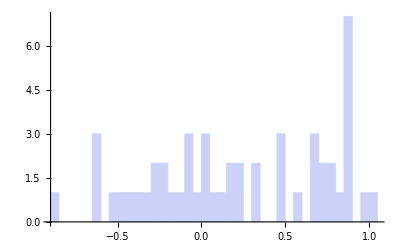
PreFlopHand Pairs that cannot be ranked for all combinations of suits across hands


 | Hand A | Equity A (%, Avg) | Equity B (%, Avg) | Hand B | Equity A - Equity B
1 | 52s | 50.233 | 49.767 | 43s | 0.467
2 | 65o | 49.677 | 50.323 | 22o | -0.646
3 | 72o | 50.348 | 49.652 | 64s | 0.696
4 | 73o | 50.341 | 49.659 | 65s | 0.682
5 | 75o | 49.699 | 50.301 | 22o | -0.602
6 | 82o | 50.510 | 49.490 | 65s | 1.021
7 | 82o | 49.678 | 50.322 | 76s | -0.643
8 | 83o | 50.383 | 49.617 | 76s | 0.765
9 | 83o | 50.233 | 49.767 | 82s | 0.465
10 | 86o | 49.799 | 50.201 | 22o | -0.401
11 | 92o | 50.478 | 49.522 | 76s | 0.955
12 | 93o | 50.440 | 49.560 | 92s | 0.880
13 | 94o | 50.288 | 49.712 | 93s | 0.575
14 | 97o | 50.437 | 49.563 | 22o | 0.873
15 | 97s | 49.898 | 50.102 | 55o | -0.205
16 | 98o | 50.333 | 49.667 | 44o | 0.667
17 | 98s | 49.994 | 50.006 | 66o | -0.012
18 | T3o | 50.440 | 49.560 | T2s | 0.880
19 | T6s | 49.954 | 50.046 | 33o | -0.091
20 | T7o | 49.802 | 50.198 | 22o | -0.397
21 | T7s | 49.874 | 50.126 | 55o | -0.252
22 | T8o | 50.068 | 49.932 | 33o | 0.136
23 | T9o | 50.392 | 49.608 | 44o | 0.783
24 | T9o | 50.008 | 49.992 | 55o | 0.016
25 | J3o | 50.439 | 49.561 | J2s | 0.878
26 | J5s | 49.855 | 50.145 | 22o | -0.291
27 | J6s | 49.959 | 50.041 | 22o | -0.082
28 | J7s | 50.152 | 49.848 | 33o | 0.305
29 | J9o | 50.370 | 49.630 | 22o | 0.740
30 | J9o | 49.745 | 50.255 | 33o | -0.511
31 | JTo | 50.440 | 49.560 | 44o | 0.880
32 | JTo | 50.031 | 49.969 | 55o | 0.062
33 | JTo | 49.752 | 50.248 | 66o | -0.496
34 | Q3o | 50.439 | 49.561 | Q2s | 0.877
35 | Q6s | 50.109 | 49.891 | 22o | 0.218
36 | QTo | 49.920 | 50.080 | 33o | -0.159
37 | QJo | 50.228 | 49.772 | 22o | 0.457
38 | QJo | 49.569 | 50.431 | 33o | -0.861
39 | K3o | 50.438 | 49.562 | K2s | 0.876
40 | K6s | 49.934 | 50.066 | 22o | -0.132
41 | K8s | 49.957 | 50.043 | 22o | -0.086
42 | K9s | 50.087 | 49.913 | 33o | 0.174
43 | KQs | 50.011 | 49.989 | 44o | 0.022
44 | A3o | 50.355 | 49.645 | A2s | 0.710
45 | A4o | 50.406 | 49.594 | A3s | 0.811
46 | A5s | 50.098 | 49.902 | 22o | 0.196
47 | A7s | 50.120 | 49.880 | 22o | 0.240
48 | A8s | 50.024 | 49.976 | 22o | 0.048
49 | ATs | 50.169 | 49.831 | 33o | 0.339
50 | AJs | 49.848 | 50.152 | 33o | -0.303
51 | AKs | 49.893 | 50.107 | 22o | -0.213


Equity Difference among such PreFlopHand Pairs


Max = "1.021"
Max = "-0.861"
Avg = "0.222"
Median = "0.196"
-Graphics-

```mathematica
preFlop2HandTableNoPrevail=Module[{table,table1,table2},
table=Select[preFlop2HandTable,#[[1]]!=#[[2]]&];
table1=Select[table,(oneWay[#]==3||oneWay[#]==0)&];
table2=Table[{
table1[[i,1]]/.faceChoice,
table1[[i,2]]/.faceChoice,
table1[[i,3,All,6,1]],
table1[[i,3,All,6,2]]
},{i,Length[table1]}];
table2
];
format1[tablePreFlop2Hand_]:=Module[{table1,table2},
table1=Map[Text,Table[{
Row[{tablePreFlop2Hand[[i,1,1]],tablePreFlop2Hand[[i,1,2]],tablePreFlop2Hand[[i,1,3]]}],
NumberForm[N[100*Total[tablePreFlop2Hand[[i,3]]]/Length[tablePreFlop2Hand[[i,3]]]],{5,3}],
NumberForm[N[100*Total[tablePreFlop2Hand[[i,4]]]/Length[tablePreFlop2Hand[[i,4]]]],{5,3}],
Row[{tablePreFlop2Hand[[i,2,1]],tablePreFlop2Hand[[i,2,2]],tablePreFlop2Hand[[i,2,3]]}],
NumberForm[N[100*Total[tablePreFlop2Hand[[i,3]]]/Length[tablePreFlop2Hand[[i,3]]]]-N[100*Total[tablePreFlop2Hand[[i,4]]]/Length[tablePreFlop2Hand[[i,4]]]],{5,3}]
},{i,Length[tablePreFlop2Hand]}
],{2}];
table1=Prepend[table1,Map[Text@Style[#,Bold]&,{"Hand A","Equity A (%, Avg)","Equity B (%, Avg)","Hand B","Equity A - Equity B"}]];
table1=Transpose[Prepend[Transpose[table1],Prepend[Map[Text[#]&,Range[Length[table1]-1]],""]]];
table2=Flatten@Table[{
100*Total[tablePreFlop2Hand[[i,3]]]/Length[tablePreFlop2Hand[[i,3]]]-
100*Total[tablePreFlop2Hand[[i,4]]]/Length[tablePreFlop2Hand[[i,4]]]
},{i,Length[tablePreFlop2Hand]}
];
Column[{
Text@Style["PreFlopHand Pairs that cannot be ranked for all combinations of suits across hands",Larger,Bold],
"\n",
Grid[table1,
Dividers->{{2->Black},{2->Black}},
Background->{None,{{None,LightRed}}}
],
(*TableForm[Map[Text,table1,{2}],
TableAlignments->Center,
TableSpacing->{0.75,0.75},
TableHeadings->{Automatic,Text/@{"Hand A","Equity A (%, Avg)","Equity B (%, Avg)","Hand B","Equity A - Equity B"}}
],*)
"\n",
Text@Style["Equity Difference among such PreFlopHand Pairs",Larger,Bold],
"\n",
Text@StringForm["Max = ``",NumberForm[Max[table2],{5,3}]],
Text@StringForm["Max = ``",NumberForm[Min[table2],{5,3}]],
Text@StringForm["Avg = ``",NumberForm[Total[table2]/Length[table2],{5,3}]],
Text@StringForm["Median = ``",NumberForm[Median[table2],{5,3}]],
Histogram[table2,30]
},Center
]
];
format1[preFlop2HandTableNoPrevail]
```

```mathematica
preFlop2HandTableSorted=SortBy[preFlop2HandTable,{#[[1]],#[[2]]}&];
preFlopHandList=Union[preFlop2HandTableSorted[[All,1]]];

preFlopHandMatrix=Module[{matrix,pf2hinfo,eq,p=1},
matrix=Table[-1,{169},{169}];
Do[Do[
If[i==j,
matrix[[i,j]]=0.5,
(*else*)
pf2hinfo=preFlop2HandTableSorted[[p]];
eq=Total[#]/Length[#]&[pf2hinfo[[3,All,6,1]]];
matrix[[i,j]]=eq;
matrix[[j,i]]=1.0-eq;
];
p++,
{j,i}],{i,169}];
matrix
];
```

```mathematica
(*SetDirectory[FileNameJoin[{repoDir,"Tables"}]];
Export["preFlopHandMatrix.csv",preFlopHandMatrix];
Export["preFlopHandList.csv",preFlopHandList];*)
```

```mathematica
Manipulate[
DynamicModule[{posn=Table[0,{2}],pair=Table[0,{2}]},
posn=normPos[pos];
pair[[1]]=posn[[1]];
pair[[2]]=169+1-posn[[2]];
Column[{
Text@Style["One-To-One Equity Distribution for a 2 PreFlop Hands",Larger,Bold],
Row[{
Row[Text/@{"x = ",Dynamic[pair[[1]]]}],
"\t",
Text@Style[Row[preFlopHandList[[pair[[1]]]]/.faceChoice],Bold,Red],
"\t",
Dynamic[format2[pair]],
"\t",
Text@Style[Row[preFlopHandList[[pair[[2]]]]/.faceChoice],Bold,Red],
"\t",
Row[Text/@{"y = ",Dynamic[pair[[2]]]}]
}],
"\n",
Text@Style["Color Code for Equity %",Bold],
legend,
LocatorPane[Dynamic[pos],array]
},Center]
],
{{pos,{84.5,84.5}},None},
Initialization:>(
normPos[pos_]:=Module[{result=Table[0,{2}]},
result[[1]]=Round[pos[[1]]+0.5];
result[[1]]=Min[Max[1,result[[1]]],169];
result[[2]]=Round[pos[[2]]+0.5];
result[[2]]=Min[Max[1,result[[2]]],169];
result
];
colorTheme="ThermometerColors";
format2[pair_]:=Module[{},
BarChart[{preFlopHandMatrix[[pair[[1]],pair[[2]]]],1-preFlopHandMatrix[[pair[[1]],pair[[2]]]]},
ChartLegends->None,
ChartStyle->{ColorData[colorTheme][1-preFlopHandMatrix[[pair[[1]],pair[[2]]]]],ColorData[colorTheme][preFlopHandMatrix[[pair[[1]],pair[[2]]]]]},
LabelingFunction->(Placed[NumberForm[100*#,{5,2}]"%",Above]&),
Axes->{True,False},
ImageSize->150,
AspectRatio->1/3
]
];
array=
ArrayPlot[
preFlopHandMatrix,
ColorFunction->colorTheme,
ImageSize->700,
ImageMargins->0,
Frame->Automatic,
FrameTicks->Automatic
];
legend=DensityPlot[1-x,{x,0,1},{y,0,1},
ColorFunction->colorTheme,
AspectRatio->1/10,
Frame->True,
FrameTicks->{{None,None},{All,None}},
PlotRangePadding->None,
ImageSize->{150,Automatic}]
)
]
```

```mathematica
Table[Text@Row[preFlopHandList[[i]]]/.faceChoice,{i,Length[preFlopHandList]}]
Table[Text@i,{i,Length[preFlopHandList]}]
```

{22o,32o,32s,33o,42o,42s,43o,43s,44o,52o,52s,53o,53s,54o,54s,55o,62o,62s,63o,63s,64o,64s,65o,65s,66o,72o,72s,73o,73s,74o,74s,75o,75s,76o,76s,77o,82o,82s,83o,83s,84o,84s,85o,85s,86o,86s,87o,87s,88o,92o,92s,93o,93s,94o,94s,95o,95s,96o,96s,97o,97s,98o,98s,99o,T2o,T2s,T3o,T3s,T4o,T4s,T5o,T5s,T6o,T6s,T7o,T7s,T8o,T8s,T9o,T9s,TTo,J2o,J2s,J3o,J3s,J4o,J4s,J5o,J5s,J6o,J6s,J7o,J7s,J8o,J8s,J9o,J9s,JTo,JTs,JJo,Q2o,Q2s,Q3o,Q3s,Q4o,Q4s,Q5o,Q5s,Q6o,Q6s,Q7o,Q7s,Q8o,Q8s,Q9o,Q9s,QTo,QTs,QJo,QJs,QQo,K2o,K2s,K3o,K3s,K4o,K4s,K5o,K5s,K6o,K6s,K7o,K7s,K8o,K8s,K9o,K9s,KTo,KTs,KJo,KJs,KQo,KQs,KKo,A2o,A2s,A3o,A3s,A4o,A4s,A5o,A5s,A6o,A6s,A7o,A7s,A8o,A8s,A9o,A9s,ATo,ATs,AJo,AJs,AQo,AQs,AKo,AKs,AAo}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169}

```mathematica
Manipulate[
Module[{pfh,i,vector},
If[!(f1==f2 && t=="s"),
pfh=order2[{f1,f2,t}]/.faceChoiceRev;
i=First@First@Position[preFlopHandList,pfh];
vector=preFlopHandMatrix[[i,All]];
Column[{
Text@Style["One PreFlopHand vs. All Other PreFlopHands",Larger,Bold],
"\n",
ListPlot[Table[Tooltip[vector[[k]],toolTipFunction[k,vector]],{k,Length[vector]}],
PlotRange->{Automatic,{0,1}},
ImageSize->500
]
},
Center]
]
],
Text@Style["PreFlop Hand\n",11,Bold],
{{f1,7,"First face"},faceChoice},
{{f2,6,"Second face"},faceChoice},
{{t,"o","Type"},If[f1!=f2,suitChoice,suitNoChoice]},
ControlPlacement->Top,
ControlType->SetterBar,
ContentSize->{600,400},
Initialization:>(
toolTipFunction[i_,vector_]:=Column[{
Text@NumberForm[100*vector[[i]]"%",{5,2}],
Text@Row[preFlopHandList[[i]]]/.faceChoice,
Text@i
}];
order2[pfh_]:=If[pfh[[1]]<pfh[[2]],
{pfh[[2]],pfh[[1]],pfh[[3]]},
pfh
];
)
]
```

#### Exhaustive Game Analysis - Knowing all players PreFlop hands

```mathematica
Manipulate[
DynamicModule[{
deckPos={0.5,0.5},
deckStatus=Table[1,{52}],
deckNo=52,
deckSelect=0,
tablePos={0.5,0.5},
tableStatus=Table[0,{5}],
tableNo=1,
playerPos={0.5,0.9},
playerStatus=Table[{0,0},{i,10}],
playerNo={1,1},
update,
statusMsg="Cannot compute equities: Table cards are inconsistent or at least one preFlop hand is not determined",
handEquity={Table[{0.00,0.00},{i,10}],0,Table[0,{i,10}]}
},
Grid[{
{EventHandler[
Dynamic[
Grid[
Transpose[
Partition[
Table[If[i==deckSelect,deckCardImageSelect[[i]],If[deckStatus[[i]]==1,deckCardImagePad[[i]],deckCardImagePad[[53]]]],{i,52}],
4]
],Spacings->{0,0}
]
],
 {"MouseDown":>(
deckPos=MousePosition["EventHandlerScaled"];
deckNo=deckPoint[deckPos];
update=deckUpdateStatus[deckNo,deckStatus,deckSelect,tableStatus];
deckStatus=update[[1]];deckSelect=update[[2]];tableStatus=update[[3]];
update=stateUpdateStatus[deckStatus,tableStatus,playerStatus,statusMsg,handEquity];
statusMsg=update[[1]];handEquity=update[[2]];
)
}
],SpanFromLeft},
{Row[{" ",Item[Button[Text@Style["Reset",Smaller],
update=reset[deckStatus,deckSelect,tableStatus,playerStatus];
deckStatus=update[[1]];deckSelect=update[[2]];tableStatus=update[[3]];playerStatus=update[[4]];
update=stateUpdateStatus[deckStatus,tableStatus,playerStatus,statusMsg,handEquity];
statusMsg=update[[1]];handEquity=update[[2]];
]]," "}],SpanFromLeft},
{Row[{Item[Button[Text@Style["Shuffle Flop",Smaller],
update=shuffleFlop[deckStatus,deckSelect,tableStatus];
deckStatus=update[[1]];deckSelect=update[[2]];tableStatus=update[[3]];
update=stateUpdateStatus[deckStatus,tableStatus,playerStatus,statusMsg,handEquity];
statusMsg=update[[1]];handEquity=update[[2]];
]],
Item[Button[Text@Style["Shuffle Turn",Smaller],
update=shuffleTurn[deckStatus,deckSelect,tableStatus];
deckStatus=update[[1]];deckSelect=update[[2]];tableStatus=update[[3]];
update=stateUpdateStatus[deckStatus,tableStatus,playerStatus,statusMsg,handEquity];
statusMsg=update[[1]];handEquity=update[[2]];
]],
Item[Button[Text@Style["Shuffle River",Smaller],
update=shuffleRiver[deckStatus,deckSelect,tableStatus];
deckStatus=update[[1]];deckSelect=update[[2]];tableStatus=update[[3]];
update=stateUpdateStatus[deckStatus,tableStatus,playerStatus,statusMsg,handEquity];
statusMsg=update[[1]];handEquity=update[[2]];
]]
}],SpanFromLeft},
{EventHandler[
Dynamic[
Row[
Table[Column[{
deckCardImagePad[[If[tableStatus[[i]]≠0, tableStatus[[i]],53]]],
Text@Map[Style[#,Bold]&,{"Flop","Flop","Flop","Turn","River"}][[i]]
},Center],{i,5}]
]
],
 {"MouseDown":>(
tablePos=MousePosition["EventHandlerScaled"];
tableNo=tablePoint[tablePos];
update=tableUpdateStatus[tableNo,deckStatus,deckSelect,tableStatus];
deckStatus=update[[1]];deckSelect=update[[2]];tableStatus=update[[3]];
update=stateUpdateStatus[deckStatus,tableStatus,playerStatus,statusMsg,handEquity];
statusMsg=update[[1]];handEquity=update[[2]];
)
}
],SpanFromLeft},
{Dynamic[Text@Row[{"Number of possible games = ",NumberForm[handEquity[[2]],DigitBlock->3,NumberSeparator->","]}]],SpanFromLeft},
{Dynamic[
Grid[
Join[
Map[Text,Transpose@Table[handNameDet[handEquity[[3,i]]],{i,np}],{2}],
{Map[Text@NumberForm[#,DigitBlock->3,NumberSeparator->","]&,Table[handEquity[[3,i]],{i,np}],{1}]},
Map[Text@NumberForm[100*#,{4,2}]"%"&,Transpose[Table[{Total[handEquity[[1,i]]],handEquity[[1,i,2]],handEquity[[1,i,1]]},{i,np}]],{2}]
],
Frame->True,
Spacings->1.65,
Background->{None,{4->Pink},None}
]
],SpanFromLeft
},
{Dynamic[
BarChart[
Table[handEquity[[1,i]],{i,np}],
ChartLayout->"Stacked",
Joined->True,
Axes->{False,False},
ChartStyle->Automatic,
BarSpacing->Automatic,
LabelingFunction->(Placed[NumberForm[100*#,{4,2}]"%",Center]&),
ImageSize->{Round[700*np/10],70},
AspectRatio->N[1.25/np],
ImagePadding->0,
ChartLegends->{"Equity from Wins","Equity from Ties"},
LegendAppearance->"Row"
]
],SpanFromLeft
},
{EventHandler[
Dynamic[
Row[
Table[Column[{
deckCardImagePad[[If[playerStatus[[i,1]]≠0, playerStatus[[i,1]],53]]],
deckCardImagePad[[If[playerStatus[[i,2]]≠0, playerStatus[[i,2]],53]]],
Text@Style[namePlayer[[i]],Bold]
},Center],{i,np}]
]
],
 {"MouseDown":>(
playerPos=MousePosition["EventHandlerScaled"];
playerNo=playerPoint[playerPos,np];
update=playerUpdateStatus[playerNo,deckStatus,deckSelect,playerStatus];
deckStatus=update[[1]];deckSelect=update[[2]];playerStatus=update[[3]];
update=stateUpdateStatus[deckStatus,tableStatus,playerStatus,statusMsg,handEquity];
statusMsg=update[[1]];handEquity=update[[2]];
)
}
],SpanFromLeft},
{Row[{" ",Item[Button[Text@Style["Shuffle All Players",Smaller],
update=shuffleAllPlayer[deckStatus,deckSelect,playerStatus,np];
deckStatus=update[[1]];deckSelect=update[[2]];playerStatus=update[[3]];
update=stateUpdateStatus[deckStatus,tableStatus,playerStatus,statusMsg,handEquity];
statusMsg=update[[1]];handEquity=update[[2]];
]]," "}],SpanFromLeft},
{Text@Style["Shuffle Individual PreFlopHand"],SpanFromLeft},
{Row[
Table[With[{i=i},Item[Dynamic[Button[Text@Style[""<>ToString[namePlayer[[i]]],Smaller],
update=shufflePlayer[deckStatus,deckSelect,playerStatus,i];
deckStatus=update[[1]];deckSelect=update[[2]];playerStatus=update[[3]];
update=stateUpdateStatus[deckStatus,tableStatus,playerStatus,statusMsg,handEquity];
statusMsg=update[[1]];handEquity=update[[2]],
ImageSize->{Automatic,Automatic}
]]]],
{i,np}]],SpanFromLeft
},
{Dynamic@Text@Style["\n"<>statusMsg,Red],SpanFromLeft}
},Frame->False]
],

Text@Style["Hand Equity Calculator - knowing all Players PreFlop Hands\n",11,Bold],
{{np,6,"Number of Players"},2,10,1,ControlType->SetterBar},
ControlPlacement->Top,
ContentSize->{730,1100},

Initialization:>(
namePlayer={"Joe","Jack","William","Averell","Jolly","Jumper","Lucky","Luke","Rantan","Sherif"};
handName = {{"High","Card"},{"One","Pair"},{"Two","Pairs"},{"Triple",""},{"Straight",""},{"Flush",""},{"Full","House"},{"Quad",""},{"Straight","Flush"},{"",""}};
handNameDet[rank_]:=Block[{hn={" "," "}},
hn=If[rank!=0,Which[
rank≤cumulUpNbDistinctHand[[1]],handName[[1]],
rank≤cumulUpNbDistinctHand[[2]],handName[[2]],
rank≤cumulUpNbDistinctHand[[3]],handName[[3]],
rank≤cumulUpNbDistinctHand[[4]],handName[[4]],
rank≤cumulUpNbDistinctHand[[5]],handName[[5]],
rank≤cumulUpNbDistinctHand[[6]],handName[[6]],
rank≤cumulUpNbDistinctHand[[7]],handName[[7]],
rank≤cumulUpNbDistinctHand[[8]],handName[[8]],
True,handName[[9]]
],
(*else*)
handName[[10]]
]
];
deckPoint[posDeck_]:=Block[{nbFace=13,nbSuit=4,f,s,c},
f=Min[Max[1,Round[nbFace*posDeck[[1]]+0.5]],nbFace];
s=nbSuit+1-Min[Max[1,Round[nbSuit*posDeck[[2]]+0.5]],nbSuit];
c=deckCardNo[f,s]
];
tablePoint[posTable_]:=Block[{nbCard=5,c},
c=Min[Max[1,Round[nbCard*posTable[[1]]+0.5]],nbCard]
];
playerPoint[playerPos_,nbPlayer_]:=Block[{nbCard=2,p,c},
p=Min[Max[1,Round[nbPlayer*playerPos[[1]]+0.5]],nbPlayer];
c=nbCard+1-Min[Max[1,Round[nbCard*0.95*playerPos[[2]]+0.5]],nbCard];
{p,c}
];
tableStatusValid[tableStatus_]:=Module[{output=0},
If[(tableStatus[[1]]==0&&tableStatus[[2]]==0&&tableStatus[[3]]==0&&tableStatus[[4]]==0&&tableStatus[[5]]==0)||(tableStatus[[1]]>0&&tableStatus[[2]]>0&&tableStatus[[3]]>0&&tableStatus[[4]]==0&&tableStatus[[5]]==0)||
(tableStatus[[1]]>0&&tableStatus[[2]]>0&&tableStatus[[3]]>0&&tableStatus[[4]]>0&&tableStatus[[5]]==0)||
(tableStatus[[1]]>0&&tableStatus[[2]]>0&&tableStatus[[3]]>0&&tableStatus[[4]]>0&&tableStatus[[5]]>0),
output=1];
output
];
playerStatusValid[playerStatus_,nbPlayer_]:=Module[{output=0,test},
test=Take[Table[{If[playerStatus[[i,1]]>0,1,0],If[playerStatus[[i,2]]>0,1,0]},{i,10}],nbPlayer];
If[Total[test,2]==2*nbPlayer,output=1];
output
];
stateUpdateStatus[deckStatus_,tableStatus_,playerStatus_,statusMsg_,handEquity_]:=Module[
{statusMsgLocal=statusMsg,handEquityLocal=handEquity,tableStatusTest,playerStatusTest},
tableStatusTest=tableStatusValid[tableStatus];
playerStatusTest=playerStatusValid[playerStatus,np];
If[tableStatusTest==0||playerStatusTest==0, 
statusMsgLocal="Cannot compute equities: Table cards are inconsistent or at least one preFlop hand is not determined";
handEquityLocal={Table[{0.00,0.00},{i,10}],0,Table[0,{i,10}]};
,(*else*)
statusMsgLocal=" ";
handEquityLocal=EquityPreFlopHandML[
deckCardKey,deckCardSuit,deckCardFlushKey,flushCheck,rankFaceSeven,rankFlushSeven,deckStatus,tableStatus,playerStatus[[All,1]],playerStatus[[All,2]],np]
];
{statusMsgLocal,handEquityLocal}
];
deckUpdateStatus[deckNo_,deckStatus_,deckSelect_,tableStatus_]:=Module[
{deckStatusLocal=deckStatus,deckSelectLocal=deckSelect,tableStatusLocal=tableStatus},
If[deckSelectLocal==0,
If[deckStatusLocal[[deckNo]]≠0,
deckSelectLocal=deckNo;
deckStatusLocal[[deckSelectLocal]]=2;
];
,(*else*)
If[deckSelectLocal==deckNo,
deckStatusLocal[[deckSelectLocal]]=1;
deckSelectLocal=0;
,(*else*)
If[deckStatusLocal[[deckNo]]≠0,
deckStatusLocal[[deckSelectLocal]]=1;
deckSelectLocal=deckNo;
deckStatusLocal[[deckSelectLocal]]=2;
];
];
];
{deckStatusLocal,deckSelectLocal,tableStatusLocal}
];
tableUpdateStatus[tableNo_,deckStatus_,deckSelect_,tableStatus_]:=Module[
{deckStatusLocal=deckStatus,deckSelectLocal=deckSelect,tableStatusLocal=tableStatus},
If[deckSelectLocal==0,
If[tableStatusLocal[[tableNo]]≠0,
deckStatusLocal[[tableStatusLocal[[tableNo]]]]=1;
tableStatusLocal[[tableNo]]=0;
]
,(*else*)
If[tableStatusLocal[[tableNo]]==0,
deckStatusLocal[[deckSelectLocal]]=0;
tableStatusLocal[[tableNo]]=deckSelectLocal;
deckSelectLocal=0;
,(*else*)
deckStatusLocal[[tableStatusLocal[[tableNo]]]]=1;
deckStatusLocal[[deckSelectLocal]]=0;
tableStatusLocal[[tableNo]]=deckSelectLocal;
deckSelectLocal=0;
];
];
{deckStatusLocal,deckSelectLocal,tableStatusLocal}
];
playerUpdateStatus[playerNo_,deckStatus_,deckSelect_,playerStatus_]:=Module[
{deckStatusLocal=deckStatus,deckSelectLocal=deckSelect,playerStatusLocal=playerStatus},
If[deckSelectLocal==0,
If[playerStatusLocal[[First@playerNo,Last@playerNo]]≠0,
deckStatusLocal[[playerStatusLocal[[First@playerNo,Last@playerNo]]]]=1;
playerStatusLocal[[First@playerNo,Last@playerNo]]=0;
]
,(*else*)
If[playerStatusLocal[[First@playerNo,Last@playerNo]]==0,
deckStatusLocal[[deckSelectLocal]]=0;
playerStatusLocal[[First@playerNo,Last@playerNo]]=deckSelectLocal;
deckSelectLocal=0;
,(*else*)
deckStatusLocal[[playerStatusLocal[[First@playerNo,Last@playerNo]]]]=1;
deckStatusLocal[[deckSelectLocal]]=0;
playerStatusLocal[[First@playerNo,Last@playerNo]]=deckSelectLocal;
deckSelectLocal=0;
];
];
{deckStatusLocal,deckSelectLocal,playerStatusLocal}
];
reset[deckStatus_,deckSelect_,tableStatus_,playerStatus_]:=Module[
{deckStatusLocal=deckStatus,deckSelectLocal=deckSelect,
tableStatusLocal=tableStatus,playerStatusLocal=playerStatus},
deckSelectLocal=0;
deckStatusLocal=Table[1,{52}];
tableStatusLocal=Table[0,{5}];
playerStatusLocal=Table[{0,0},{10}];
{deckStatusLocal,deckSelectLocal,tableStatusLocal,playerStatusLocal}
];
shuffleFlop[deckStatus_,deckSelect_,tableStatus_]:=Module[
{deckStatusLocal=deckStatus,deckSelectLocal=deckSelect,tableStatusLocal=tableStatus,deckAvail,randomSample},
If[deckSelectLocal!=0,deckStatusLocal[[deckSelectLocal]]=1;deckSelectLocal=0];
Do[
If[tableStatusLocal[[i]]≠0,
deckStatusLocal[[tableStatusLocal[[i]]]]=1;
tableStatusLocal[[i]]=0
],
{i,3}];
deckAvail=Union[Flatten@Position[deckStatusLocal,1],Flatten@Position[deckStatusLocal,2]];
randomSample=RandomSample[deckAvail,3];
Do[
deckStatusLocal[[randomSample[[i]]]]=0;
tableStatusLocal[[i]]=randomSample[[i]],
{i,3}];
{deckStatusLocal,deckSelectLocal,tableStatusLocal}
];
shuffleTurn[deckStatus_,deckSelect_,tableStatus_]:=Module[
{deckStatusLocal=deckStatus,deckSelectLocal=deckSelect,tableStatusLocal=tableStatus,deckAvail,randomSample},
If[deckSelectLocal!=0,deckStatusLocal[[deckSelectLocal]]=1;deckSelectLocal=0];
If[tableStatusLocal[[4]]≠0,
deckStatusLocal[[tableStatusLocal[[4]]]]=1;
tableStatusLocal[[4]]=0
];
deckAvail=Union[Flatten@Position[deckStatusLocal,1],Flatten@Position[deckStatusLocal,2]];
randomSample=RandomChoice[deckAvail];
deckStatusLocal[[randomSample]]=0;
tableStatusLocal[[4]]=randomSample;
{deckStatusLocal,deckSelectLocal,tableStatusLocal}
];
shuffleRiver[deckStatus_,deckSelect_,tableStatus_]:=Module[
{deckStatusLocal=deckStatus,deckSelectLocal=deckSelect,tableStatusLocal=tableStatus,deckAvail,randomSample},
If[deckSelectLocal!=0,deckStatusLocal[[deckSelectLocal]]=1;deckSelectLocal=0];
If[tableStatusLocal[[5]]≠0,
deckStatusLocal[[tableStatusLocal[[5]]]]=1;
tableStatusLocal[[5]]=0
];
deckAvail=Union[Flatten@Position[deckStatusLocal,1],Flatten@Position[deckStatusLocal,2]];
randomSample=RandomChoice[deckAvail];
deckStatusLocal[[randomSample]]=0;
tableStatusLocal[[5]]=randomSample;
{deckStatusLocal,deckSelectLocal,tableStatusLocal}
];
shuffleAllPlayer[deckStatus_,deckSelect_,playerStatus_,nbPlayer_]:=Module[
{deckStatusLocal=deckStatus,deckSelectLocal=deckSelect,playerStatusLocal=playerStatus,deckAvail,randomSample},
If[deckSelectLocal!=0,deckStatusLocal[[deckSelectLocal]]=1;deckSelectLocal=0];
Do[
If[playerStatusLocal[[i,1]]≠0,
deckStatusLocal[[playerStatusLocal[[i,1]]]]=1;
playerStatusLocal[[i,1]]=0
];
If[playerStatusLocal[[i,2]]≠0,
deckStatusLocal[[playerStatusLocal[[i,2]]]]=1;
playerStatusLocal[[i,2]]=0
],
{i,nbPlayer}];
deckAvail=Union[Flatten@Position[deckStatusLocal,1],Flatten@Position[deckStatusLocal,2]];
randomSample=RandomSample[deckAvail,2*nbPlayer];
Do[
deckStatusLocal[[randomSample[[i]]]]=0;
playerStatusLocal[[i,1]]=randomSample[[i]];
deckStatusLocal[[randomSample[[i+nbPlayer]]]]=0;
playerStatusLocal[[i,2]]=randomSample[[i+nbPlayer]],
{i,nbPlayer}
];
{deckStatusLocal,deckSelectLocal,playerStatusLocal}
];
shufflePlayer[deckStatus_,deckSelect_,playerStatus_,playerIndex_]:=Module[
{deckStatusLocal=deckStatus,deckSelectLocal=deckSelect,playerStatusLocal=playerStatus,deckAvail,randomSample},
If[deckSelectLocal!=0,deckStatusLocal[[deckSelectLocal]]=1;deckSelectLocal=0];
If[playerStatusLocal[[playerIndex,1]]≠0,
deckStatusLocal[[playerStatusLocal[[playerIndex,1]]]]=1;
playerStatusLocal[[playerIndex,1]]=0
];
If[playerStatusLocal[[playerIndex,2]]≠0,
deckStatusLocal[[playerStatusLocal[[playerIndex,2]]]]=1;
playerStatusLocal[[playerIndex,2]]=0
];
deckAvail=Union[Flatten@Position[deckStatusLocal,1],Flatten@Position[deckStatusLocal,2]];
randomSample=RandomSample[deckAvail,2];
deckStatusLocal[[randomSample[[1]]]]=0;
playerStatusLocal[[playerIndex,1]]=randomSample[[1]];
deckStatusLocal[[randomSample[[2]]]]=0;
playerStatusLocal[[playerIndex,2]]=randomSample[[2]];
{deckStatusLocal,deckSelectLocal,playerStatusLocal}
];
)
]
```

#### PreFlop Equities - Unconstrained MonteCarlo

```mathematica
Needs["CCompilerDriver`"];
Needs["CompiledFunctionTools`"];
```

```mathematica
randomHandC=Compile[{{n,_Integer},{p,_Integer},{holeCard,_Integer,1}},
Module[{
table=Table[Table[0,{5+2*p}],{n}],
range=Drop[Drop[Range[52],{Max[holeCard]}],{Min[holeCard]}]
},
SeedRandom[Method->"MersenneTwister"];
(*SeedRandom[1234,Method->"MKL"];*)
(*SeedRandom[1234,Method->"ExtendedCA"];*)
Do[
table[[i]]=RandomSample[range,5+2*p],
{i,n}
];
Flatten@table
],
CompilationTarget->"C",RuntimeOptions->"Speed"
];
CompilePrint[randomHandC];
```

```mathematica
monteCarloDir=FileNameJoin[{$InitialDirectory,"Dropbox","Archives","Wolfram","Mathematica","Library","Poker","MonteCarlo"}];
SetDirectory[monteCarloDir];
allPreFlopHandDeckCard=Flatten[Table[If[f1>f2,{deckCardNo[f1,4],deckCardNo[f2,4]},{deckCardNo[f1,4],deckCardNo[f2,3]}],{f1,13,1,-1},{f2,13,1,-1}],1];
(*Map[deckCardId[[#]]&,allPreFlopHandDeckCard];*)
allPreFlopHandList = Flatten[Table[If[f1>f2,ToString[face[[f1]]]<>ToString[face[[f2]]]<>"s",ToString[face[[f1]]]<>ToString[face[[f2]]]<>"o"],{f1,13,1,-1},{f2,13,1,-1}],1];
equityPreFlopMonteCarloTable0 = {0, Table[Table[{0.0,0.0},{9}],{Length[allPreFlopHandDeckCard]}]};
n=0;
Export["equityPreFlopMonteCarloTable"<>ToString[n]<>".csv",equityPreFlopMonteCarloTable0];
```

```mathematica
SetDirectory[monteCarloDir];
nbRandomGame=1000000;
n=999;(* current monte carlo file - update manually*)
t={SessionTime[]};
Print["init=",t];
Do[
t=Append[t,SessionTime[]];
Print["NewRandom=",Last[t],"  n=",n];
equityPreFlopMonteCarloTableIncr=Table[Table[{0.0,0.0},{9}],{Length[allPreFlopHandDeckCard]}];
Do[
playerCard=allPreFlopHandDeckCard[[i]];
randomCard=randomHandC[nbRandomGame,9,playerCard];
equityPreFlopMonteCarloTableIncr[[i]]=EquityPreFlopMonteCarloML[deckCardKey,deckCardSuit,deckCardFlushKey,flushCheck,rankFaceSeven,rankFlushSeven,playerCard,randomCard];
,{i,Length[allPreFlopHandDeckCard]}
];
t=Append[t,SessionTime[]];
Print["postRandom=",Last[t]];
(*import Monte Carlo past results*)
equityPreFlopMonteCarloTablePast=ToExpression[Import["equityPreFlopMonteCarloTable"<>ToString[n]<>".csv"]];
equityPreFlopMonteCarloTablePast[[1]]=equityPreFlopMonteCarloTablePast[[1,1]];
nbRandomPast=equityPreFlopMonteCarloTablePast[[1]];
t=Append[t,SessionTime[]];
Print["PostImport=",Last[t]];
(*calculate new Monte Carlo results*)
equityPreFlopMonteCarloTableNew={
equityPreFlopMonteCarloTablePast[[1]]+1,
Table[{
(equityPreFlopMonteCarloTablePast[[2,i,j,1]]*nbRandomPast+equityPreFlopMonteCarloTableIncr[[i,j,1]]*1.0)/(nbRandomPast+1.0),
(equityPreFlopMonteCarloTablePast[[2,i,j,2]]*nbRandomPast+equityPreFlopMonteCarloTableIncr[[i,j,2]]*1.0)/(nbRandomPast+1.0)},
{i,Length[allPreFlopHandDeckCard]},{j,9}]
};
t=Append[t,SessionTime[]];
Print["postUpdate=",Last[t]];
(*export Monte Carlo new results*)
n++;
Export["equityPreFlopMonteCarloTable"<>ToString[n]<>".csv",equityPreFlopMonteCarloTableNew];
t=Append[t,SessionTime[]];
Print["PostExport=",Last[t]];
,{k,100}]
```

```mathematica
equityPreFlopMonteCarloAll = Module[{n=1, tableAll},
SetDirectory[monteCarloDir];
While[FileNames["equityPreFlopMonteCarloTable"<>ToString[n]<>".csv",Directory[]]≠{},n++];
n--;
Monitor[
tableAll=Table[
ToExpression[Import["equityPreFlopMonteCarloTable"<>ToString[i]<>".csv"]][[2]],
{i,n}
],
i];
tableAll
];
ByteCount[equityPreFlopMonteCarloAll]
```

54089176

```mathematica
(*SetDirectory[monteCarloDir];
Export["equityPreFlopMonteCarloAll.csv",equityPreFlopMonteCarloAll];*)
```

```mathematica
(*SetDirectory[monteCarloDir];
AbsoluteTiming[equityPreFlopMonteCarloAll=ToExpression[Import["equityPreFlopMonteCarloAll.csv"]];]*)
```

```mathematica
SetDirectory[monteCarloDir];
AbsoluteTiming[
equityPreFlopMonteCarloAllFlat=ReadList["equityPreFlopMonteCarloAllFlat.csv",Real];]
AbsoluteTiming[equityPreFlopMonteCarloAll=Fold[Partition,equityPreFlopMonteCarloAllFlat,{2,9,169}];]
Clear[equityPreFlopMonteCarloAllFlat];
```

{1.29587,Null}

{0.05616,Null}

```mathematica
(*AbsoluteTiming[equityPreFlopMonteCarloAll2=Fold[Partition,Flatten@Import["https://dl.dropbox.com/u/10720544/WebBigFiles/Poker/equityPreFlopMonteCarloAllFlat.csv"],{2,9,169}];]
ByteCount[equityPreFlopMonteCarloAll2]
ByteCount[equityPreFlopMonteCarloAll]
equityPreFlopMonteCarloAll2==equityPreFlopMonteCarloAll*)
```

True

54089176

54089176

{76.792718,Null}

```mathematica
Manipulate[
Module[{pfh,hn,extractWin,extractTie},
If[!(f1==f2 && t=="s"),
pfh=order2[{f1,f2,t}]/.faceChoiceRev;
hn=First@First@Position[preFlopHandList,pfh];
extractWin=equityPreFlopMonteCarloAll[[All,hn,np,1]];
extractTie=equityPreFlopMonteCarloAll[[All,hn,np,2]];
Column[{
Text@Style["Monte Carlo Convergence of a PreFlop Hand Equity (Win)",Larger,Bold],
"\n",
ListPlot[100*extractWin,
ImageSize->600,
AxesLabel->{"Millions of Monte Carlo simulations", "PreFlop Hand Equity (Wins) in %"}
],
"\n\n",
Text@Style["Monte Carlo Convergence of a PreFlop Hand Equity (Win)",Larger,Bold],
"\n",
ListPlot[100*extractTie,
ImageSize->600,
AxesLabel->{"Millions of Monte Carlo simulations", "PreFlop Hand Equity (Ties) in %"}
]
},
Center]
]
],

Text@Style["PreFlop Hand\n",11,Bold],
{{f1,7,"First face"},faceChoice},
{{f2,6,"Second face"},faceChoice},
{{t,"o","Type"},If[f1!=f2,suitChoice,suitNoChoice]},
{{np,5,"Number of Opponents"},1,9,1},
ControlPlacement->Top,
ControlType->SetterBar,
ContentSize->{650,680},

Initialization:>(
order2[pfh_]:=If[pfh[[1]]<pfh[[2]],
{pfh[[2]],pfh[[1]],pfh[[3]]},
pfh
];
)
]
```

```mathematica
(*equityPreFlopMonteCarloLast=Last[equityPreFlopMonteCarloAll];*)
SetDirectory[monteCarloDir];
n=303;
equityPreFlopMonteCarloLast=ToExpression[Import["equityPreFlopMonteCarloTable"<>ToString[n]<>".csv"]][[2]];
```

```mathematica
equityPreFlopMonteCarloLastDisplay[eqtyTable_]:=Module[{gridAll,arrayTotal,arrayWin,arrayTie,colorTheme="ThermometerColors"},
gridAll=Table[Text@Row[{
NumberForm[100*(eqtyTable[[i,j,1]]+eqtyTable[[i,j,2]]),{4,2}],
" (",
NumberForm[100*eqtyTable[[i,j,2]],{4,2}],
")"
}],{i,Length[eqtyTable]},{j,Length[eqtyTable[[i]]]}];
gridAll=Prepend[gridAll,Table[Text@Style[i,Bold],{i,9}]];
gridAll=Transpose[Prepend[Transpose[gridAll],Prepend[Map[Text@Style[#,Bold]&,allPreFlopHandList],""]]];
gridAll=Transpose[Prepend[Transpose[gridAll],Prepend[Map[Text[#]&,Range[169]],""]]];
arrayWin=Table[eqtyTable[[i,j,1]],{i,Length[eqtyTable]},{j,Length[eqtyTable[[i]]]}];
arrayTie=Table[eqtyTable[[i,j,2]],{i,Length[eqtyTable]},{j,Length[eqtyTable[[i]]]}];
arrayTotal=Table[eqtyTable[[i,j,1]]+eqtyTable[[i,j,2]],{i,Length[eqtyTable]},{j,Length[eqtyTable[[i]]]}];
{{Grid[Prepend[Take[gridAll,2;;51],Prepend[Table[Text@Style[i,Bold],{i,9}]," "]],
Dividers->{{3->Black},{2->Black}},
Background->{None,{{None,LightRed}}}
],
Grid[Prepend[Take[gridAll,52;;101],Prepend[Table[Text@Style[i,Bold],{i,9}]," "]],
Dividers->{{3->Black},{2->Black}},
Background->{None,{{None,LightRed}}}
],
Grid[Prepend[Take[gridAll,102;;170],Prepend[Table[Text@Style[i,Bold],{i,9}]," "]],
Dividers->{{3->Black},{2->Black}},
Background->{None,{{None,LightRed}}}
]
},
Column[{
Text@Style["Color Code for Equity %",Bold],
DensityPlot[x,{x,0,1},{y,0,1},
ColorFunction->colorTheme,
AspectRatio->1/10,
Frame->True,
FrameTicks->{{None,None},{All,None}},
PlotRangePadding->None,
ImageSize->{150,Automatic}],
ArrayPlot[
arrayTotal,
ColorFunction->colorTheme,
ImageSize->300,
AspectRatio->2,
ImageMargins->0,
Frame->Automatic,
FrameTicks->Automatic,
DataReversed->False
]
},Center],
ListPlot3D[arrayTotal,
PlotRange->All,
ColorFunction->(ColorData[colorTheme][1.0-#1]&),
(*DataRange->{{1,9},{1,Length[eqtyTable]}},*)
ImageSize->600,
Mesh->Automatic
],
arrayWin,
arrayTie,
arrayTotal
}
];
```

```mathematica
equityPreFlopMonteCarloLastDisplay[equityPreFlopMonteCarloLast][[3]]
```

-Graphics3D-

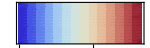
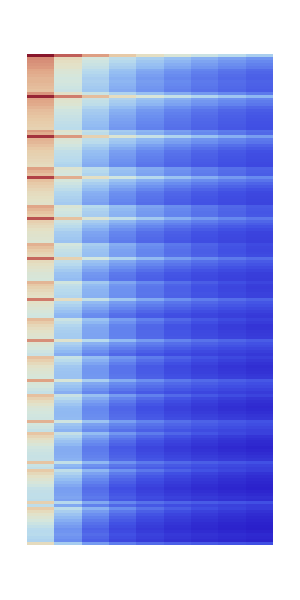
Color Code for Equity %
-Graphics-
-Graphics-

```mathematica
equityPreFlopMonteCarloLastDisplay[equityPreFlopMonteCarloLast][[2]]
```

```mathematica
equityPreFlopMonteCarloLastDisplay[equityPreFlopMonteCarloLast][[1]]
```

{  | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 
1 | AAo | 85.20 (0.27) | 73.44 (0.23) | 63.83 (0.22) | 55.87 (0.22) | 49.19 (0.22) | 43.54 (0.22) | 38.73 (0.22) | 34.61 (0.22) | 31.08 (0.21)
2 | AKs | 67.05 (0.83) | 50.72 (0.89) | 41.43 (0.90) | 35.41 (0.89) | 31.07 (0.88) | 27.70 (0.88) | 24.96 (0.87) | 22.66 (0.87) | 20.69 (0.86)
3 | AQs | 66.21 (0.89) | 49.42 (1.00) | 39.85 (1.03) | 33.69 (1.04) | 29.31 (1.03) | 25.97 (1.02) | 23.30 (1.01) | 21.09 (1.00) | 19.24 (0.98)
4 | AJs | 65.39 (0.99) | 48.20 (1.14) | 38.46 (1.18) | 32.24 (1.18) | 27.88 (1.18) | 24.59 (1.16) | 22.01 (1.15) | 19.90 (1.12) | 18.16 (1.10)
5 | ATs | 64.60 (1.11) | 47.07 (1.28) | 37.21 (1.32) | 31.00 (1.33) | 26.70 (1.32) | 23.50 (1.30) | 21.00 (1.28) | 19.00 (1.25) | 17.35 (1.22)
6 | A9s | 62.78 (1.27) | 44.55 (1.44) | 34.51 (1.45) | 28.32 (1.41) | 24.13 (1.37) | 21.08 (1.33) | 18.74 (1.28) | 16.88 (1.24) | 15.38 (1.19)
7 | A8s | 61.94 (1.44) | 43.51 (1.62) | 33.47 (1.60) | 27.34 (1.55) | 23.22 (1.50) | 20.25 (1.44) | 17.98 (1.39) | 16.20 (1.33) | 14.76 (1.27)
8 | A7s | 60.99 (1.60) | 42.39 (1.76) | 32.41 (1.72) | 26.39 (1.66) | 22.39 (1.59) | 19.52 (1.53) | 17.35 (1.47) | 15.65 (1.41) | 14.28 (1.34)
9 | A6s | 59.91 (1.73) | 41.16 (1.86) | 31.29 (1.79) | 25.44 (1.71) | 21.60 (1.64) | 18.87 (1.58) | 16.82 (1.51) | 15.21 (1.45) | 13.92 (1.38)
10 | A5s | 59.92 (1.86) | 41.43 (1.97) | 31.74 (1.89) | 25.99 (1.80) | 22.19 (1.73) | 19.47 (1.66) | 17.40 (1.60) | 15.77 (1.53) | 14.45 (1.46)
11 | A4s | 59.03 (1.90) | 40.52 (1.98) | 30.97 (1.87) | 25.35 (1.76) | 21.67 (1.67) | 19.04 (1.60) | 17.05 (1.53) | 15.48 (1.45) | 14.21 (1.38)
12 | A3s | 58.22 (1.88) | 39.67 (1.94) | 30.23 (1.82) | 24.75 (1.70) | 21.18 (1.60) | 18.64 (1.52) | 16.71 (1.44) | 15.19 (1.36) | 13.96 (1.28)
13 | A2s | 57.38 (1.87) | 38.77 (1.91) | 29.44 (1.77) | 24.08 (1.63) | 20.60 (1.53) | 18.14 (1.44) | 16.27 (1.36) | 14.79 (1.27) | 13.59 (1.19)
14 | KAo | 65.32 (0.85) | 48.21 (0.92) | 38.54 (0.93) | 32.31 (0.93) | 27.85 (0.92) | 24.39 (0.91) | 21.58 (0.91) | 19.22 (0.90) | 17.21 (0.89)
15 | KKo | 82.40 (0.28) | 68.87 (0.24) | 58.24 (0.23) | 49.77 (0.24) | 42.96 (0.24) | 37.42 (0.25) | 32.90 (0.26) | 29.17 (0.26) | 26.09 (0.26)
16 | KQs | 63.40 (0.99) | 47.09 (0.99) | 38.20 (0.98) | 32.48 (0.97) | 28.34 (0.97) | 25.14 (0.96) | 22.56 (0.96) | 20.42 (0.95) | 18.63 (0.95)
17 | KJs | 62.57 (1.09) | 45.88 (1.12) | 36.82 (1.12) | 31.06 (1.11) | 26.95 (1.10) | 23.82 (1.09) | 21.34 (1.08) | 19.31 (1.07) | 17.64 (1.06)
18 | KTs | 61.79 (1.20) | 44.79 (1.25) | 35.63 (1.24) | 29.87 (1.23) | 25.83 (1.22) | 22.79 (1.21) | 20.40 (1.20) | 18.48 (1.19) | 16.90 (1.17)
19 | K9s | 59.99 (1.35) | 42.30 (1.38) | 32.95 (1.33) | 27.20 (1.27) | 23.25 (1.23) | 20.34 (1.19) | 18.09 (1.16) | 16.31 (1.13) | 14.86 (1.09)
20 | K8s | 58.31 (1.52) | 40.16 (1.54) | 30.78 (1.45) | 25.15 (1.37) | 21.37 (1.32) | 18.63 (1.27) | 16.54 (1.23) | 14.90 (1.19) | 13.57 (1.15)
21 | K7s | 57.54 (1.69) | 39.27 (1.69) | 29.93 (1.58) | 24.38 (1.49) | 20.67 (1.42) | 18.00 (1.36) | 15.98 (1.31) | 14.40 (1.26) | 13.13 (1.21)
22 | K6s | 56.64 (1.84) | 38.28 (1.80) | 29.04 (1.66) | 23.61 (1.55) | 20.02 (1.48) | 17.45 (1.41) | 15.51 (1.36) | 14.00 (1.30) | 12.78 (1.25)
23 | K5s | 55.79 (1.96) | 37.39 (1.88) | 28.26 (1.72) | 22.95 (1.60) | 19.48 (1.51) | 17.01 (1.45) | 15.14 (1.39) | 13.68 (1.33) | 12.50 (1.27)
24 | K4s | 54.89 (2.00) | 36.52 (1.88) | 27.53 (1.69) | 22.37 (1.55) | 19.01 (1.46) | 16.63 (1.38) | 14.83 (1.32) | 13.43 (1.25) | 12.30 (1.19)
25 | K3s | 54.06 (1.98) | 35.71 (1.84) | 26.86 (1.63) | 21.84 (1.48) | 18.59 (1.38) | 16.30 (1.30) | 14.57 (1.23) | 13.21 (1.16) | 12.12 (1.10)
26 | K2s | 53.21 (1.97) | 34.90 (1.81) | 26.20 (1.58) | 21.32 (1.42) | 18.19 (1.31) | 15.98 (1.22) | 14.32 (1.14) | 13.01 (1.08) | 11.96 (1.01)
27 | QAo | 64.43 (0.92) | 46.81 (1.04) | 36.84 (1.08) | 30.45 (1.08) | 25.92 (1.08) | 22.47 (1.07) | 19.71 (1.05) | 17.44 (1.04) | 15.54 (1.02)
28 | QKo | 61.46 (1.02) | 44.39 (1.03) | 35.17 (1.02) | 29.28 (1.01) | 25.03 (1.01) | 21.75 (1.00) | 19.10 (1.00) | 16.92 (0.99) | 15.09 (0.98)
29 | QQo | 79.93 (0.29) | 64.93 (0.27) | 53.51 (0.27) | 44.72 (0.28) | 37.88 (0.30) | 32.53 (0.31) | 28.30 (0.32) | 24.93 (0.33) | 22.23 (0.34)
30 | QJs | 60.26 (1.19) | 44.18 (1.14) | 35.67 (1.11) | 30.19 (1.10) | 26.23 (1.10) | 23.19 (1.09) | 20.78 (1.09) | 18.83 (1.08) | 17.22 (1.07)
31 | QTs | 59.46 (1.30) | 43.10 (1.26) | 34.51 (1.22) | 29.04 (1.21) | 25.16 (1.21) | 22.21 (1.20) | 19.91 (1.20) | 18.06 (1.19) | 16.56 (1.18)
32 | Q9s | 57.66 (1.44) | 40.64 (1.37) | 31.85 (1.29) | 26.40 (1.23) | 22.61 (1.19) | 19.80 (1.16) | 17.63 (1.14) | 15.91 (1.11) | 14.53 (1.08)
33 | Q8s | 56.02 (1.60) | 38.54 (1.50) | 29.71 (1.38) | 24.37 (1.30) | 20.74 (1.25) | 18.08 (1.21) | 16.06 (1.17) | 14.47 (1.14) | 13.20 (1.11)
34 | Q7s | 54.30 (1.78) | 36.46 (1.63) | 27.70 (1.47) | 22.52 (1.37) | 19.06 (1.31) | 16.58 (1.27) | 14.70 (1.23) | 13.25 (1.20) | 12.08 (1.16)
35 | Q6s | 53.61 (1.93) | 35.72 (1.75) | 27.00 (1.57) | 21.90 (1.46) | 18.52 (1.39) | 16.10 (1.34) | 14.29 (1.29) | 12.88 (1.24) | 11.75 (1.20)
36 | Q5s | 52.77 (2.06) | 34.85 (1.82) | 26.25 (1.61) | 21.28 (1.49) | 18.01 (1.42) | 15.69 (1.36) | 13.95 (1.31) | 12.59 (1.26) | 11.50 (1.21)
37 | Q4s | 51.85 (2.09) | 34.01 (1.81) | 25.56 (1.58) | 20.72 (1.44) | 17.57 (1.35) | 15.33 (1.29) | 13.66 (1.23) | 12.36 (1.18) | 11.31 (1.13)
38 | Q3s | 51.02 (2.08) | 33.21 (1.77) | 24.90 (1.52) | 20.20 (1.37) | 17.16 (1.27) | 15.01 (1.20) | 13.40 (1.14) | 12.15 (1.08) | 11.14 (1.03)
39 | Q2s | 50.17 (2.07) | 32.41 (1.73) | 24.25 (1.46) | 19.70 (1.30) | 16.77 (1.20) | 14.71 (1.12) | 13.17 (1.05) | 11.96 (1.00) | 10.99 (0.94)
40 | JAo | 63.57 (1.03) | 45.50 (1.19) | 35.32 (1.23) | 28.86 (1.24) | 24.33 (1.23) | 20.94 (1.22) | 18.26 (1.20) | 16.09 (1.17) | 14.29 (1.15)
41 | JKo | 60.57 (1.13) | 43.09 (1.17) | 33.68 (1.16) | 27.72 (1.15) | 23.50 (1.15) | 20.28 (1.14) | 17.73 (1.13) | 15.65 (1.12) | 13.94 (1.10)
42 | JQo | 58.13 (1.23) | 41.35 (1.18) | 32.55 (1.16) | 26.92 (1.15) | 22.87 (1.14) | 19.76 (1.14) | 17.30 (1.13) | 15.32 (1.12) | 13.69 (1.12)
43 | JJo | 77.47 (0.32) | 61.17 (0.30) | 49.18 (0.31) | 40.26 (0.33) | 33.57 (0.35) | 28.51 (0.37) | 24.64 (0.38) | 21.65 (0.40) | 19.33 (0.41)
44 | JTs | 57.53 (1.37) | 41.95 (1.26) | 33.86 (1.22) | 28.63 (1.22) | 24.86 (1.22) | 22.00 (1.23) | 19.77 (1.23) | 17.99 (1.22) | 16.55 (1.22)
45 | J9s | 55.66 (1.55) | 39.47 (1.37) | 31.21 (1.27) | 26.01 (1.23) | 22.35 (1.20) | 19.63 (1.18) | 17.54 (1.16) | 15.89 (1.14) | 14.57 (1.12)
46 | J8s | 54.02 (1.70) | 37.40 (1.48) | 29.11 (1.34) | 24.02 (1.28) | 20.51 (1.24) | 17.94 (1.21) | 15.98 (1.18) | 14.46 (1.15) | 13.24 (1.13)
47 | J7s | 52.33 (1.87) | 35.35 (1.59) | 27.11 (1.41) | 22.16 (1.33) | 18.81 (1.28) | 16.39 (1.24) | 14.57 (1.21) | 13.16 (1.18) | 12.03 (1.15)
48 | J6s | 50.61 (2.03) | 33.37 (1.69) | 25.23 (1.48) | 20.47 (1.38) | 17.31 (1.33) | 15.05 (1.29) | 13.37 (1.25) | 12.06 (1.22) | 11.02 (1.19)
49 | J5s | 49.99 (2.17) | 32.73 (1.77) | 24.66 (1.54) | 19.97 (1.43) | 16.89 (1.37) | 14.70 (1.33) | 13.06 (1.28) | 11.79 (1.24) | 10.77 (1.21)
50 | J4s | 49.07 (2.20) | 31.91 (1.76) | 23.98 (1.50) | 19.43 (1.38) | 16.45 (1.31) | 14.35 (1.25) | 12.78 (1.20) | 11.56 (1.16) | 10.58 (1.12),  | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 
51 | J3s | 48.23 (2.19) | 31.13 (1.72) | 23.34 (1.44) | 18.92 (1.31) | 16.06 (1.22) | 14.04 (1.16) | 12.53 (1.11) | 11.36 (1.07) | 10.42 (1.03)
52 | J2s | 47.38 (2.18) | 30.35 (1.68) | 22.71 (1.39) | 18.44 (1.24) | 15.69 (1.14) | 13.75 (1.08) | 12.31 (1.02) | 11.18 (0.98) | 10.27 (0.93)
53 | TAo | 62.72 (1.15) | 44.29 (1.34) | 33.98 (1.39) | 27.50 (1.39) | 23.03 (1.38) | 19.71 (1.36) | 17.13 (1.34) | 15.05 (1.31) | 13.35 (1.27)
54 | TKo | 59.74 (1.25) | 41.92 (1.31) | 32.39 (1.30) | 26.42 (1.29) | 22.25 (1.28) | 19.11 (1.27) | 16.66 (1.26) | 14.69 (1.24) | 13.08 (1.22)
55 | TQo | 57.29 (1.34) | 40.20 (1.31) | 31.30 (1.27) | 25.67 (1.26) | 21.68 (1.26) | 18.66 (1.26) | 16.31 (1.25) | 14.43 (1.24) | 12.92 (1.23)
56 | TJo | 55.25 (1.42) | 39.03 (1.31) | 30.70 (1.27) | 25.34 (1.27) | 21.48 (1.28) | 18.57 (1.28) | 16.30 (1.28) | 14.51 (1.28) | 13.07 (1.27)
57 | TTo | 75.02 (0.35) | 57.58 (0.33) | 45.21 (0.35) | 36.34 (0.37) | 29.92 (0.40) | 25.22 (0.43) | 21.74 (0.45) | 19.14 (0.47) | 17.15 (0.49)
58 | T9s | 54.03 (1.65) | 38.75 (1.38) | 30.95 (1.28) | 25.94 (1.25) | 22.38 (1.24) | 19.73 (1.22) | 17.71 (1.21) | 16.12 (1.19) | 14.85 (1.18)
59 | T8s | 52.33 (1.83) | 36.67 (1.48) | 28.87 (1.34) | 23.98 (1.29) | 20.57 (1.26) | 18.08 (1.24) | 16.19 (1.22) | 14.73 (1.20) | 13.55 (1.18)
60 | T7s | 50.63 (1.99) | 34.65 (1.57) | 26.89 (1.40) | 22.13 (1.33) | 18.89 (1.29) | 16.54 (1.26) | 14.78 (1.23) | 13.41 (1.21) | 12.32 (1.18)
61 | T6s | 48.94 (2.14) | 32.68 (1.65) | 25.01 (1.44) | 20.42 (1.36) | 17.34 (1.31) | 15.14 (1.28) | 13.49 (1.25) | 12.22 (1.22) | 11.20 (1.20)
62 | T5s | 47.22 (2.28) | 30.79 (1.71) | 23.25 (1.48) | 18.86 (1.39) | 15.97 (1.34) | 13.92 (1.31) | 12.39 (1.28) | 11.21 (1.26) | 10.26 (1.23)
63 | T4s | 46.53 (2.33) | 30.19 (1.72) | 22.74 (1.46) | 18.43 (1.36) | 15.60 (1.30) | 13.61 (1.25) | 12.12 (1.22) | 10.97 (1.18) | 10.05 (1.15)
64 | T3s | 45.69 (2.31) | 29.42 (1.67) | 22.11 (1.40) | 17.93 (1.28) | 15.22 (1.21) | 13.31 (1.17) | 11.88 (1.12) | 10.78 (1.09) | 9.89 (1.06)
65 | T2s | 44.84 (2.30) | 28.65 (1.63) | 21.49 (1.34) | 17.46 (1.21) | 14.86 (1.13) | 13.03 (1.08) | 11.67 (1.03) | 10.60 (1.00) | 9.74 (0.96)
66 | 9Ao | 60.77 (1.32) | 41.58 (1.51) | 31.05 (1.52) | 24.58 (1.48) | 20.22 (1.44) | 17.05 (1.39) | 14.63 (1.35) | 12.72 (1.30) | 11.18 (1.25)
67 | 9Ko | 57.81 (1.40) | 39.24 (1.45) | 29.48 (1.39) | 23.52 (1.33) | 19.44 (1.29) | 16.44 (1.25) | 14.13 (1.22) | 12.31 (1.18) | 10.84 (1.15)
68 | 9Qo | 55.36 (1.50) | 37.55 (1.43) | 28.43 (1.34) | 22.79 (1.29) | 18.89 (1.25) | 16.01 (1.22) | 13.80 (1.19) | 12.07 (1.16) | 10.68 (1.13)
69 | 9Jo | 53.25 (1.61) | 36.36 (1.43) | 27.83 (1.33) | 22.49 (1.28) | 18.74 (1.26) | 15.97 (1.24) | 13.85 (1.22) | 12.20 (1.19) | 10.89 (1.17)
70 | 9To | 51.53 (1.72) | 35.65 (1.43) | 27.63 (1.33) | 22.51 (1.31) | 18.88 (1.29) | 16.20 (1.28) | 14.16 (1.26) | 12.58 (1.25) | 11.33 (1.23)
71 | 99o | 72.06 (0.39) | 53.60 (0.33) | 41.14 (0.32) | 32.59 (0.33) | 26.63 (0.34) | 22.43 (0.35) | 19.41 (0.35) | 17.20 (0.36) | 15.56 (0.37)
72 | 98s | 50.80 (1.94) | 35.98 (1.45) | 28.46 (1.29) | 23.64 (1.22) | 20.27 (1.18) | 17.81 (1.13) | 15.96 (1.09) | 14.52 (1.06) | 13.38 (1.04)
73 | 97s | 49.12 (2.13) | 34.08 (1.53) | 26.65 (1.34) | 22.02 (1.25) | 18.84 (1.19) | 16.55 (1.14) | 14.85 (1.11) | 13.53 (1.07) | 12.48 (1.05)
74 | 96s | 47.43 (2.28) | 32.14 (1.59) | 24.82 (1.37) | 20.35 (1.27) | 17.34 (1.20) | 15.20 (1.15) | 13.61 (1.11) | 12.38 (1.07) | 11.41 (1.05)
75 | 95s | 45.72 (2.41) | 30.24 (1.64) | 23.04 (1.39) | 18.76 (1.28) | 15.92 (1.21) | 13.91 (1.16) | 12.42 (1.11) | 11.27 (1.08) | 10.35 (1.05)
76 | 94s | 43.86 (2.46) | 28.37 (1.63) | 21.35 (1.35) | 17.27 (1.23) | 14.61 (1.16) | 12.74 (1.10) | 11.36 (1.06) | 10.30 (1.02) | 9.44 (0.99)
77 | 93s | 43.27 (2.46) | 27.83 (1.61) | 20.89 (1.32) | 16.89 (1.19) | 14.29 (1.10) | 12.47 (1.04) | 11.13 (0.98) | 10.09 (0.94) | 9.25 (0.91)
78 | 92s | 42.41 (2.44) | 27.06 (1.57) | 20.27 (1.26) | 16.42 (1.11) | 13.93 (1.02) | 12.20 (0.95) | 10.91 (0.89) | 9.91 (0.85) | 9.10 (0.82)
79 | 8Ao | 59.87 (1.50) | 40.46 (1.70) | 29.92 (1.69) | 23.51 (1.63) | 19.22 (1.57) | 16.13 (1.51) | 13.79 (1.46) | 11.96 (1.40) | 10.49 (1.33)
80 | 8Ko | 56.02 (1.59) | 36.94 (1.62) | 27.14 (1.52) | 21.29 (1.44) | 17.39 (1.38) | 14.57 (1.34) | 12.43 (1.30) | 10.76 (1.26) | 9.43 (1.21)
81 | 8Qo | 53.60 (1.67) | 35.28 (1.57) | 26.11 (1.44) | 20.59 (1.36) | 16.85 (1.31) | 14.13 (1.27) | 12.08 (1.23) | 10.49 (1.20) | 9.22 (1.16)
82 | 8Jo | 51.49 (1.78) | 34.13 (1.54) | 25.56 (1.40) | 20.31 (1.34) | 16.72 (1.30) | 14.11 (1.27) | 12.14 (1.24) | 10.63 (1.21) | 9.43 (1.18)
83 | 8To | 49.72 (1.90) | 33.42 (1.54) | 25.38 (1.40) | 20.37 (1.35) | 16.90 (1.32) | 14.38 (1.30) | 12.50 (1.28) | 11.05 (1.26) | 9.91 (1.24)
84 | 89o | 48.10 (2.03) | 32.71 (1.50) | 24.99 (1.34) | 20.07 (1.27) | 16.64 (1.22) | 14.17 (1.18) | 12.33 (1.14) | 10.93 (1.11) | 9.84 (1.08)
85 | 88o | 69.16 (0.45) | 49.95 (0.35) | 37.59 (0.32) | 29.47 (0.32) | 24.02 (0.33) | 20.30 (0.34) | 17.70 (0.35) | 15.84 (0.36) | 14.47 (0.36)
86 | 87s | 47.94 (2.25) | 33.79 (1.51) | 26.63 (1.32) | 22.08 (1.23) | 18.95 (1.17) | 16.71 (1.12) | 15.05 (1.08) | 13.76 (1.05) | 12.74 (1.03)
87 | 86s | 46.24 (2.42) | 31.95 (1.56) | 24.93 (1.34) | 20.58 (1.25) | 17.64 (1.18) | 15.57 (1.13) | 14.03 (1.08) | 12.85 (1.05) | 11.90 (1.03)
88 | 85s | 44.55 (2.55) | 30.08 (1.60) | 23.19 (1.35) | 19.02 (1.25) | 16.26 (1.17) | 14.32 (1.12) | 12.88 (1.08) | 11.77 (1.05) | 10.87 (1.02)
89 | 84s | 42.70 (2.60) | 28.19 (1.58) | 21.46 (1.30) | 17.48 (1.18) | 14.88 (1.10) | 13.06 (1.04) | 11.71 (1.00) | 10.67 (0.96) | 9.82 (0.94)
90 | 83s | 40.88 (2.59) | 26.35 (1.54) | 19.82 (1.25) | 16.06 (1.12) | 13.62 (1.04) | 11.94 (0.98) | 10.69 (0.94) | 9.72 (0.90) | 8.93 (0.88)
91 | 82s | 40.27 (2.59) | 25.82 (1.52) | 19.37 (1.22) | 15.69 (1.07) | 13.33 (0.98) | 11.69 (0.91) | 10.47 (0.86) | 9.53 (0.82) | 8.75 (0.79)
92 | 7Ao | 58.84 (1.67) | 39.23 (1.85) | 28.75 (1.81) | 22.46 (1.74) | 18.30 (1.67) | 15.33 (1.60) | 13.09 (1.54) | 11.35 (1.47) | 9.96 (1.40)
93 | 7Ko | 55.19 (1.77) | 35.97 (1.78) | 26.21 (1.66) | 20.44 (1.56) | 16.61 (1.49) | 13.87 (1.43) | 11.81 (1.38) | 10.20 (1.33) | 8.93 (1.27)
94 | 7Qo | 51.77 (1.86) | 33.06 (1.71) | 23.93 (1.54) | 18.58 (1.44) | 15.03 (1.38) | 12.50 (1.34) | 10.61 (1.30) | 9.15 (1.26) | 8.01 (1.22)
95 | 7Jo | 49.68 (1.95) | 31.93 (1.66) | 23.39 (1.48) | 18.29 (1.39) | 14.87 (1.34) | 12.43 (1.30) | 10.61 (1.27) | 9.22 (1.24) | 8.12 (1.21)
96 | 7To | 47.90 (2.08) | 31.24 (1.64) | 23.23 (1.46) | 18.36 (1.39) | 15.06 (1.35) | 12.70 (1.32) | 10.95 (1.30) | 9.62 (1.27) | 8.57 (1.25)
97 | 79o | 46.30 (2.23) | 30.66 (1.59) | 23.03 (1.39) | 18.30 (1.30) | 15.08 (1.25) | 12.79 (1.20) | 11.11 (1.16) | 9.84 (1.12) | 8.85 (1.10)
98 | 78o | 45.05 (2.36) | 30.40 (1.56) | 23.06 (1.37) | 18.42 (1.28) | 15.26 (1.22) | 13.03 (1.17) | 11.40 (1.13) | 10.17 (1.10) | 9.21 (1.08)
99 | 77o | 66.24 (0.51) | 46.47 (0.36) | 34.38 (0.33) | 26.77 (0.32) | 21.86 (0.33) | 18.60 (0.34) | 16.37 (0.35) | 14.80 (0.35) | 13.65 (0.36)
100 | 76s | 45.37 (2.54) | 31.91 (1.53) | 25.07 (1.32) | 20.78 (1.23) | 17.90 (1.15) | 15.86 (1.10) | 14.36 (1.06) | 13.20 (1.03) | 12.26 (1.02),  | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 
101 | 75s | 43.68 (2.70) | 30.12 (1.57) | 23.45 (1.33) | 19.38 (1.22) | 16.69 (1.15) | 14.81 (1.09) | 13.42 (1.05) | 12.34 (1.03) | 11.46 (1.01)
102 | 74s | 41.85 (2.74) | 28.27 (1.54) | 21.76 (1.28) | 17.87 (1.15) | 15.34 (1.07) | 13.58 (1.01) | 12.28 (0.96) | 11.26 (0.93) | 10.43 (0.91)
103 | 73s | 40.04 (2.73) | 26.41 (1.50) | 20.08 (1.21) | 16.38 (1.07) | 14.00 (0.98) | 12.35 (0.92) | 11.14 (0.88) | 10.18 (0.85) | 9.40 (0.83)
104 | 72s | 38.15 (2.72) | 24.57 (1.46) | 18.47 (1.15) | 14.99 (1.01) | 12.79 (0.92) | 11.27 (0.86) | 10.14 (0.82) | 9.25 (0.79) | 8.52 (0.77)
105 | 6Ao | 57.68 (1.81) | 37.91 (1.96) | 27.53 (1.88) | 21.42 (1.79) | 17.42 (1.72) | 14.60 (1.65) | 12.50 (1.59) | 10.86 (1.52) | 9.56 (1.45)
106 | 6Ko | 54.22 (1.93) | 34.90 (1.90) | 25.23 (1.74) | 19.59 (1.63) | 15.88 (1.55) | 13.25 (1.49) | 11.28 (1.43) | 9.76 (1.37) | 8.55 (1.31)
107 | 6Qo | 51.02 (2.03) | 32.24 (1.84) | 23.17 (1.65) | 17.89 (1.53) | 14.42 (1.46) | 11.96 (1.41) | 10.14 (1.36) | 8.74 (1.31) | 7.64 (1.26)
108 | 6Jo | 47.85 (2.13) | 29.81 (1.77) | 21.37 (1.55) | 16.47 (1.45) | 13.24 (1.40) | 10.97 (1.36) | 9.30 (1.33) | 8.03 (1.29) | 7.03 (1.26)
109 | 6To | 46.09 (2.24) | 29.13 (1.72) | 21.20 (1.51) | 16.49 (1.42) | 13.37 (1.38) | 11.17 (1.35) | 9.55 (1.32) | 8.32 (1.29) | 7.36 (1.27)
110 | 69o | 44.49 (2.39) | 28.59 (1.66) | 21.05 (1.43) | 16.49 (1.33) | 13.45 (1.26) | 11.32 (1.21) | 9.77 (1.17) | 8.60 (1.13) | 7.70 (1.10)
111 | 68o | 43.24 (2.54) | 28.42 (1.63) | 21.22 (1.40) | 16.79 (1.30) | 13.84 (1.23) | 11.78 (1.18) | 10.29 (1.13) | 9.18 (1.10) | 8.31 (1.08)
112 | 67o | 42.33 (2.67) | 28.41 (1.59) | 21.41 (1.37) | 17.05 (1.27) | 14.15 (1.20) | 12.15 (1.15) | 10.70 (1.11) | 9.61 (1.08) | 8.76 (1.06)
113 | 66o | 63.28 (0.58) | 43.19 (0.38) | 31.52 (0.33) | 24.49 (0.32) | 20.10 (0.33) | 17.27 (0.33) | 15.36 (0.34) | 14.02 (0.35) | 13.02 (0.36)
114 | 65s | 43.14 (2.79) | 30.27 (1.54) | 23.71 (1.31) | 19.69 (1.20) | 17.05 (1.12) | 15.20 (1.06) | 13.84 (1.03) | 12.77 (1.01) | 11.89 (0.99)
115 | 64s | 41.33 (2.85) | 28.50 (1.51) | 22.14 (1.25) | 18.34 (1.12) | 15.87 (1.04) | 14.16 (0.98) | 12.89 (0.94) | 11.89 (0.92) | 11.08 (0.90)
116 | 63s | 39.53 (2.85) | 26.66 (1.47) | 20.48 (1.19) | 16.87 (1.04) | 14.55 (0.95) | 12.95 (0.89) | 11.77 (0.85) | 10.83 (0.82) | 10.06 (0.80)
117 | 62s | 37.67 (2.83) | 24.81 (1.42) | 18.83 (1.12) | 15.41 (0.96) | 13.25 (0.87) | 11.76 (0.80) | 10.65 (0.76) | 9.77 (0.74) | 9.04 (0.72)
118 | 5Ao | 57.70 (1.96) | 38.19 (2.08) | 28.01 (1.99) | 21.99 (1.89) | 18.04 (1.81) | 15.23 (1.74) | 13.11 (1.67) | 11.46 (1.60) | 10.13 (1.52)
119 | 5Ko | 53.32 (2.06) | 33.95 (1.98) | 24.39 (1.80) | 18.88 (1.68) | 15.29 (1.59) | 12.76 (1.52) | 10.87 (1.46) | 9.41 (1.40) | 8.25 (1.34)
120 | 5Qo | 50.12 (2.16) | 31.31 (1.92) | 22.34 (1.69) | 17.20 (1.57) | 13.86 (1.49) | 11.51 (1.43) | 9.76 (1.38) | 8.43 (1.33) | 7.37 (1.28)
121 | 5Jo | 47.18 (2.28) | 29.11 (1.86) | 20.73 (1.62) | 15.91 (1.51) | 12.77 (1.45) | 10.57 (1.40) | 8.95 (1.36) | 7.72 (1.32) | 6.75 (1.28)
122 | 5To | 44.25 (2.39) | 27.08 (1.79) | 19.30 (1.55) | 14.81 (1.46) | 11.89 (1.42) | 9.85 (1.38) | 8.36 (1.36) | 7.23 (1.33) | 6.35 (1.30)
123 | 59o | 42.67 (2.53) | 26.55 (1.72) | 19.14 (1.45) | 14.77 (1.34) | 11.91 (1.27) | 9.93 (1.22) | 8.49 (1.18) | 7.41 (1.14) | 6.57 (1.11)
124 | 58o | 41.43 (2.69) | 26.41 (1.67) | 19.34 (1.41) | 15.10 (1.30) | 12.34 (1.23) | 10.43 (1.18) | 9.05 (1.13) | 8.02 (1.10) | 7.21 (1.08)
125 | 57o | 40.51 (2.84) | 26.49 (1.64) | 19.66 (1.39) | 15.53 (1.28) | 12.84 (1.20) | 11.01 (1.14) | 9.68 (1.10) | 8.69 (1.08) | 7.91 (1.06)
126 | 56o | 39.95 (2.93) | 26.67 (1.60) | 19.96 (1.36) | 15.89 (1.25) | 13.26 (1.16) | 11.46 (1.11) | 10.17 (1.07) | 9.19 (1.05) | 8.42 (1.04)
127 | 55o | 60.33 (0.68) | 40.06 (0.41) | 28.88 (0.34) | 22.43 (0.33) | 18.53 (0.33) | 16.06 (0.33) | 14.42 (0.34) | 13.25 (0.35) | 12.38 (0.36)
128 | 54s | 41.45 (2.92) | 29.02 (1.53) | 22.70 (1.28) | 18.92 (1.16) | 16.47 (1.08) | 14.77 (1.03) | 13.50 (1.00) | 12.49 (0.98) | 11.66 (0.97)
129 | 53s | 39.69 (2.93) | 27.28 (1.48) | 21.17 (1.21) | 17.60 (1.07) | 15.33 (0.99) | 13.75 (0.93) | 12.57 (0.90) | 11.63 (0.89) | 10.85 (0.88)
130 | 52s | 37.85 (2.92) | 25.45 (1.44) | 19.53 (1.14) | 16.16 (0.99) | 14.03 (0.90) | 12.56 (0.84) | 11.46 (0.81) | 10.58 (0.79) | 9.84 (0.78)
131 | 4Ao | 56.73 (2.00) | 37.19 (2.08) | 27.15 (1.96) | 21.29 (1.85) | 17.47 (1.75) | 14.76 (1.67) | 12.73 (1.60) | 11.14 (1.52) | 9.87 (1.44)
132 | 4Ko | 52.33 (2.10) | 32.98 (1.98) | 23.58 (1.77) | 18.22 (1.63) | 14.76 (1.53) | 12.33 (1.45) | 10.52 (1.38) | 9.12 (1.32) | 8.02 (1.25)
133 | 4Qo | 49.12 (2.20) | 30.37 (1.91) | 21.57 (1.66) | 16.57 (1.51) | 13.35 (1.42) | 11.09 (1.36) | 9.43 (1.30) | 8.15 (1.24) | 7.15 (1.19)
134 | 4Jo | 46.18 (2.32) | 28.21 (1.85) | 19.98 (1.58) | 15.30 (1.45) | 12.28 (1.38) | 10.18 (1.32) | 8.63 (1.27) | 7.46 (1.23) | 6.54 (1.18)
135 | 4To | 43.50 (2.45) | 26.43 (1.80) | 18.73 (1.54) | 14.32 (1.43) | 11.47 (1.37) | 9.50 (1.33) | 8.06 (1.29) | 6.97 (1.25) | 6.12 (1.22)
136 | 49o | 40.67 (2.59) | 24.52 (1.70) | 17.30 (1.41) | 13.15 (1.30) | 10.49 (1.22) | 8.66 (1.17) | 7.34 (1.12) | 6.36 (1.08) | 5.59 (1.05)
137 | 48o | 39.45 (2.74) | 24.37 (1.65) | 17.47 (1.36) | 13.43 (1.24) | 10.83 (1.16) | 9.06 (1.10) | 7.79 (1.05) | 6.84 (1.02) | 6.10 (0.99)
138 | 47o | 38.55 (2.89) | 24.48 (1.61) | 17.82 (1.33) | 13.89 (1.20) | 11.38 (1.12) | 9.67 (1.05) | 8.46 (1.01) | 7.54 (0.98) | 6.82 (0.96)
139 | 46o | 38.01 (3.01) | 24.76 (1.57) | 18.26 (1.30) | 14.42 (1.17) | 11.98 (1.08) | 10.33 (1.02) | 9.15 (0.98) | 8.26 (0.96) | 7.55 (0.94)
140 | 45o | 38.15 (3.08) | 25.34 (1.59) | 18.87 (1.33) | 15.05 (1.20) | 12.63 (1.12) | 11.00 (1.07) | 9.82 (1.04) | 8.92 (1.02) | 8.20 (1.01)
141 | 44o | 57.03 (0.77) | 36.76 (0.41) | 26.29 (0.31) | 20.57 (0.28) | 17.27 (0.27) | 15.23 (0.26) | 13.87 (0.26) | 12.90 (0.27) | 12.15 (0.27)
142 | 43s | 38.64 (2.91) | 26.42 (1.43) | 20.40 (1.14) | 16.93 (0.99) | 14.73 (0.89) | 13.21 (0.83) | 12.06 (0.80) | 11.15 (0.78) | 10.39 (0.77)
143 | 42s | 36.83 (2.91) | 24.68 (1.38) | 18.89 (1.07) | 15.64 (0.90) | 13.61 (0.80) | 12.21 (0.74) | 11.16 (0.71) | 10.31 (0.69) | 9.59 (0.68)
144 | 3Ao | 55.85 (1.99) | 36.25 (2.05) | 26.33 (1.91) | 20.61 (1.78) | 16.92 (1.67) | 14.31 (1.59) | 12.36 (1.50) | 10.83 (1.42) | 9.60 (1.34)
145 | 3Ko | 51.43 (2.09) | 32.09 (1.94) | 22.83 (1.71) | 17.62 (1.55) | 14.29 (1.45) | 11.96 (1.36) | 10.23 (1.29) | 8.89 (1.22) | 7.83 (1.15)
146 | 3Qo | 48.22 (2.19) | 29.50 (1.87) | 20.84 (1.60) | 15.99 (1.44) | 12.89 (1.34) | 10.74 (1.26) | 9.15 (1.20) | 7.93 (1.14) | 6.97 (1.08)
147 | 3Jo | 45.28 (2.31) | 27.34 (1.80) | 19.26 (1.52) | 14.73 (1.37) | 11.83 (1.29) | 9.83 (1.23) | 8.36 (1.17) | 7.24 (1.13) | 6.36 (1.08)
148 | 3To | 42.60 (2.44) | 25.59 (1.76) | 18.03 (1.47) | 13.77 (1.35) | 11.04 (1.28) | 9.16 (1.23) | 7.79 (1.19) | 6.75 (1.15) | 5.94 (1.12)
149 | 39o | 40.01 (2.59) | 23.92 (1.69) | 16.77 (1.38) | 12.71 (1.25) | 10.11 (1.16) | 8.35 (1.09) | 7.08 (1.04) | 6.12 (0.99) | 5.38 (0.96)
150 | 38o | 37.49 (2.74) | 22.39 (1.61) | 15.69 (1.31) | 11.88 (1.18) | 9.47 (1.09) | 7.85 (1.03) | 6.69 (0.99) | 5.82 (0.96) | 5.15 (0.93)
151 | 37o | 36.60 (2.89) | 22.47 (1.57) | 15.99 (1.26) | 12.27 (1.12) | 9.92 (1.03) | 8.35 (0.97) | 7.23 (0.92) | 6.38 (0.89) | 5.72 (0.87)
152 | 36o | 36.08 (3.01) | 22.77 (1.53) | 16.46 (1.23) | 12.82 (1.09) | 10.55 (0.99) | 9.03 (0.93) | 7.94 (0.88) | 7.12 (0.86) | 6.48 (0.84)
153 | 35o | 36.27 (3.10) | 23.46 (1.54) | 17.21 (1.26) | 13.63 (1.12) | 11.39 (1.03) | 9.90 (0.98) | 8.83 (0.94) | 8.01 (0.93) | 7.35 (0.92)
154 | 34o | 35.15 (3.08) | 22.55 (1.49) | 16.40 (1.18) | 12.91 (1.03) | 10.76 (0.93) | 9.32 (0.87) | 8.29 (0.83) | 7.50 (0.82) | 6.86 (0.80)
155 | 33o | 53.69 (0.85) | 33.62 (0.41) | 23.97 (0.28) | 19.01 (0.23) | 16.26 (0.21) | 14.59 (0.19) | 13.48 (0.19) | 12.66 (0.18) | 12.01 (0.18)
156 | 32s | 35.99 (2.89) | 23.84 (1.33) | 18.16 (0.99) | 15.01 (0.82) | 13.06 (0.71) | 11.71 (0.64) | 10.69 (0.61) | 9.86 (0.59) | 9.17 (0.58)
157 | 2Ao | 54.93 (1.98) | 35.26 (2.01) | 25.45 (1.85) | 19.87 (1.71) | 16.28 (1.59) | 13.76 (1.50) | 11.87 (1.41) | 10.39 (1.32) | 9.20 (1.24)
158 | 2Ko | 50.51 (2.09) | 31.19 (1.90) | 22.10 (1.66) | 17.04 (1.48) | 13.84 (1.37) | 11.61 (1.27) | 9.96 (1.20) | 8.67 (1.12) | 7.65 (1.05)
159 | 2Qo | 47.30 (2.19) | 28.63 (1.83) | 20.13 (1.54) | 15.43 (1.36) | 12.46 (1.25) | 10.40 (1.17) | 8.89 (1.11) | 7.72 (1.04) | 6.80 (0.99)
160 | 2Jo | 44.35 (2.30) | 26.49 (1.76) | 18.56 (1.45) | 14.18 (1.30) | 11.41 (1.20) | 9.50 (1.14) | 8.11 (1.08) | 7.04 (1.03) | 6.21 (0.98)
161 | 2To | 41.67 (2.43) | 24.74 (1.71) | 17.34 (1.41) | 13.23 (1.27) | 10.63 (1.19) | 8.84 (1.14) | 7.54 (1.09) | 6.56 (1.05) | 5.79 (1.02)
162 | 29o | 39.10 (2.58) | 23.09 (1.64) | 16.10 (1.31) | 12.19 (1.17) | 9.72 (1.07) | 8.04 (1.00) | 6.83 (0.94) | 5.93 (0.90) | 5.22 (0.86)
163 | 28o | 36.83 (2.74) | 21.79 (1.60) | 15.18 (1.27) | 11.46 (1.13) | 9.13 (1.03) | 7.56 (0.96) | 6.45 (0.91) | 5.61 (0.87) | 4.95 (0.84)
164 | 27o | 34.58 (2.87) | 20.49 (1.52) | 14.25 (1.21) | 10.76 (1.06) | 8.60 (0.97) | 7.17 (0.91) | 6.15 (0.86) | 5.39 (0.83) | 4.79 (0.81)
165 | 26o | 34.08 (3.00) | 20.77 (1.48) | 14.67 (1.17) | 11.24 (1.01) | 9.13 (0.91) | 7.74 (0.84) | 6.74 (0.80) | 5.99 (0.77) | 5.40 (0.75)
166 | 25o | 34.29 (3.09) | 21.47 (1.50) | 15.44 (1.19) | 12.06 (1.03) | 9.99 (0.94) | 8.62 (0.88) | 7.64 (0.85) | 6.89 (0.83) | 6.28 (0.82)
167 | 24o | 33.20 (3.08) | 20.66 (1.44) | 14.76 (1.11) | 11.52 (0.94) | 9.56 (0.84) | 8.26 (0.78) | 7.33 (0.74) | 6.61 (0.72) | 6.03 (0.71)
168 | 23o | 32.30 (3.06) | 19.76 (1.39) | 13.96 (1.03) | 10.83 (0.85) | 8.95 (0.74) | 7.71 (0.67) | 6.82 (0.63) | 6.13 (0.61) | 5.57 (0.60)
169 | 22o | 50.33 (0.95) | 30.66 (0.41) | 21.93 (0.25) | 17.73 (0.18) | 15.49 (0.15) | 14.14 (0.13) | 13.22 (0.11) | 12.52 (0.10) | 11.93 (0.10)}

```mathematica
k=1;
name="monteCarloPreFlopEquity"<>ToString[k];
repoDir=FileNameJoin[{$InitialDirectory,"Dropbox","Archives","GitHub","Poker"}];
Export[FileNameJoin[{repoDir,"Pictures",name<>".png"}],equityPreFlopMonteCarloLastDisplay[equityPreFlopMonteCarloLast][[1,k]],"PNG",ImageSize->Automatic];
k=2;
name="monteCarloPreFlopEquity"<>ToString[k];
repoDir=FileNameJoin[{$InitialDirectory,"Dropbox","Archives","GitHub","Poker"}];
Export[FileNameJoin[{repoDir,"Pictures",name<>".png"}],equityPreFlopMonteCarloLastDisplay[equityPreFlopMonteCarloLast][[1,k]],"PNG",ImageSize->Automatic];
k=3;
name="monteCarloPreFlopEquity"<>ToString[k];
repoDir=FileNameJoin[{$InitialDirectory,"Dropbox","Archives","GitHub","Poker"}];
Export[FileNameJoin[{repoDir,"Pictures",name<>".png"}],equityPreFlopMonteCarloLastDisplay[equityPreFlopMonteCarloLast][[1,k]],"PNG",ImageSize->Automatic];
```

```mathematica
SetDirectory[FileNameJoin[{repoDir,"Tables"}]];
Export[
"monteCarloPreFlopEquity.xlsx",
"Sheets"->{
"equityWin"->equityPreFlopMonteCarloLastDisplay[equityPreFlopMonteCarloLast][[4]],
"equityTie"->equityPreFlopMonteCarloLastDisplay[equityPreFlopMonteCarloLast][[5]],
"handList"->allPreFlopHandList
},
"Rules"
];
```

```mathematica
equityPreFlopMonteCarloLastDisplay2[eqtyTable_]:=Module[{gridAll,arrayTotal,arrayWin,arrayTie,colorTheme="ThermometerColors"},
gridAll=Table[Text@Row[{
NumberForm[100*(1+j)*(eqtyTable[[i,j,1]]+eqtyTable[[i,j,2]]),{5,2}],
" (",
NumberForm[100*(1+j)*eqtyTable[[i,j,2]],{5,2}],
")"
}],{i,Length[eqtyTable]},{j,Length[eqtyTable[[i]]]}];
gridAll=Prepend[gridAll,Table[Text@Style[i,Bold],{i,9}]];
gridAll=Transpose[Prepend[Transpose[gridAll],Prepend[Map[Text@Style[#,Bold]&,allPreFlopHandList],""]]];
gridAll=Transpose[Prepend[Transpose[gridAll],Prepend[Map[Text[#]&,Range[169]],""]]];
arrayWin=Table[(1+j)*eqtyTable[[i,j,1]],{i,Length[eqtyTable]},{j,Length[eqtyTable[[i]]]}];
arrayTie=Table[(1+j)*eqtyTable[[i,j,2]],{i,Length[eqtyTable]},{j,Length[eqtyTable[[i]]]}];
arrayTotal=Table[(1+j)*(eqtyTable[[i,j,1]]+eqtyTable[[i,j,2]]),{i,Length[eqtyTable]},{j,Length[eqtyTable[[i]]]}];
{{Grid[Prepend[Take[gridAll,2;;51],Prepend[Table[Text@Style[i,Bold],{i,9}]," "]],
Dividers->{{3->Black},{2->Black}},
Background->{None,{{None,LightRed}}}
],
Grid[Prepend[Take[gridAll,52;;101],Prepend[Table[Text@Style[i,Bold],{i,9}]," "]],
Dividers->{{3->Black},{2->Black}},
Background->{None,{{None,LightRed}}}
],
Grid[Prepend[Take[gridAll,102;;170],Prepend[Table[Text@Style[i,Bold],{i,9}]," "]],
Dividers->{{3->Black},{2->Black}},
Background->{None,{{None,LightRed}}}
]
},
Column[{
Text@Style["Color Code for Equity %",Bold],
DensityPlot[x*Round[Max[arrayTotal]],{x,0,Round[Max[arrayTotal]]},{y,0,1},
ColorFunction->colorTheme,
AspectRatio->1/10,
Frame->True,
FrameTicks->{{None,None},{Automatic,None}},
PlotRangePadding->None,
ImageSize->{150,Automatic}],
ArrayPlot[
arrayTotal,
ColorFunction->colorTheme,
(*ColorFunction->Function[x,If[x<0.8,Blue,Red]],
ColorFunctionScaling->False,*)
ImageSize->300,
AspectRatio->2,
ImageMargins->0,
Frame->Automatic,
FrameTicks->Automatic
]
},Center],
ListPlot3D[arrayTotal,
PlotRange->All,
ColorFunction->(ColorData[colorTheme][1.0-#1]&),
(*DataRange->{{1,9},{1,Length[eqtyTable]}},*)
ImageSize->600,
Mesh->Automatic
],
arrayWin,
arrayTie,
arrayTotal
}
]
```

```mathematica
equityPreFlopMonteCarloLastDisplay2[equityPreFlopMonteCarloLast][[3]]
```

-Graphics3D-

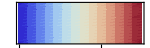
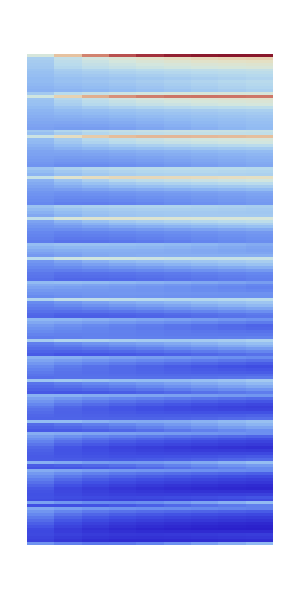
Color Code for Equity %
-Graphics-
-Graphics-

```mathematica
equityPreFlopMonteCarloLastDisplay2[equityPreFlopMonteCarloLast][[2]]
```

```mathematica
equityPreFlopMonteCarloLastDisplay2[equityPreFlopMonteCarloLast][[1]]
```

{  | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 
1 | AAo | 170.41 (0.54) | 220.31 (0.69) | 255.33 (0.89) | 279.35 (1.12) | 295.14 (1.35) | 304.78 (1.57) | 309.81 (1.77) | 311.50 (1.96) | 310.81 (2.13)
2 | AKs | 134.09 (1.65) | 152.17 (2.66) | 165.72 (3.58) | 177.03 (4.46) | 186.41 (5.31) | 193.89 (6.16) | 199.66 (7.00) | 203.90 (7.82) | 206.90 (8.63)
3 | AQs | 132.43 (1.79) | 148.26 (3.00) | 159.41 (4.13) | 168.47 (5.19) | 175.88 (6.20) | 181.80 (7.17) | 186.37 (8.10) | 189.83 (8.97) | 192.44 (9.79)
4 | AJs | 130.78 (1.99) | 144.60 (3.41) | 153.82 (4.71) | 161.21 (5.92) | 167.26 (7.06) | 172.16 (8.15) | 176.05 (9.16) | 179.13 (10.11) | 181.62 (10.98)
5 | ATs | 129.20 (2.23) | 141.20 (3.85) | 148.86 (5.29) | 155.02 (6.63) | 160.20 (7.89) | 164.49 (9.09) | 168.04 (10.22) | 170.98 (11.26) | 173.50 (12.20)
6 | A9s | 125.56 (2.54) | 133.66 (4.33) | 138.04 (5.79) | 141.61 (7.05) | 144.78 (8.21) | 147.54 (9.28) | 149.88 (10.26) | 151.91 (11.14) | 153.76 (11.91)
7 | A8s | 123.88 (2.87) | 130.53 (4.85) | 133.88 (6.42) | 136.71 (7.76) | 139.34 (8.99) | 141.73 (10.10) | 143.84 (11.11) | 145.77 (11.98) | 147.58 (12.73)
8 | A7s | 121.97 (3.19) | 127.17 (5.29) | 129.62 (6.90) | 131.96 (8.28) | 134.34 (9.54) | 136.64 (10.70) | 138.81 (11.75) | 140.83 (12.65) | 142.80 (13.40)
9 | A6s | 119.82 (3.45) | 123.49 (5.58) | 125.16 (7.16) | 127.19 (8.53) | 129.59 (9.82) | 132.08 (11.03) | 134.53 (12.11) | 136.89 (13.05) | 139.19 (13.84)
10 | A5s | 119.85 (3.72) | 124.30 (5.92) | 126.97 (7.56) | 129.95 (9.00) | 133.13 (10.36) | 136.26 (11.63) | 139.19 (12.77) | 141.93 (13.75) | 144.51 (14.56)
11 | A4s | 118.07 (3.79) | 121.57 (5.93) | 123.86 (7.47) | 126.77 (8.80) | 130.03 (10.05) | 133.30 (11.20) | 136.41 (12.22) | 139.32 (13.09) | 142.09 (13.78)
12 | A3s | 116.45 (3.77) | 119.01 (5.83) | 120.93 (7.26) | 123.75 (8.48) | 127.08 (9.60) | 130.47 (10.63) | 133.71 (11.52) | 136.75 (12.25) | 139.62 (12.83)
13 | A2s | 114.76 (3.75) | 116.32 (5.73) | 117.75 (7.06) | 120.38 (8.17) | 123.63 (9.17) | 126.97 (10.07) | 130.17 (10.84) | 133.14 (11.46) | 135.94 (11.91)
14 | KAo | 130.64 (1.70) | 144.64 (2.77) | 154.16 (3.74) | 161.56 (4.65) | 167.08 (5.53) | 170.73 (6.40) | 172.63 (7.26) | 173.00 (8.11) | 172.12 (8.93)
15 | KKo | 164.80 (0.56) | 206.61 (0.71) | 232.97 (0.93) | 248.87 (1.19) | 257.75 (1.47) | 261.97 (1.76) | 263.18 (2.05) | 262.53 (2.34) | 260.87 (2.62)
16 | KQs | 126.80 (1.98) | 141.27 (2.98) | 152.79 (3.92) | 162.38 (4.86) | 170.06 (5.80) | 175.98 (6.74) | 180.44 (7.67) | 183.77 (8.58) | 186.29 (9.46)
17 | KJs | 125.14 (2.18) | 137.64 (3.37) | 147.29 (4.46) | 155.28 (5.53) | 161.73 (6.59) | 166.76 (7.63) | 170.69 (8.66) | 173.81 (9.64) | 176.37 (10.57)
18 | KTs | 123.57 (2.40) | 134.36 (3.76) | 142.54 (4.97) | 149.37 (6.15) | 154.97 (7.32) | 159.50 (8.49) | 163.19 (9.61) | 166.28 (10.69) | 169.00 (11.69)
19 | K9s | 119.98 (2.70) | 126.91 (4.15) | 131.79 (5.31) | 135.99 (6.36) | 139.51 (7.37) | 142.38 (8.35) | 144.75 (9.27) | 146.76 (10.14) | 148.57 (10.93)
20 | K8s | 116.62 (3.04) | 120.47 (4.62) | 123.12 (5.80) | 125.77 (6.86) | 128.22 (7.89) | 130.40 (8.90) | 132.32 (9.86) | 134.07 (10.74) | 135.74 (11.54)
21 | K7s | 115.08 (3.38) | 117.81 (5.08) | 119.73 (6.32) | 121.89 (7.43) | 124.03 (8.50) | 126.03 (9.53) | 127.87 (10.49) | 129.59 (11.35) | 131.27 (12.11)
22 | K6s | 113.29 (3.67) | 114.85 (5.41) | 116.15 (6.64) | 118.04 (7.76) | 120.12 (8.85) | 122.16 (9.90) | 124.10 (10.88) | 125.97 (11.74) | 127.78 (12.49)
23 | K5s | 111.58 (3.92) | 112.17 (5.65) | 113.02 (6.87) | 114.76 (7.98) | 116.88 (9.08) | 119.05 (10.14) | 121.14 (11.12) | 123.12 (11.98) | 125.04 (12.72)
24 | K4s | 109.77 (3.99) | 109.57 (5.64) | 110.14 (6.74) | 111.86 (7.75) | 114.09 (8.73) | 116.41 (9.68) | 118.67 (10.54) | 120.85 (11.29) | 122.96 (11.91)
25 | K3s | 108.12 (3.97) | 107.13 (5.53) | 107.46 (6.53) | 109.19 (7.42) | 111.56 (8.28) | 114.08 (9.10) | 116.55 (9.84) | 118.92 (10.47) | 121.20 (10.98)
26 | K2s | 106.42 (3.94) | 104.69 (5.42) | 104.81 (6.32) | 106.61 (7.09) | 109.16 (7.84) | 111.88 (8.54) | 114.56 (9.16) | 117.13 (9.68) | 119.59 (10.09)
27 | QAo | 128.86 (1.85) | 140.43 (3.13) | 147.35 (4.32) | 152.24 (5.42) | 155.52 (6.48) | 157.29 (7.48) | 157.70 (8.43) | 156.99 (9.34) | 155.43 (10.18)
28 | QKo | 122.92 (2.05) | 133.17 (3.10) | 140.68 (4.08) | 146.38 (5.06) | 150.20 (6.04) | 152.26 (7.01) | 152.83 (7.98) | 152.29 (8.92) | 150.93 (9.83)
29 | QQo | 159.85 (0.59) | 194.79 (0.80) | 214.06 (1.08) | 223.61 (1.42) | 227.31 (1.79) | 227.69 (2.18) | 226.36 (2.57) | 224.35 (2.97) | 222.30 (3.37)
30 | QJs | 120.52 (2.38) | 132.54 (3.42) | 142.67 (4.45) | 150.95 (5.51) | 157.40 (6.58) | 162.36 (7.65) | 166.26 (8.69) | 169.46 (9.71) | 172.23 (10.70)
31 | QTs | 118.93 (2.59) | 129.31 (3.77) | 138.03 (4.90) | 145.22 (6.06) | 150.94 (7.24) | 155.50 (8.41) | 159.27 (9.57) | 162.56 (10.68) | 165.61 (11.75)
32 | Q9s | 115.33 (2.88) | 121.92 (4.11) | 127.40 (5.14) | 131.99 (6.16) | 135.64 (7.16) | 138.57 (8.15) | 141.03 (9.09) | 143.22 (9.98) | 145.31 (10.83)
33 | Q8s | 112.03 (3.20) | 115.61 (4.50) | 118.85 (5.51) | 121.86 (6.49) | 124.41 (7.47) | 126.57 (8.45) | 128.47 (9.38) | 130.27 (10.26) | 132.01 (11.07)
34 | Q7s | 108.60 (3.56) | 109.39 (4.89) | 110.80 (5.88) | 112.60 (6.87) | 114.38 (7.89) | 116.04 (8.90) | 117.64 (9.87) | 119.21 (10.77) | 120.79 (11.61)
35 | Q6s | 107.22 (3.87) | 107.15 (5.26) | 108.01 (6.28) | 109.49 (7.29) | 111.11 (8.34) | 112.72 (9.35) | 114.30 (10.31) | 115.88 (11.18) | 117.48 (11.97)
36 | Q5s | 105.54 (4.11) | 104.56 (5.47) | 105.01 (6.45) | 106.40 (7.45) | 108.09 (8.49) | 109.85 (9.51) | 111.61 (10.46) | 113.34 (11.33) | 115.04 (12.10)
37 | Q4s | 103.70 (4.19) | 102.02 (5.43) | 102.23 (6.31) | 103.60 (7.20) | 105.40 (8.12) | 107.34 (9.02) | 109.29 (9.85) | 111.22 (10.60) | 113.11 (11.27)
38 | Q3s | 102.04 (4.16) | 99.63 (5.32) | 99.59 (6.08) | 100.98 (6.85) | 102.93 (7.65) | 105.07 (8.42) | 107.22 (9.13) | 109.34 (9.76) | 111.40 (10.32)
39 | Q2s | 100.34 (4.13) | 97.24 (5.20) | 97.02 (5.86) | 98.48 (6.51) | 100.63 (7.18) | 102.98 (7.84) | 105.36 (8.44) | 107.67 (8.97) | 109.89 (9.43)
40 | JAo | 127.13 (2.06) | 136.50 (3.56) | 141.29 (4.93) | 144.29 (6.20) | 146.00 (7.39) | 146.55 (8.52) | 146.08 (9.58) | 144.79 (10.56) | 142.94 (11.46)
41 | JKo | 121.14 (2.26) | 129.27 (3.51) | 134.73 (4.65) | 138.62 (5.76) | 140.98 (6.87) | 141.95 (7.96) | 141.82 (9.03) | 140.87 (10.04) | 139.44 (11.01)
42 | JQo | 116.27 (2.46) | 124.06 (3.55) | 130.21 (4.63) | 134.62 (5.73) | 137.22 (6.85) | 138.35 (7.97) | 138.43 (9.06) | 137.84 (10.12) | 136.89 (11.15)
43 | JJo | 154.95 (0.63) | 183.51 (0.89) | 196.71 (1.24) | 201.30 (1.65) | 201.43 (2.10) | 199.54 (2.58) | 197.09 (3.08) | 194.88 (3.60) | 193.27 (4.12)
44 | JTs | 115.05 (2.75) | 125.85 (3.78) | 135.43 (4.89) | 143.14 (6.10) | 149.17 (7.35) | 154.01 (8.59) | 158.15 (9.81) | 161.92 (11.00) | 165.53 (12.16)
45 | J9s | 111.32 (3.10) | 118.41 (4.11) | 124.85 (5.10) | 130.06 (6.15) | 134.11 (7.22) | 137.41 (8.27) | 140.30 (9.28) | 143.02 (10.24) | 145.69 (11.18)
46 | J8s | 108.03 (3.41) | 112.19 (4.44) | 116.45 (5.37) | 120.09 (6.38) | 123.05 (7.42) | 125.56 (8.45) | 127.88 (9.43) | 130.14 (10.37) | 132.40 (11.27)
47 | J7s | 104.65 (3.74) | 106.06 (4.77) | 108.42 (5.65) | 110.78 (6.63) | 112.87 (7.66) | 114.76 (8.67) | 116.59 (9.65) | 118.45 (10.58) | 120.31 (11.46)
48 | J6s | 101.21 (4.06) | 100.11 (5.06) | 100.93 (5.91) | 102.35 (6.90) | 103.85 (7.96) | 105.37 (9.01) | 106.94 (10.04) | 108.55 (11.00) | 110.18 (11.91)
49 | J5s | 99.97 (4.33) | 98.20 (5.32) | 98.63 (6.18) | 99.87 (7.17) | 101.33 (8.23) | 102.89 (9.28) | 104.49 (10.28) | 106.11 (11.20) | 107.72 (12.07)
50 | J4s | 98.14 (4.40) | 95.73 (5.27) | 95.92 (6.01) | 97.15 (6.90) | 98.73 (7.84) | 100.45 (8.76) | 102.24 (9.64) | 104.05 (10.45) | 105.81 (11.21),  | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 
51 | J3s | 96.46 (4.38) | 93.39 (5.15) | 93.36 (5.78) | 94.62 (6.54) | 96.37 (7.35) | 98.29 (8.15) | 100.28 (8.91) | 102.25 (9.61) | 104.18 (10.26)
52 | J2s | 94.76 (4.35) | 91.04 (5.03) | 90.84 (5.55) | 92.19 (6.18) | 94.12 (6.87) | 96.28 (7.55) | 98.47 (8.20) | 100.64 (8.80) | 102.72 (9.35)
53 | TAo | 125.44 (2.31) | 132.87 (4.03) | 135.91 (5.55) | 137.52 (6.94) | 138.18 (8.26) | 137.97 (9.51) | 137.00 (10.69) | 135.47 (11.77) | 133.54 (12.74)
54 | TKo | 119.48 (2.49) | 125.75 (3.92) | 129.55 (5.19) | 132.12 (6.43) | 133.50 (7.66) | 133.80 (8.87) | 133.30 (10.05) | 132.23 (11.18) | 130.84 (12.22)
55 | TQo | 114.58 (2.69) | 120.61 (3.92) | 125.19 (5.10) | 128.35 (6.31) | 130.05 (7.55) | 130.63 (8.79) | 130.46 (10.00) | 129.89 (11.17) | 129.15 (12.28)
56 | TJo | 110.50 (2.84) | 117.10 (3.92) | 122.79 (5.08) | 126.68 (6.34) | 128.91 (7.65) | 129.98 (8.96) | 130.42 (10.23) | 130.59 (11.48) | 130.70 (12.69)
57 | TTo | 150.03 (0.70) | 172.73 (1.00) | 180.83 (1.40) | 181.70 (1.87) | 179.52 (2.41) | 176.55 (2.99) | 173.95 (3.61) | 172.22 (4.25) | 171.51 (4.90)
58 | T9s | 108.06 (3.30) | 116.24 (4.13) | 123.81 (5.14) | 129.72 (6.27) | 134.30 (7.43) | 138.14 (8.56) | 141.66 (9.65) | 145.07 (10.72) | 148.47 (11.78)
59 | T8s | 104.66 (3.65) | 110.01 (4.43) | 115.47 (5.37) | 119.88 (6.46) | 123.42 (7.59) | 126.55 (8.69) | 129.54 (9.76) | 132.53 (10.80) | 135.52 (11.82)
60 | T7s | 101.27 (3.97) | 103.95 (4.71) | 107.54 (5.58) | 110.65 (6.63) | 113.31 (7.72) | 115.79 (8.80) | 118.24 (9.85) | 120.73 (10.86) | 123.24 (11.85)
61 | T6s | 97.88 (4.28) | 98.05 (4.94) | 100.02 (5.76) | 102.09 (6.78) | 104.02 (7.86) | 105.95 (8.94) | 107.92 (9.98) | 109.94 (10.99) | 111.96 (11.97)
62 | T5s | 94.43 (4.56) | 92.36 (5.13) | 92.99 (5.90) | 94.30 (6.93) | 95.81 (8.04) | 97.44 (9.16) | 99.15 (10.25) | 100.87 (11.30) | 102.56 (12.31)
63 | T4s | 93.06 (4.65) | 90.56 (5.15) | 90.94 (5.85) | 92.14 (6.79) | 93.62 (7.79) | 95.27 (8.78) | 96.99 (9.73) | 98.75 (10.64) | 100.45 (11.50)
64 | T3s | 91.39 (4.63) | 88.27 (5.02) | 88.44 (5.61) | 89.66 (6.41) | 91.31 (7.29) | 93.16 (8.16) | 95.08 (8.99) | 97.00 (9.79) | 98.85 (10.56)
65 | T2s | 89.67 (4.60) | 85.96 (4.89) | 85.97 (5.36) | 87.31 (6.04) | 89.16 (6.79) | 91.22 (7.54) | 93.34 (8.27) | 95.44 (8.97) | 97.42 (9.64)
66 | 9Ao | 121.54 (2.65) | 124.74 (4.54) | 124.20 (6.08) | 122.92 (7.41) | 121.33 (8.62) | 119.37 (9.75) | 117.06 (10.77) | 114.50 (11.69) | 111.81 (12.49)
67 | 9Ko | 115.63 (2.81) | 117.72 (4.35) | 117.94 (5.56) | 117.59 (6.66) | 116.63 (7.72) | 115.06 (8.75) | 113.06 (9.72) | 110.78 (10.63) | 108.38 (11.45)
68 | 9Qo | 110.73 (3.00) | 112.65 (4.29) | 113.70 (5.37) | 113.97 (6.44) | 113.36 (7.50) | 112.09 (8.54) | 110.43 (9.53) | 108.63 (10.46) | 106.83 (11.34)
69 | 9Jo | 106.50 (3.22) | 109.09 (4.28) | 111.34 (5.31) | 112.44 (6.42) | 112.46 (7.55) | 111.78 (8.65) | 110.81 (9.72) | 109.80 (10.74) | 108.90 (11.72)
70 | 9To | 103.06 (3.43) | 106.94 (4.28) | 110.53 (5.34) | 112.54 (6.53) | 113.28 (7.76) | 113.38 (8.95) | 113.27 (10.11) | 113.22 (11.23) | 113.32 (12.33)
71 | 99o | 144.11 (0.78) | 160.80 (1.00) | 164.56 (1.30) | 162.93 (1.64) | 159.80 (2.02) | 156.99 (2.42) | 155.27 (2.84) | 154.82 (3.25) | 155.59 (3.67)
72 | 98s | 101.60 (3.89) | 107.93 (4.34) | 113.85 (5.16) | 118.21 (6.12) | 121.61 (7.05) | 124.65 (7.92) | 127.65 (8.76) | 130.71 (9.58) | 133.84 (10.40)
73 | 97s | 98.24 (4.25) | 102.23 (4.59) | 106.61 (5.34) | 110.09 (6.26) | 113.03 (7.16) | 115.85 (8.01) | 118.77 (8.84) | 121.77 (9.65) | 124.80 (10.46)
74 | 96s | 94.85 (4.56) | 96.43 (4.78) | 99.27 (5.47) | 101.74 (6.34) | 104.03 (7.22) | 106.39 (8.06) | 108.88 (8.88) | 111.46 (9.67) | 114.06 (10.46)
75 | 95s | 91.45 (4.82) | 90.73 (4.93) | 92.16 (5.55) | 93.78 (6.40) | 95.50 (7.27) | 97.38 (8.11) | 99.38 (8.92) | 101.45 (9.71) | 103.49 (10.49)
76 | 94s | 87.72 (4.91) | 85.10 (4.88) | 85.40 (5.40) | 86.37 (6.16) | 87.66 (6.96) | 89.20 (7.73) | 90.91 (8.48) | 92.66 (9.22) | 94.36 (9.95)
77 | 93s | 86.53 (4.92) | 83.48 (4.83) | 83.54 (5.28) | 84.43 (5.94) | 85.73 (6.61) | 87.31 (7.26) | 89.03 (7.87) | 90.79 (8.48) | 92.49 (9.06)
78 | 92s | 84.82 (4.88) | 81.19 (4.70) | 81.10 (5.02) | 82.09 (5.56) | 83.59 (6.11) | 85.38 (6.64) | 87.27 (7.15) | 89.18 (7.66) | 90.99 (8.16)
79 | 8Ao | 119.74 (3.00) | 121.37 (5.09) | 119.66 (6.75) | 117.56 (8.16) | 115.34 (9.43) | 112.94 (10.60) | 110.35 (11.65) | 107.64 (12.57) | 104.93 (13.34)
80 | 8Ko | 112.04 (3.18) | 110.81 (4.85) | 108.55 (6.09) | 106.47 (7.21) | 104.32 (8.30) | 101.96 (9.36) | 99.44 (10.38) | 96.85 (11.30) | 94.30 (12.14)
81 | 8Qo | 107.20 (3.34) | 105.84 (4.70) | 104.43 (5.76) | 102.94 (6.80) | 101.09 (7.85) | 98.94 (8.88) | 96.66 (9.86) | 94.39 (10.79) | 92.23 (11.64)
82 | 8Jo | 102.98 (3.55) | 102.39 (4.63) | 102.23 (5.61) | 101.57 (6.68) | 100.33 (7.78) | 98.77 (8.87) | 97.15 (9.91) | 95.64 (10.90) | 94.30 (11.85)
83 | 8To | 99.45 (3.81) | 100.26 (4.61) | 101.53 (5.60) | 101.85 (6.76) | 101.41 (7.95) | 100.68 (9.12) | 99.96 (10.25) | 99.41 (11.35) | 99.08 (12.41)
84 | 89o | 96.19 (4.06) | 98.13 (4.50) | 99.97 (5.36) | 100.34 (6.36) | 99.85 (7.34) | 99.16 (8.26) | 98.61 (9.14) | 98.34 (9.99) | 98.35 (10.84)
85 | 88o | 138.33 (0.89) | 149.86 (1.04) | 150.36 (1.30) | 147.33 (1.62) | 144.12 (1.99) | 142.10 (2.38) | 141.61 (2.80) | 142.56 (3.21) | 144.71 (3.63)
86 | 87s | 95.88 (4.51) | 101.37 (4.52) | 106.52 (5.26) | 110.39 (6.16) | 113.71 (7.02) | 116.98 (7.84) | 120.37 (8.65) | 123.87 (9.47) | 127.37 (10.30)
87 | 86s | 92.48 (4.85) | 95.85 (4.69) | 99.70 (5.36) | 102.88 (6.23) | 105.86 (7.07) | 108.98 (7.88) | 112.27 (8.68) | 115.64 (9.49) | 118.98 (10.31)
88 | 85s | 89.09 (5.11) | 90.24 (4.81) | 92.75 (5.42) | 95.10 (6.24) | 97.56 (7.05) | 100.22 (7.83) | 103.06 (8.62) | 105.93 (9.42) | 108.73 (10.23)
89 | 84s | 85.40 (5.20) | 84.57 (4.74) | 85.84 (5.21) | 87.40 (5.91) | 89.25 (6.61) | 91.39 (7.29) | 93.68 (7.98) | 96.00 (8.67) | 98.22 (9.37)
90 | 83s | 81.75 (5.18) | 79.05 (4.62) | 79.30 (5.00) | 80.28 (5.60) | 81.75 (6.23) | 83.56 (6.86) | 85.52 (7.49) | 87.48 (8.14) | 89.31 (8.80)
91 | 82s | 80.55 (5.19) | 77.46 (4.57) | 77.49 (4.86) | 78.44 (5.37) | 79.95 (5.88) | 81.80 (6.38) | 83.78 (6.89) | 85.73 (7.41) | 87.55 (7.94)
92 | 7Ao | 117.67 (3.34) | 117.70 (5.56) | 115.00 (7.25) | 112.32 (8.69) | 109.79 (10.01) | 107.28 (11.23) | 104.73 (12.32) | 102.15 (13.26) | 99.59 (14.04)
93 | 7Ko | 110.38 (3.54) | 107.92 (5.34) | 104.85 (6.64) | 102.20 (7.81) | 99.65 (8.94) | 97.08 (10.02) | 94.45 (11.03) | 91.84 (11.93) | 89.32 (12.73)
94 | 7Qo | 103.53 (3.72) | 99.17 (5.14) | 95.74 (6.18) | 92.90 (7.22) | 90.18 (8.30) | 87.48 (9.38) | 84.86 (10.41) | 82.38 (11.37) | 80.07 (12.25)
95 | 7Jo | 99.36 (3.91) | 95.78 (4.99) | 93.54 (5.92) | 91.47 (6.96) | 89.25 (8.05) | 87.01 (9.13) | 84.88 (10.17) | 82.94 (11.16) | 81.21 (12.09)
96 | 7To | 95.81 (4.16) | 93.73 (4.91) | 92.92 (5.83) | 91.81 (6.94) | 90.36 (8.11) | 88.89 (9.26) | 87.60 (10.37) | 86.54 (11.45) | 85.73 (12.49)
97 | 79o | 92.59 (4.45) | 91.99 (4.78) | 92.14 (5.56) | 91.50 (6.52) | 90.47 (7.48) | 89.51 (8.39) | 88.87 (9.26) | 88.53 (10.11) | 88.48 (10.96)
98 | 78o | 90.10 (4.72) | 91.19 (4.69) | 92.23 (5.46) | 92.09 (6.41) | 91.57 (7.32) | 91.20 (8.18) | 91.19 (9.03) | 91.53 (9.89) | 92.14 (10.76)
99 | 77o | 132.47 (1.02) | 139.42 (1.09) | 137.53 (1.31) | 133.85 (1.61) | 131.14 (1.97) | 130.18 (2.36) | 130.97 (2.77) | 133.21 (3.18) | 136.49 (3.60)
100 | 76s | 90.74 (5.08) | 95.74 (4.60) | 100.27 (5.29) | 103.89 (6.13) | 107.37 (6.92) | 111.03 (7.69) | 114.86 (8.48) | 118.76 (9.30) | 122.57 (10.16),  | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 
101 | 75s | 87.35 (5.39) | 90.36 (4.71) | 93.79 (5.33) | 96.90 (6.11) | 100.16 (6.88) | 103.69 (7.64) | 107.37 (8.43) | 111.05 (9.24) | 114.60 (10.09)
102 | 74s | 83.70 (5.48) | 84.80 (4.63) | 87.04 (5.11) | 89.37 (5.76) | 92.05 (6.40) | 95.05 (7.04) | 98.20 (7.71) | 101.35 (8.41) | 104.34 (9.14)
103 | 73s | 80.07 (5.46) | 79.22 (4.50) | 80.30 (4.84) | 81.91 (5.37) | 84.02 (5.90) | 86.48 (6.44) | 89.08 (7.02) | 91.64 (7.63) | 94.03 (8.27)
104 | 72s | 76.31 (5.43) | 73.72 (4.37) | 73.87 (4.61) | 74.96 (5.06) | 76.72 (5.52) | 78.86 (6.02) | 81.10 (6.55) | 83.25 (7.13) | 85.20 (7.72)
105 | 6Ao | 115.36 (3.62) | 113.72 (5.87) | 110.13 (7.52) | 107.08 (8.96) | 104.54 (10.30) | 102.22 (11.55) | 99.96 (12.69) | 97.76 (13.67) | 95.61 (14.49)
106 | 6Ko | 108.45 (3.85) | 104.71 (5.69) | 100.93 (6.98) | 97.94 (8.15) | 95.30 (9.30) | 92.75 (10.42) | 90.25 (11.44) | 87.81 (12.34) | 85.46 (13.12)
107 | 6Qo | 102.05 (4.05) | 96.73 (5.52) | 92.68 (6.59) | 89.46 (7.67) | 86.54 (8.78) | 83.75 (9.86) | 81.12 (10.86) | 78.67 (11.79) | 76.42 (12.61)
108 | 6Jo | 95.69 (4.26) | 89.42 (5.31) | 85.46 (6.20) | 82.33 (7.26) | 79.45 (8.39) | 76.80 (9.53) | 74.39 (10.62) | 72.23 (11.64) | 70.29 (12.60)
109 | 6To | 92.18 (4.49) | 87.38 (5.17) | 84.78 (6.03) | 82.47 (7.12) | 80.24 (8.28) | 78.18 (9.43) | 76.38 (10.55) | 74.87 (11.62) | 73.59 (12.65)
110 | 69o | 88.98 (4.77) | 85.78 (4.99) | 84.22 (5.70) | 82.47 (6.64) | 80.73 (7.58) | 79.26 (8.47) | 78.18 (9.32) | 77.43 (10.16) | 76.97 (10.99)
111 | 68o | 86.48 (5.09) | 85.27 (4.88) | 84.87 (5.58) | 83.93 (6.49) | 83.02 (7.38) | 82.48 (8.23) | 82.36 (9.08) | 82.60 (9.93) | 83.06 (10.80)
112 | 67o | 84.65 (5.34) | 85.24 (4.78) | 85.62 (5.49) | 85.24 (6.37) | 84.92 (7.21) | 85.04 (8.02) | 85.62 (8.85) | 86.52 (9.71) | 87.63 (10.61)
113 | 66o | 126.56 (1.17) | 129.58 (1.14) | 126.08 (1.32) | 122.43 (1.61) | 120.59 (1.96) | 120.86 (2.34) | 122.87 (2.74) | 126.15 (3.16) | 130.25 (3.58)
114 | 65s | 86.27 (5.57) | 90.80 (4.63) | 94.82 (5.24) | 98.44 (5.99) | 102.29 (6.71) | 106.42 (7.45) | 110.69 (8.23) | 114.91 (9.07) | 118.95 (9.95)
115 | 64s | 82.67 (5.70) | 85.50 (4.54) | 88.56 (5.01) | 91.68 (5.62) | 95.22 (6.22) | 99.11 (6.84) | 103.11 (7.51) | 107.04 (8.24) | 110.76 (9.02)
116 | 63s | 79.07 (5.70) | 79.99 (4.41) | 81.94 (4.74) | 84.35 (5.22) | 87.33 (5.69) | 90.68 (6.20) | 94.15 (6.76) | 97.51 (7.38) | 100.64 (8.04)
117 | 62s | 75.34 (5.67) | 74.43 (4.27) | 75.32 (4.47) | 77.06 (4.82) | 79.49 (5.19) | 82.30 (5.61) | 85.18 (6.09) | 87.93 (6.62) | 90.42 (7.19)
118 | 5Ao | 115.40 (3.91) | 114.58 (6.24) | 112.04 (7.95) | 109.97 (9.44) | 108.26 (10.86) | 106.62 (12.18) | 104.90 (13.37) | 103.10 (14.39) | 101.27 (15.23)
119 | 5Ko | 106.64 (4.12) | 101.84 (5.95) | 97.55 (7.22) | 94.38 (8.38) | 91.75 (9.54) | 89.32 (10.66) | 86.98 (11.69) | 84.69 (12.60) | 82.49 (13.37)
120 | 5Qo | 100.24 (4.32) | 93.92 (5.75) | 89.37 (6.78) | 86.02 (7.84) | 83.16 (8.94) | 80.54 (10.02) | 78.11 (11.03) | 75.84 (11.95) | 73.73 (12.77)
121 | 5Jo | 94.36 (4.55) | 87.33 (5.59) | 82.91 (6.49) | 79.55 (7.55) | 76.62 (8.69) | 73.99 (9.81) | 71.61 (10.87) | 69.48 (11.86) | 67.54 (12.76)
122 | 5To | 88.50 (4.79) | 81.24 (5.38) | 77.18 (6.20) | 74.04 (7.30) | 71.31 (8.50) | 68.94 (9.69) | 66.88 (10.86) | 65.11 (11.99) | 63.54 (13.05)
123 | 59o | 85.34 (5.06) | 79.66 (5.16) | 76.54 (5.81) | 73.85 (6.72) | 71.47 (7.65) | 69.49 (8.54) | 67.91 (9.40) | 66.66 (10.24) | 65.66 (11.07)
124 | 58o | 82.85 (5.37) | 79.23 (5.02) | 77.35 (5.65) | 75.52 (6.52) | 74.02 (7.39) | 73.00 (8.23) | 72.43 (9.06) | 72.18 (9.91) | 72.14 (10.76)
125 | 57o | 81.02 (5.68) | 79.46 (4.91) | 78.62 (5.54) | 77.64 (6.38) | 77.07 (7.19) | 77.04 (7.99) | 77.48 (8.82) | 78.21 (9.68) | 79.10 (10.57)
126 | 56o | 79.90 (5.86) | 80.00 (4.81) | 79.83 (5.45) | 79.45 (6.23) | 79.55 (6.99) | 80.23 (7.77) | 81.36 (8.59) | 82.75 (9.46) | 84.23 (10.37)
127 | 55o | 120.65 (1.37) | 120.18 (1.23) | 115.52 (1.37) | 112.13 (1.63) | 111.18 (1.96) | 112.45 (2.34) | 115.33 (2.74) | 119.27 (3.15) | 123.78 (3.57)
128 | 54s | 82.91 (5.84) | 87.07 (4.58) | 90.78 (5.12) | 94.59 (5.78) | 98.82 (6.46) | 103.37 (7.18) | 107.96 (7.97) | 112.42 (8.82) | 116.57 (9.71)
129 | 53s | 79.39 (5.87) | 81.85 (4.45) | 84.68 (4.85) | 88.02 (5.37) | 91.96 (5.92) | 96.24 (6.54) | 100.56 (7.22) | 104.70 (7.97) | 108.52 (8.76)
130 | 52s | 75.71 (5.84) | 76.34 (4.31) | 78.12 (4.56) | 80.79 (4.95) | 84.19 (5.39) | 87.93 (5.89) | 91.68 (6.47) | 95.23 (7.10) | 98.45 (7.78)
131 | 4Ao | 113.46 (3.99) | 111.58 (6.25) | 108.60 (7.85) | 106.44 (9.23) | 104.82 (10.52) | 103.35 (11.72) | 101.85 (12.78) | 100.29 (13.68) | 98.69 (14.40)
132 | 4Ko | 104.65 (4.20) | 98.95 (5.94) | 94.32 (7.09) | 91.09 (8.13) | 88.55 (9.17) | 86.31 (10.16) | 84.18 (11.06) | 82.12 (11.85) | 80.16 (12.50)
133 | 4Qo | 98.25 (4.41) | 91.12 (5.72) | 86.27 (6.62) | 82.85 (7.56) | 80.09 (8.54) | 77.65 (9.49) | 75.42 (10.37) | 73.39 (11.17) | 71.50 (11.86)
134 | 4Jo | 92.37 (4.63) | 84.62 (5.54) | 79.91 (6.31) | 76.50 (7.25) | 73.68 (8.26) | 71.23 (9.24) | 69.06 (10.18) | 67.14 (11.04) | 65.42 (11.83)
135 | 4To | 87.01 (4.90) | 79.28 (5.40) | 74.90 (6.15) | 71.60 (7.15) | 68.83 (8.22) | 66.47 (9.29) | 64.45 (10.31) | 62.72 (11.27) | 61.19 (12.19)
136 | 49o | 81.34 (5.17) | 73.56 (5.11) | 69.20 (5.66) | 65.75 (6.48) | 62.91 (7.33) | 60.60 (8.16) | 58.74 (8.97) | 57.21 (9.75) | 55.90 (10.51)
137 | 48o | 78.89 (5.47) | 73.12 (4.95) | 69.87 (5.45) | 67.15 (6.20) | 65.00 (6.95) | 63.43 (7.68) | 62.33 (8.40) | 61.56 (9.14) | 60.98 (9.88)
138 | 47o | 77.10 (5.78) | 73.44 (4.82) | 71.27 (5.32) | 69.45 (6.02) | 68.26 (6.70) | 67.71 (7.38) | 67.64 (8.09) | 67.86 (8.82) | 68.21 (9.60)
139 | 46o | 76.02 (6.01) | 74.27 (4.72) | 73.03 (5.21) | 72.08 (5.86) | 71.85 (6.49) | 72.29 (7.15) | 73.19 (7.85) | 74.33 (8.62) | 75.54 (9.42)
140 | 45o | 76.31 (6.16) | 76.01 (4.76) | 75.47 (5.32) | 75.26 (6.02) | 75.80 (6.73) | 76.98 (7.49) | 78.54 (8.32) | 80.28 (9.22) | 82.01 (10.15)
141 | 44o | 114.06 (1.53) | 110.27 (1.23) | 105.16 (1.24) | 102.86 (1.39) | 103.60 (1.60) | 106.58 (1.85) | 110.95 (2.12) | 116.08 (2.40) | 121.53 (2.69)
142 | 43s | 77.27 (5.83) | 79.27 (4.29) | 81.62 (4.55) | 84.67 (4.93) | 88.39 (5.35) | 92.45 (5.83) | 96.52 (6.40) | 100.37 (7.03) | 103.87 (7.71)
143 | 42s | 73.66 (5.82) | 74.04 (4.15) | 75.57 (4.27) | 78.22 (4.52) | 81.68 (4.83) | 85.48 (5.21) | 89.24 (5.68) | 92.76 (6.22) | 95.91 (6.80)
144 | 3Ao | 111.69 (3.98) | 108.76 (6.15) | 105.34 (7.63) | 103.07 (8.88) | 101.52 (10.04) | 100.19 (11.10) | 98.85 (12.02) | 97.45 (12.78) | 96.01 (13.37)
145 | 3Ko | 102.86 (4.19) | 96.26 (5.83) | 91.34 (6.86) | 88.09 (7.77) | 85.72 (8.67) | 83.70 (9.53) | 81.82 (10.30) | 80.00 (10.96) | 78.26 (11.50)
146 | 3Qo | 96.43 (4.39) | 88.49 (5.60) | 83.34 (6.38) | 79.95 (7.19) | 77.35 (8.03) | 75.15 (8.85) | 73.17 (9.60) | 71.37 (10.27) | 69.71 (10.85)
147 | 3Jo | 90.55 (4.62) | 82.03 (5.41) | 77.04 (6.06) | 73.65 (6.87) | 71.00 (7.73) | 68.78 (8.58) | 66.86 (9.39) | 65.17 (10.13) | 63.65 (10.81)
148 | 3To | 85.20 (4.88) | 76.76 (5.27) | 72.11 (5.88) | 68.83 (6.75) | 66.23 (7.69) | 64.09 (8.61) | 62.31 (9.50) | 60.79 (10.36) | 59.44 (11.16)
149 | 39o | 80.03 (5.18) | 71.75 (5.06) | 67.07 (5.53) | 63.53 (6.24) | 60.69 (6.97) | 58.42 (7.66) | 56.60 (8.31) | 55.12 (8.95) | 53.84 (9.57)
150 | 38o | 74.97 (5.47) | 67.16 (4.84) | 62.76 (5.23) | 59.39 (5.88) | 56.84 (6.56) | 54.95 (7.23) | 53.53 (7.91) | 52.42 (8.60) | 51.48 (9.29)
151 | 37o | 73.20 (5.77) | 67.41 (4.70) | 63.98 (5.06) | 61.35 (5.62) | 59.55 (6.19) | 58.44 (6.77) | 57.80 (7.37) | 57.45 (8.01) | 57.21 (8.68)
152 | 36o | 72.15 (6.02) | 68.31 (4.59) | 65.83 (4.94) | 64.10 (5.44) | 63.28 (5.94) | 63.18 (6.48) | 63.53 (7.08) | 64.12 (7.72) | 64.76 (8.41)
153 | 35o | 72.53 (6.20) | 70.37 (4.63) | 68.85 (5.04) | 68.13 (5.60) | 68.36 (6.18) | 69.29 (6.83) | 70.60 (7.55) | 72.05 (8.33) | 73.48 (9.16)
154 | 34o | 70.29 (6.16) | 67.64 (4.46) | 65.59 (4.72) | 64.56 (5.13) | 64.57 (5.57) | 65.27 (6.08) | 66.33 (6.68) | 67.51 (7.34) | 68.64 (8.04)
155 | 33o | 107.39 (1.71) | 100.86 (1.23) | 95.89 (1.12) | 95.06 (1.15) | 97.56 (1.24) | 102.15 (1.36) | 107.81 (1.50) | 113.92 (1.66) | 120.07 (1.81)
156 | 32s | 71.97 (5.78) | 71.51 (3.99) | 72.63 (3.97) | 75.06 (4.08) | 78.35 (4.25) | 81.96 (4.51) | 85.51 (4.86) | 88.78 (5.29) | 91.66 (5.76)
157 | 2Ao | 109.86 (3.96) | 105.79 (6.04) | 101.82 (7.41) | 99.33 (8.54) | 97.70 (9.57) | 96.34 (10.49) | 94.99 (11.28) | 93.55 (11.91) | 92.04 (12.37)
158 | 2Ko | 101.01 (4.17) | 93.58 (5.71) | 88.39 (6.63) | 85.21 (7.42) | 83.05 (8.19) | 81.27 (8.92) | 79.64 (9.57) | 78.07 (10.11) | 76.54 (10.54)
159 | 2Qo | 94.60 (4.37) | 85.88 (5.48) | 80.51 (6.14) | 77.16 (6.82) | 74.76 (7.53) | 72.80 (8.22) | 71.09 (8.84) | 69.51 (9.40) | 68.05 (9.87)
160 | 2Jo | 88.70 (4.60) | 79.46 (5.29) | 74.24 (5.82) | 70.92 (6.48) | 68.49 (7.22) | 66.52 (7.95) | 64.85 (8.63) | 63.38 (9.26) | 62.05 (9.84)
161 | 2To | 83.34 (4.86) | 74.21 (5.14) | 69.35 (5.63) | 66.16 (6.36) | 63.77 (7.16) | 61.89 (7.96) | 60.35 (8.73) | 59.04 (9.47) | 57.87 (10.18)
162 | 29o | 78.19 (5.16) | 69.26 (4.93) | 64.39 (5.26) | 60.93 (5.83) | 58.30 (6.42) | 56.27 (6.99) | 54.67 (7.53) | 53.36 (8.06) | 52.24 (8.58)
163 | 28o | 73.65 (5.48) | 65.37 (4.79) | 60.72 (5.09) | 57.31 (5.63) | 54.79 (6.19) | 52.95 (6.73) | 51.57 (7.27) | 50.49 (7.81) | 49.55 (8.37)
164 | 27o | 69.16 (5.74) | 61.47 (4.57) | 57.00 (4.82) | 53.80 (5.31) | 51.63 (5.81) | 50.21 (6.34) | 49.24 (6.91) | 48.51 (7.51) | 47.87 (8.13)
165 | 26o | 68.16 (5.99) | 62.31 (4.45) | 58.66 (4.66) | 56.20 (5.04) | 54.81 (5.44) | 54.16 (5.88) | 53.95 (6.38) | 53.93 (6.94) | 53.96 (7.53)
166 | 25o | 68.57 (6.18) | 64.42 (4.49) | 61.74 (4.76) | 60.30 (5.17) | 59.97 (5.64) | 60.36 (6.17) | 61.11 (6.78) | 61.97 (7.45) | 62.81 (8.16)
167 | 24o | 66.40 (6.16) | 61.98 (4.32) | 59.04 (4.44) | 57.59 (4.70) | 57.33 (5.03) | 57.81 (5.43) | 58.62 (5.92) | 59.51 (6.48) | 60.32 (7.09)
168 | 23o | 64.61 (6.13) | 59.27 (4.16) | 55.86 (4.12) | 54.14 (4.23) | 53.69 (4.41) | 53.96 (4.69) | 54.53 (5.05) | 55.15 (5.49) | 55.67 (5.97)
169 | 22o | 100.66 (1.90) | 91.97 (1.24) | 87.71 (1.01) | 88.64 (0.92) | 92.94 (0.89) | 99.01 (0.89) | 105.78 (0.91) | 112.66 (0.94) | 119.34 (0.97)}

```mathematica
k=1;
name="monteCarloPreFlopEquityTimesBet"<>ToString[k];
repoDir=FileNameJoin[{$InitialDirectory,"Dropbox","Archives","GitHub","Poker"}];
Export[FileNameJoin[{repoDir,"Pictures",name<>".png"}],equityPreFlopMonteCarloLastDisplay2[equityPreFlopMonteCarloLast][[1,k]],"PNG",ImageSize->Automatic];
k=2;
name="monteCarloPreFlopEquityTimesBet"<>ToString[k];
repoDir=FileNameJoin[{$InitialDirectory,"Dropbox","Archives","GitHub","Poker"}];
Export[FileNameJoin[{repoDir,"Pictures",name<>".png"}],equityPreFlopMonteCarloLastDisplay2[equityPreFlopMonteCarloLast][[1,k]],"PNG",ImageSize->Automatic];
k=3;
name="monteCarloPreFlopEquityTimesBet"<>ToString[k];
repoDir=FileNameJoin[{$InitialDirectory,"Dropbox","Archives","GitHub","Poker"}];
Export[FileNameJoin[{repoDir,"Pictures",name<>".png"}],equityPreFlopMonteCarloLastDisplay2[equityPreFlopMonteCarloLast][[1,k]],"PNG",ImageSize->Automatic];
```

```mathematica
SetDirectory[FileNameJoin[{repoDir,"Tables"}]];
Export[
"monteCarloPreFlopEquityTimesBet.xlsx",
"Sheets"->{
"equityWin"->equityPreFlopMonteCarloLastDisplay2[equityPreFlopMonteCarloLast][[4]],
"equityTie"->equityPreFlopMonteCarloLastDisplay2[equityPreFlopMonteCarloLast][[5]],
"handList"->allPreFlopHandList
},
"Rules"
];
```

```mathematica
tableBestPreFlopHand[eqtyTotal_]:=Module[{table, bestHand=Table[0,{9}],gridAll},
Do[table=Table[{allPreFlopHandList[[k]],eqtyTotal[[k,i]],(1+i)*eqtyTotal[[k,i]]},{k,Length[eqtyTotal]}];
bestHand[[i]]=Reverse[SortBy[table,Last]];
,{i,9}];
gridAll=Map[Text@Row[{#[[1]],"  ",NumberForm[100*#[[2]],{4,2}],"  ",NumberForm[100*#[[3]],{5,2}]}]&,bestHand,{2}];
gridAll=Prepend[gridAll,Table[Text[i],{i,169}]];
gridAll=Prepend[Transpose[gridAll],Prepend[Table[Text@Style[i,Bold],{i,9}],""]];
{{Grid[Prepend[Take[gridAll,2;;51],Prepend[Table[Text@Style[i,Bold],{i,9}]," "]],
Dividers->{{False,{True}},{2->Black}},
Background->{None,{{None,LightRed}}}
],
Grid[Prepend[Take[gridAll,52;;101],Prepend[Table[Text@Style[i,Bold],{i,9}]," "]],
Dividers->{{False,{True}},{2->Black}},
Background->{None,{{None,LightRed}}}
],
Grid[Prepend[Take[gridAll,102;;170],Prepend[Table[Text@Style[i,Bold],{i,9}]," "]],
Dividers->{{False,{True}},{2->Black}},
Background->{None,{{None,LightRed}}}
]
},
Transpose[bestHand]}
];
```

```mathematica
tableBestPreFlopHand[equityPreFlopMonteCarloLastDisplay[equityPreFlopMonteCarloLast][[6]]][[1]]
```

{  | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
1 | AAo  85.20  170.41 | AAo  73.44  220.31 | AAo  63.83  255.33 | AAo  55.87  279.35 | AAo  49.19  295.14 | AAo  43.54  304.78 | AAo  38.73  309.81 | AAo  34.61  311.50 | AAo  31.08  310.81
2 | KKo  82.40  164.80 | KKo  68.87  206.61 | KKo  58.24  232.97 | KKo  49.77  248.87 | KKo  42.96  257.75 | KKo  37.42  261.97 | KKo  32.90  263.18 | KKo  29.17  262.53 | KKo  26.09  260.87
3 | QQo  79.93  159.85 | QQo  64.93  194.79 | QQo  53.51  214.06 | QQo  44.72  223.61 | QQo  37.88  227.31 | QQo  32.53  227.69 | QQo  28.30  226.36 | QQo  24.93  224.35 | QQo  22.23  222.30
4 | JJo  77.47  154.95 | JJo  61.17  183.51 | JJo  49.18  196.71 | JJo  40.26  201.30 | JJo  33.57  201.43 | JJo  28.51  199.54 | AKs  24.96  199.66 | AKs  22.66  203.90 | AKs  20.69  206.90
5 | TTo  75.02  150.03 | TTo  57.58  172.73 | TTo  45.21  180.83 | TTo  36.34  181.70 | AKs  31.07  186.41 | AKs  27.70  193.89 | JJo  24.64  197.09 | JJo  21.65  194.88 | JJo  19.33  193.27
6 | 99o  72.06  144.11 | 99o  53.60  160.80 | AKs  41.43  165.72 | AKs  35.41  177.03 | TTo  29.92  179.52 | AQs  25.97  181.80 | AQs  23.30  186.37 | AQs  21.09  189.83 | AQs  19.24  192.44
7 | 88o  69.16  138.33 | AKs  50.72  152.17 | 99o  41.14  164.56 | AQs  33.69  168.47 | AQs  29.31  175.88 | TTo  25.22  176.55 | KQs  22.56  180.44 | KQs  20.42  183.77 | KQs  18.63  186.29
8 | AKs  67.05  134.09 | 88o  49.95  149.86 | AQs  39.85  159.41 | 99o  32.59  162.93 | KQs  28.34  170.06 | KQs  25.14  175.98 | AJs  22.01  176.05 | AJs  19.90  179.13 | AJs  18.16  181.62
9 | 77o  66.24  132.47 | AQs  49.42  148.26 | KAo  38.54  154.16 | KQs  32.48  162.38 | AJs  27.88  167.26 | AJs  24.59  172.16 | TTo  21.74  173.95 | KJs  19.31  173.81 | KJs  17.64  176.37
10 | AQs  66.21  132.43 | KAo  48.21  144.64 | AJs  38.46  153.82 | KAo  32.31  161.56 | KAo  27.85  167.08 | KAo  24.39  170.73 | KAo  21.58  172.63 | KAo  19.22  173.00 | ATs  17.35  173.50
11 | AJs  65.39  130.78 | AJs  48.20  144.60 | KQs  38.20  152.79 | AJs  32.24  161.21 | KJs  26.95  161.73 | KJs  23.82  166.76 | KJs  21.34  170.69 | TTo  19.14  172.22 | QJs  17.22  172.23
12 | KAo  65.32  130.64 | KQs  47.09  141.27 | 88o  37.59  150.36 | KJs  31.06  155.28 | ATs  26.70  160.20 | ATs  23.50  164.49 | ATs  21.00  168.04 | ATs  19.00  170.98 | KAo  17.21  172.12
13 | ATs  64.60  129.20 | ATs  47.07  141.20 | ATs  37.21  148.86 | ATs  31.00  155.02 | 99o  26.63  159.80 | QJs  23.19  162.36 | QJs  20.78  166.26 | QJs  18.83  169.46 | TTo  17.15  171.51
14 | QAo  64.43  128.86 | QAo  46.81  140.43 | QAo  36.84  147.35 | QAo  30.45  152.24 | QJs  26.23  157.40 | KTs  22.79  159.50 | KTs  20.40  163.19 | KTs  18.48  166.28 | KTs  16.90  169.00
15 | JAo  63.57  127.13 | 77o  46.47  139.42 | KJs  36.82  147.29 | QJs  30.19  150.95 | QAo  25.92  155.52 | QAo  22.47  157.29 | QTs  19.91  159.27 | QTs  18.06  162.56 | QTs  16.56  165.61
16 | KQs  63.40  126.80 | KJs  45.88  137.64 | QJs  35.67  142.67 | KTs  29.87  149.37 | KTs  25.83  154.97 | 99o  22.43  156.99 | JTs  19.77  158.15 | JTs  17.99  161.92 | JTs  16.55  165.53
17 | 66o  63.28  126.56 | JAo  45.50  136.50 | KTs  35.63  142.54 | 88o  29.47  147.33 | QTs  25.16  150.94 | QTs  22.21  155.50 | QAo  19.71  157.70 | QAo  17.44  156.99 | 99o  15.56  155.59
18 | A9s  62.78  125.56 | KTs  44.79  134.36 | JAo  35.32  141.29 | QKo  29.28  146.38 | QKo  25.03  150.20 | JTs  22.00  154.01 | 99o  19.41  155.27 | 99o  17.20  154.82 | QAo  15.54  155.43
19 | TAo  62.72  125.44 | A9s  44.55  133.66 | QKo  35.17  140.68 | QTs  29.04  145.22 | JTs  24.86  149.17 | QKo  21.75  152.26 | QKo  19.10  152.83 | QKo  16.92  152.29 | A9s  15.38  153.76
20 | KJs  62.57  125.14 | QKo  44.39  133.17 | A9s  34.51  138.04 | JAo  28.86  144.29 | JAo  24.33  146.00 | A9s  21.08  147.54 | A9s  18.74  149.88 | A9s  16.88  151.91 | QKo  15.09  150.93
21 | A8s  61.94  123.88 | TAo  44.29  132.87 | QTs  34.51  138.03 | JTs  28.63  143.14 | A9s  24.13  144.78 | JAo  20.94  146.55 | JAo  18.26  146.08 | K9s  16.31  146.76 | K9s  14.86  148.57
22 | KTs  61.79  123.57 | QJs  44.18  132.54 | 77o  34.38  137.53 | A9s  28.32  141.61 | 88o  24.02  144.12 | K9s  20.34  142.38 | K9s  18.09  144.75 | A8s  16.20  145.77 | T9s  14.85  148.47
23 | QKo  61.46  122.92 | A8s  43.51  130.53 | TAo  33.98  135.91 | JKo  27.72  138.62 | JKo  23.50  140.98 | 88o  20.30  142.10 | A8s  17.98  143.84 | T9s  16.12  145.07 | A8s  14.76  147.58
24 | A7s  60.99  121.97 | 66o  43.19  129.58 | JTs  33.86  135.43 | TAo  27.50  137.52 | K9s  23.25  139.51 | JKo  20.28  141.95 | JKo  17.73  141.82 | JAo  16.09  144.79 | J9s  14.57  145.69
25 | 9Ao  60.77  121.54 | QTs  43.10  129.31 | JKo  33.68  134.73 | A8s  27.34  136.71 | A8s  23.22  139.34 | A8s  20.25  141.73 | T9s  17.71  141.66 | Q9s  15.91  143.22 | Q9s  14.53  145.31
26 | JKo  60.57  121.14 | JKo  43.09  129.27 | A8s  33.47  133.88 | K9s  27.20  135.99 | TAo  23.03  138.18 | Q9s  19.80  138.57 | 88o  17.70  141.61 | J9s  15.89  143.02 | 88o  14.47  144.71
27 | 55o  60.33  120.65 | A7s  42.39  127.17 | K9s  32.95  131.79 | JQo  26.92  134.62 | JQo  22.87  137.22 | JQo  19.76  138.35 | Q9s  17.63  141.03 | 88o  15.84  142.56 | A5s  14.45  144.51
28 | QJs  60.26  120.52 | K9s  42.30  126.91 | JQo  32.55  130.21 | 77o  26.77  133.85 | Q9s  22.61  135.64 | T9s  19.73  138.14 | J9s  17.54  140.30 | A5s  15.77  141.93 | JAo  14.29  142.94
29 | K9s  59.99  119.98 | JTs  41.95  125.85 | A7s  32.41  129.62 | TKo  26.42  132.12 | A7s  22.39  134.34 | TAo  19.71  137.97 | A5s  17.40  139.19 | JKo  15.65  140.87 | A7s  14.28  142.80
30 | A5s  59.92  119.85 | TKo  41.92  125.75 | TKo  32.39  129.55 | Q9s  26.40  131.99 | T9s  22.38  134.30 | J9s  19.63  137.41 | A7s  17.35  138.81 | A7s  15.65  140.83 | A4s  14.21  142.09
31 | A6s  59.91  119.82 | 9Ao  41.58  124.74 | Q9s  31.85  127.40 | A7s  26.39  131.96 | J9s  22.35  134.11 | A7s  19.52  136.64 | JQo  17.30  138.43 | A4s  15.48  139.32 | A3s  13.96  139.62
32 | 8Ao  59.87  119.74 | A5s  41.43  124.30 | A5s  31.74  126.97 | J9s  26.01  130.06 | TKo  22.25  133.50 | A5s  19.47  136.26 | TAo  17.13  137.00 | JQo  15.32  137.84 | JKo  13.94  139.44
33 | TKo  59.74  119.48 | JQo  41.35  124.06 | 66o  31.52  126.08 | A5s  25.99  129.95 | A5s  22.19  133.13 | TKo  19.11  133.80 | A4s  17.05  136.41 | A6s  15.21  136.89 | A6s  13.92  139.19
34 | QTs  59.46  118.93 | A6s  41.16  123.49 | TQo  31.30  125.19 | T9s  25.94  129.72 | 77o  21.86  131.14 | A4s  19.04  133.30 | A6s  16.82  134.53 | A3s  15.19  136.75 | JQo  13.69  136.89
35 | A4s  59.03  118.07 | Q9s  40.64  121.92 | A6s  31.29  125.16 | TQo  25.67  128.35 | TQo  21.68  130.05 | A6s  18.87  132.08 | A3s  16.71  133.71 | TAo  15.05  135.47 | 77o  13.65  136.49
36 | 7Ao  58.84  117.67 | A4s  40.52  121.57 | J9s  31.21  124.85 | A6s  25.44  127.19 | A4s  21.67  130.03 | TQo  18.66  130.63 | TKo  16.66  133.30 | K8s  14.90  134.07 | A2s  13.59  135.94
37 | K8s  58.31  116.62 | 8Ao  40.46  121.37 | 9Ao  31.05  124.20 | A4s  25.35  126.77 | A6s  21.60  129.59 | A3s  18.64  130.47 | K8s  16.54  132.32 | 77o  14.80  133.21 | K8s  13.57  135.74
38 | A3s  58.22  116.45 | TQo  40.20  120.61 | A4s  30.97  123.86 | TJo  25.34  126.68 | TJo  21.48  128.91 | K8s  18.63  130.40 | 77o  16.37  130.97 | A2s  14.79  133.14 | T8s  13.55  135.52
39 | JQo  58.13  116.27 | K8s  40.16  120.47 | T9s  30.95  123.81 | K8s  25.15  125.77 | K8s  21.37  128.22 | 77o  18.60  130.18 | TQo  16.31  130.46 | T8s  14.73  132.53 | 98s  13.38  133.84
40 | 9Ko  57.81  115.63 | 55o  40.06  120.18 | K8s  30.78  123.12 | A3s  24.75  123.75 | A3s  21.18  127.08 | TJo  18.57  129.98 | TJo  16.30  130.42 | TKo  14.69  132.23 | TAo  13.35  133.54
41 | 5Ao  57.70  115.40 | A3s  39.67  119.01 | TJo  30.70  122.79 | 9Ao  24.58  122.92 | Q8s  20.74  124.41 | A2s  18.14  126.97 | A2s  16.27  130.17 | 98s  14.52  130.71 | J8s  13.24  132.40
42 | 6Ao  57.68  115.36 | J9s  39.47  118.41 | A3s  30.23  120.93 | 66o  24.49  122.43 | K7s  20.67  124.03 | Q8s  18.08  126.57 | T8s  16.19  129.54 | TJo  14.51  130.59 | Q8s  13.20  132.01
43 | Q9s  57.66  115.33 | K7s  39.27  117.81 | K7s  29.93  119.73 | K7s  24.38  121.89 | A2s  20.60  123.63 | T8s  18.08  126.55 | Q8s  16.06  128.47 | Q8s  14.47  130.27 | K7s  13.13  131.27
44 | K7s  57.54  115.08 | 9Ko  39.24  117.72 | 8Ao  29.92  119.66 | Q8s  24.37  121.86 | T8s  20.57  123.42 | K7s  18.00  126.03 | J8s  15.98  127.88 | J8s  14.46  130.14 | TKo  13.08  130.84
45 | JTs  57.53  115.05 | 7Ao  39.23  117.70 | Q8s  29.71  118.85 | A2s  24.08  120.38 | J8s  20.51  123.05 | J8s  17.94  125.56 | K7s  15.98  127.87 | TQo  14.43  129.89 | TJo  13.07  130.70
46 | A2s  57.38  114.76 | TJo  39.03  117.10 | 9Ko  29.48  117.94 | J8s  24.02  120.09 | 98s  20.27  121.61 | 98s  17.81  124.65 | 98s  15.96  127.65 | K7s  14.40  129.59 | 66o  13.02  130.25
47 | TQo  57.29  114.58 | A2s  38.77  116.32 | A2s  29.44  117.75 | T8s  23.98  119.88 | 9Ao  20.22  121.33 | K6s  17.45  122.16 | K6s  15.51  124.10 | 66o  14.02  126.15 | TQo  12.92  129.15
48 | 44o  57.03  114.06 | T9s  38.75  116.24 | J8s  29.11  116.45 | 98s  23.64  118.21 | 66o  20.10  120.59 | 66o  17.27  120.86 | 66o  15.36  122.87 | K6s  14.00  125.97 | K6s  12.78  127.78
49 | 4Ao  56.73  113.46 | Q8s  38.54  115.61 | K6s  29.04  116.15 | K6s  23.61  118.04 | K6s  20.02  120.12 | 9Ao  17.05  119.37 | K5s  15.14  121.14 | 87s  13.76  123.87 | 87s  12.74  127.37
50 | K6s  56.64  113.29 | K6s  38.28  114.85 | 55o  28.88  115.52 | 9Ko  23.52  117.59 | K5s  19.48  116.88 | K5s  17.01  119.05 | 87s  15.05  120.37 | K5s  13.68  123.12 | K5s  12.50  125.04,  | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
51 | 8Ko  56.02  112.04 | 5Ao  38.19  114.58 | T8s  28.87  115.47 | 8Ao  23.51  117.56 | 9Ko  19.44  116.63 | 87s  16.71  116.98 | 97s  14.85  118.77 | 97s  13.53  121.77 | 97s  12.48  124.80
52 | Q8s  56.02  112.03 | 6Ao  37.91  113.72 | 7Ao  28.75  115.00 | K5s  22.95  114.76 | 8Ao  19.22  115.34 | K4s  16.63  116.41 | K4s  14.83  118.67 | K4s  13.43  120.85 | 55o  12.38  123.78
53 | 3Ao  55.85  111.69 | 9Qo  37.55  112.65 | 98s  28.46  113.85 | 9Qo  22.79  113.97 | Q7s  19.06  114.38 | Q7s  16.58  116.04 | T7s  14.78  118.24 | T7s  13.41  120.73 | T7s  12.32  123.24
54 | K5s  55.79  111.58 | J8s  37.40  112.19 | 9Qo  28.43  113.70 | Q7s  22.52  112.60 | K4s  19.01  114.09 | 97s  16.55  115.85 | Q7s  14.70  117.64 | 55o  13.25  119.27 | K4s  12.30  122.96
55 | J9s  55.66  111.32 | K5s  37.39  112.17 | K5s  28.26  113.02 | 9To  22.51  112.54 | 87s  18.95  113.71 | T7s  16.54  115.79 | 9Ao  14.63  117.06 | Q7s  13.25  119.21 | 76s  12.26  122.57
56 | 9Qo  55.36  110.73 | 4Ao  37.19  111.58 | 5Ao  28.01  112.04 | 9Jo  22.49  112.44 | 9Qo  18.89  113.36 | 9Ko  16.44  115.06 | J7s  14.57  116.59 | K3s  13.21  118.92 | 44o  12.15  121.53
57 | TJo  55.25  110.50 | 8Ko  36.94  110.81 | 9Jo  27.83  111.34 | 7Ao  22.46  112.32 | T7s  18.89  113.31 | J7s  16.39  114.76 | K3s  14.57  116.55 | 76s  13.20  118.76 | K3s  12.12  121.20
58 | 7Ko  55.19  110.38 | 44o  36.76  110.27 | Q7s  27.70  110.80 | 55o  22.43  112.13 | 9To  18.88  113.28 | K3s  16.30  114.08 | 55o  14.42  115.33 | J7s  13.16  118.45 | Q7s  12.08  120.79
59 | 2Ao  54.93  109.86 | T8s  36.67  110.01 | 9To  27.63  110.53 | K4s  22.37  111.86 | 97s  18.84  113.03 | 9To  16.20  113.38 | 76s  14.36  114.86 | K2s  13.01  117.13 | J7s  12.03  120.31
60 | K4s  54.89  109.77 | K4s  36.52  109.57 | K4s  27.53  110.14 | J7s  22.16  110.78 | J7s  18.81  112.87 | 8Ao  16.13  112.94 | K2s  14.32  114.56 | 44o  12.90  116.08 | 33o  12.01  120.07
61 | Q7s  54.30  108.60 | Q7s  36.46  109.39 | 6Ao  27.53  110.13 | T7s  22.13  110.65 | 9Jo  18.74  112.46 | Q6s  16.10  112.72 | Q6s  14.29  114.30 | Q6s  12.88  115.88 | K2s  11.96  119.59
62 | 6Ko  54.22  108.45 | 9Jo  36.36  109.09 | 4Ao  27.15  108.60 | 87s  22.08  110.39 | K3s  18.59  111.56 | 55o  16.06  112.45 | 9To  14.16  113.27 | 86s  12.85  115.64 | 22o  11.93  119.34
63 | K3s  54.06  108.12 | 3Ao  36.25  108.76 | 8Ko  27.14  108.55 | 97s  22.02  110.09 | 55o  18.53  111.18 | 9Qo  16.01  112.09 | 9Ko  14.13  113.06 | 65s  12.77  114.91 | 86s  11.90  118.98
64 | T9s  54.03  108.06 | 98s  35.98  107.93 | J7s  27.11  108.42 | 5Ao  21.99  109.97 | Q6s  18.52  111.11 | K2s  15.98  111.88 | 86s  14.03  112.27 | 9Ao  12.72  114.50 | 65s  11.89  118.95
65 | J8s  54.02  108.03 | 7Ko  35.97  107.92 | Q6s  27.00  108.01 | Q6s  21.90  109.49 | 7Ao  18.30  109.79 | 9Jo  15.97  111.78 | Q5s  13.95  111.61 | 33o  12.66  113.92 | Q6s  11.75  117.48
66 | 33o  53.69  107.39 | Q6s  35.72  107.15 | T7s  26.89  107.54 | K3s  21.84  109.19 | K2s  18.19  109.16 | 76s  15.86  111.03 | 44o  13.87  110.95 | Q5s  12.59  113.34 | 54s  11.66  116.57
67 | Q6s  53.61  107.22 | K3s  35.71  107.13 | K3s  26.86  107.46 | 6Ao  21.42  107.08 | 5Ao  18.04  108.26 | Q5s  15.69  109.85 | 9Jo  13.85  110.81 | 9To  12.58  113.22 | Q5s  11.50  115.04
68 | 8Qo  53.60  107.20 | 9To  35.65  106.94 | 97s  26.65  106.61 | K2s  21.32  106.61 | Q5s  18.01  108.09 | 86s  15.57  108.98 | 65s  13.84  110.69 | 22o  12.52  112.66 | 75s  11.46  114.60
69 | 5Ko  53.32  106.64 | J7s  35.35  106.06 | 87s  26.63  106.52 | 8Ko  21.29  106.47 | 76s  17.90  107.37 | Q4s  15.33  107.34 | 9Qo  13.80  110.43 | 54s  12.49  112.42 | 96s  11.41  114.06
70 | 9Jo  53.25  106.50 | 8Qo  35.28  105.84 | 3Ao  26.33  105.34 | 4Ao  21.29  106.44 | 86s  17.64  105.86 | 7Ao  15.33  107.28 | 8Ao  13.79  110.35 | 96s  12.38  111.46 | 9To  11.33  113.32
71 | K2s  53.21  106.42 | 2Ao  35.26  105.79 | 44o  26.29  105.16 | Q5s  21.28  106.40 | Q4s  17.57  105.40 | 5Ao  15.23  106.62 | Q4s  13.66  109.29 | Q4s  12.36  111.22 | Q4s  11.31  113.11
72 | Q5s  52.77  105.54 | 6Ko  34.90  104.71 | Q5s  26.25  105.01 | 76s  20.78  103.89 | 4Ao  17.47  104.82 | 44o  15.23  106.58 | 96s  13.61  108.88 | 75s  12.34  111.05 | T6s  11.20  111.96
73 | T8s  52.33  104.66 | K2s  34.90  104.69 | 7Ko  26.21  104.85 | Q4s  20.72  103.60 | 6Ao  17.42  104.54 | 65s  15.20  106.42 | 54s  13.50  107.96 | 9Ko  12.31  110.78 | 9Ao  11.18  111.81
74 | 4Ko  52.33  104.65 | Q5s  34.85  104.56 | K2s  26.20  104.81 | 3Ao  20.61  103.07 | 8Ko  17.39  104.32 | 96s  15.20  106.39 | T6s  13.49  107.92 | T6s  12.22  109.94 | Q3s  11.14  111.40
75 | J7s  52.33  104.65 | T7s  34.65  103.95 | 8Qo  26.11  104.43 | 8Qo  20.59  102.94 | 96s  17.34  104.03 | T6s  15.14  105.95 | 33o  13.48  107.81 | 9Jo  12.20  109.80 | 64s  11.08  110.76
76 | Q4s  51.85  103.70 | 8Jo  34.13  102.39 | Q4s  25.56  102.23 | 86s  20.58  102.88 | T6s  17.34  104.02 | J6s  15.05  105.37 | 75s  13.42  107.37 | Q3s  12.15  109.34 | J6s  11.02  110.18
77 | 7Qo  51.77  103.53 | 97s  34.08  102.23 | 8Jo  25.56  102.23 | 44o  20.57  102.86 | J6s  17.31  103.85 | Q3s  15.01  105.07 | Q3s  13.40  107.22 | 9Qo  12.07  108.63 | Q2s  10.99  109.89
78 | 9To  51.53  103.06 | Q4s  34.01  102.02 | 2Ao  25.45  101.82 | J6s  20.47  102.35 | 44o  17.27  103.60 | 75s  14.81  103.69 | J6s  13.37  106.94 | J6s  12.06  108.55 | 9Jo  10.89  108.90
79 | 8Jo  51.49  102.98 | 5Ko  33.95  101.84 | 8To  25.38  101.53 | 7Ko  20.44  102.20 | Q3s  17.16  102.93 | 54s  14.77  103.37 | 22o  13.22  105.78 | Q2s  11.96  107.67 | 85s  10.87  108.73
80 | 3Ko  51.43  102.86 | 87s  33.79  101.37 | 6Ko  25.23  100.93 | T6s  20.42  102.09 | 65s  17.05  102.29 | 4Ao  14.76  103.35 | Q2s  13.17  105.36 | 8Ao  11.96  107.64 | 53s  10.85  108.52
81 | 6Qo  51.02  102.05 | 33o  33.62  100.86 | J6s  25.23  100.93 | 8To  20.37  101.85 | 3Ao  16.92  101.52 | Q2s  14.71  102.98 | 5Ao  13.11  104.90 | 64s  11.89  107.04 | 9Ko  10.84  108.38
82 | Q3s  51.02  102.04 | 8To  33.42  100.26 | 76s  25.07  100.27 | 96s  20.35  101.74 | 8To  16.90  101.41 | J5s  14.70  102.89 | 7Ao  13.09  104.73 | J5s  11.79  106.11 | J5s  10.77  107.72
83 | 98s  50.80  101.60 | J6s  33.37  100.11 | T6s  25.01  100.02 | 8Jo  20.31  101.57 | J5s  16.89  101.33 | 6Ao  14.60  102.22 | J5s  13.06  104.49 | 85s  11.77  105.93 | 9Qo  10.68  106.83
84 | T7s  50.63  101.27 | Q3s  33.21  99.63 | 89o  24.99  99.97 | Q3s  20.20  100.98 | 8Qo  16.85  101.09 | 33o  14.59  102.15 | 64s  12.89  103.11 | 53s  11.63  104.70 | J4s  10.58  105.81
85 | J6s  50.61  101.21 | 7Qo  33.06  99.17 | 86s  24.93  99.70 | 89o  20.07  100.34 | Q2s  16.77  100.63 | 8Ko  14.57  101.96 | 85s  12.88  103.06 | J4s  11.56  104.05 | 8Ao  10.49  104.93
86 | 2Ko  50.51  101.01 | 4Ko  32.98  98.95 | Q3s  24.90  99.59 | J5s  19.97  99.87 | 8Jo  16.72  100.33 | 8To  14.38  100.68 | J4s  12.78  102.24 | 5Ao  11.46  103.10 | 74s  10.43  104.34
87 | 22o  50.33  100.66 | J5s  32.73  98.20 | 96s  24.82  99.27 | 2Ao  19.87  99.33 | 75s  16.69  100.16 | J4s  14.35  100.45 | 4Ao  12.73  101.85 | J3s  11.36  102.25 | J3s  10.42  104.18
88 | Q2s  50.17  100.34 | 89o  32.71  98.13 | J5s  24.66  98.63 | Q2s  19.70  98.48 | 89o  16.64  99.85 | 85s  14.32  100.22 | 53s  12.57  100.56 | 7Ao  11.35  102.15 | 43s  10.39  103.87
89 | 5Qo  50.12  100.24 | T6s  32.68  98.05 | 5Ko  24.39  97.55 | 65s  19.69  98.44 | 7Ko  16.61  99.65 | 3Ao  14.31  100.19 | J3s  12.53  100.28 | 95s  11.27  101.45 | 95s  10.35  103.49
90 | J5s  49.99  99.97 | Q2s  32.41  97.24 | Q2s  24.25  97.02 | 6Ko  19.59  97.94 | 54s  16.47  98.82 | 89o  14.17  99.16 | 6Ao  12.50  99.96 | 74s  11.26  101.35 | J2s  10.27  102.72
91 | 8To  49.72  99.45 | 6Qo  32.24  96.73 | J4s  23.98  95.92 | J4s  19.43  97.15 | J4s  16.45  98.73 | 64s  14.16  99.11 | 8To  12.50  99.96 | T5s  11.21  100.87 | T5s  10.26  102.56
92 | 7Jo  49.68  99.36 | 96s  32.14  96.43 | 33o  23.97  95.89 | 75s  19.38  96.90 | 2Ao  16.28  97.70 | 22o  14.14  99.01 | 8Ko  12.43  99.44 | J2s  11.18  100.64 | 5Ao  10.13  101.27
93 | 4Qo  49.12  98.25 | 3Ko  32.09  96.26 | 7Qo  23.93  95.74 | 85s  19.02  95.10 | 33o  16.26  97.56 | 8Qo  14.13  98.94 | 95s  12.42  99.38 | 43s  11.15  100.37 | 63s  10.06  100.64
94 | 97s  49.12  98.24 | 86s  31.95  95.85 | 65s  23.71  94.82 | 33o  19.01  95.06 | 85s  16.26  97.56 | 8Jo  14.11  98.77 | T5s  12.39  99.15 | 4Ao  11.14  100.29 | T4s  10.05  100.45
95 | J4s  49.07  98.14 | 7Jo  31.93  95.78 | 4Ko  23.58  94.32 | J3s  18.92  94.62 | J3s  16.06  96.37 | J3s  14.04  98.29 | 3Ao  12.36  98.85 | 8To  11.05  99.41 | 7Ao  9.96  99.59
96 | T6s  48.94  97.88 | 76s  31.91  95.74 | 75s  23.45  93.79 | 54s  18.92  94.59 | T5s  15.97  95.81 | T5s  13.92  97.44 | 89o  12.33  98.61 | T4s  10.97  98.75 | 8To  9.91  99.08
97 | J3s  48.23  96.46 | J4s  31.91  95.73 | 7Jo  23.39  93.54 | 5Ko  18.88  94.38 | 95s  15.92  95.50 | 95s  13.91  97.38 | J2s  12.31  98.47 | 89o  10.93  98.34 | T3s  9.89  98.85
98 | 3Qo  48.22  96.43 | 5Qo  31.31  93.92 | J3s  23.34  93.36 | T5s  18.86  94.30 | 6Ko  15.88  95.30 | 7Ko  13.87  97.08 | 74s  12.28  98.20 | 6Ao  10.86  97.76 | 4Ao  9.87  98.69
99 | 89o  48.10  96.19 | 7To  31.24  93.73 | T5s  23.25  92.99 | 95s  18.76  93.78 | 64s  15.87  95.22 | 2Ao  13.76  96.34 | 8Jo  12.14  97.15 | 63s  10.83  97.51 | 52s  9.84  98.45
100 | 87s  47.94  95.88 | 2Ko  31.19  93.58 | 7To  23.23  92.92 | 7Qo  18.58  92.90 | J2s  15.69  94.12 | J2s  13.75  96.28 | T4s  12.12  96.99 | 3Ao  10.83  97.45 | 89o  9.84  98.35,  | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
101 | 7To  47.90  95.81 | J3s  31.13  93.39 | 85s  23.19  92.75 | J2s  18.44  92.19 | T4s  15.60  93.62 | 53s  13.75  96.24 | 8Qo  12.08  96.66 | T3s  10.78  97.00 | 84s  9.82  98.22
102 | 6Jo  47.85  95.69 | T5s  30.79  92.36 | 6Qo  23.17  92.68 | T4s  18.43  92.14 | 22o  15.49  92.94 | T4s  13.61  95.27 | 43s  12.06  96.52 | 8Ko  10.76  96.85 | T2s  9.74  97.42
103 | 96s  47.43  94.85 | 79o  30.66  91.99 | 78o  23.06  92.23 | 78o  18.42  92.09 | 74s  15.34  92.05 | 74s  13.58  95.05 | T3s  11.88  95.08 | 84s  10.67  96.00 | 3Ao  9.60  96.01
104 | J2s  47.38  94.76 | 22o  30.66  91.97 | 95s  23.04  92.16 | 7To  18.36  91.81 | 53s  15.33  91.96 | T3s  13.31  93.16 | 2Ao  11.87  94.99 | 8Jo  10.63  95.64 | 42s  9.59  95.91
105 | 2Qo  47.30  94.60 | 78o  30.40  91.19 | 79o  23.03  92.14 | 64s  18.34  91.68 | 5Ko  15.29  91.75 | 6Ko  13.25  92.75 | 7Ko  11.81  94.45 | T2s  10.60  95.44 | 6Ao  9.56  95.61
106 | T5s  47.22  94.43 | 4Qo  30.37  91.12 | 3Ko  22.83  91.34 | 79o  18.30  91.50 | 78o  15.26  91.57 | 43s  13.21  92.45 | 63s  11.77  94.15 | 52s  10.58  95.23 | 94s  9.44  94.36
107 | 5Jo  47.18  94.36 | J2s  30.35  91.04 | T4s  22.74  90.94 | 7Jo  18.29  91.47 | T3s  15.22  91.31 | 84s  13.06  91.39 | 84s  11.71  93.68 | 8Qo  10.49  94.39 | 8Ko  9.43  94.30
108 | T4s  46.53  93.06 | 65s  30.27  90.80 | J2s  22.71  90.84 | 4Ko  18.22  91.09 | 79o  15.08  90.47 | T2s  13.03  91.22 | T2s  11.67  93.34 | 2Ao  10.39  93.55 | 8Jo  9.43  94.30
109 | 79o  46.30  92.59 | 95s  30.24  90.73 | 54s  22.70  90.78 | T3s  17.93  89.66 | 7To  15.06  90.36 | 78o  13.03  91.20 | 52s  11.46  91.68 | 42s  10.31  92.76 | 73s  9.40  94.03
110 | 86s  46.24  92.48 | T4s  30.19  90.56 | 5Qo  22.34  89.37 | 6Qo  17.89  89.46 | 7Qo  15.03  90.18 | 63s  12.95  90.68 | 78o  11.40  91.19 | 94s  10.30  92.66 | 93s  9.25  92.49
111 | 4Jo  46.18  92.37 | 75s  30.12  90.36 | 64s  22.14  88.56 | 74s  17.87  89.37 | 84s  14.88  89.25 | 79o  12.79  89.51 | 94s  11.36  90.91 | 7Ko  10.20  91.84 | 8Qo  9.22  92.23
112 | 6To  46.09  92.18 | 85s  30.08  90.24 | T3s  22.11  88.44 | 22o  17.73  88.64 | 7Jo  14.87  89.25 | 5Ko  12.76  89.32 | 6Ko  11.28  90.25 | 73s  10.18  91.64 | 78o  9.21  92.14
113 | 95s  45.72  91.45 | 6Jo  29.81  89.42 | 2Ko  22.10  88.39 | 3Ko  17.62  88.09 | T2s  14.86  89.16 | 94s  12.74  89.20 | 42s  11.16  89.24 | 78o  10.17  91.53 | 2Ao  9.20  92.04
114 | T3s  45.69  91.39 | 3Qo  29.50  88.49 | 22o  21.93  87.71 | 53s  17.60  88.02 | 4Ko  14.76  88.55 | 7To  12.70  88.89 | 73s  11.14  89.08 | 93s  10.09  90.79 | 32s  9.17  91.66
115 | 76s  45.37  90.74 | T3s  29.42  88.27 | 74s  21.76  87.04 | 84s  17.48  87.40 | 43s  14.73  88.39 | 52s  12.56  87.93 | 93s  11.13  89.03 | 92s  9.91  89.18 | 92s  9.10  90.99
116 | 3Jo  45.28  90.55 | 6To  29.13  87.38 | 4Qo  21.57  86.27 | T2s  17.46  87.31 | 94s  14.61  87.66 | 7Qo  12.50  87.48 | 79o  11.11  88.87 | 32s  9.86  88.78 | 62s  9.04  90.42
117 | 78o  45.05  90.10 | 5Jo  29.11  87.33 | T2s  21.49  85.97 | 94s  17.27  86.37 | 63s  14.55  87.33 | 93s  12.47  87.31 | 7To  10.95  87.60 | 79o  9.84  88.53 | 7Ko  8.93  89.32
118 | T2s  44.84  89.67 | 54s  29.02  87.07 | 84s  21.46  85.84 | 5Qo  17.20  86.02 | 6Qo  14.42  86.54 | 7Jo  12.43  87.01 | 92s  10.91  87.27 | 62s  9.77  87.93 | 83s  8.93  89.31
119 | 85s  44.55  89.09 | T2s  28.65  85.96 | 67o  21.41  85.62 | 67o  17.05  85.24 | 93s  14.29  85.73 | 73s  12.35  86.48 | 5Ko  10.87  86.98 | 6Ko  9.76  87.81 | 79o  8.85  88.48
120 | 69o  44.49  88.98 | 2Qo  28.63  85.88 | 6Jo  21.37  85.46 | 2Ko  17.04  85.21 | 3Ko  14.29  85.72 | 4Ko  12.33  86.31 | 67o  10.70  85.62 | 83s  9.72  87.48 | 67o  8.76  87.63
121 | 2Jo  44.35  88.70 | 69o  28.59  85.78 | 94s  21.35  85.40 | 43s  16.93  84.67 | 67o  14.15  84.92 | 42s  12.21  85.48 | 83s  10.69  85.52 | 7To  9.62  86.54 | 82s  8.75  87.55
122 | 5To  44.25  88.50 | 64s  28.50  85.50 | 68o  21.22  84.87 | 93s  16.89  84.43 | 52s  14.03  84.19 | 92s  12.20  85.38 | 32s  10.69  85.51 | 67o  9.61  86.52 | 7To  8.57  85.73
123 | 94s  43.86  87.72 | 68o  28.42  85.27 | 6To  21.20  84.78 | 63s  16.87  84.35 | 73s  14.00  84.02 | 67o  12.15  85.04 | 62s  10.65  85.18 | 82s  9.53  85.73 | 6Ko  8.55  85.46
124 | 75s  43.68  87.35 | 67o  28.41  85.24 | 53s  21.17  84.68 | 68o  16.79  83.93 | 92s  13.93  83.59 | 6Qo  11.96  83.75 | 7Jo  10.61  84.88 | 5Ko  9.41  84.69 | 72s  8.52  85.20
125 | 4To  43.50  87.01 | 94s  28.37  85.10 | 69o  21.05  84.22 | 4Qo  16.57  82.85 | 5Qo  13.86  83.16 | 3Ko  11.96  83.70 | 7Qo  10.61  84.86 | 72s  9.25  83.25 | 56o  8.42  84.23
126 | 93s  43.27  86.53 | 74s  28.27  84.80 | 93s  20.89  83.54 | 6To  16.49  82.47 | 2Ko  13.84  83.05 | 83s  11.94  83.56 | 4Ko  10.52  84.18 | 7Jo  9.22  82.94 | 68o  8.31  83.06
127 | 68o  43.24  86.48 | 4Jo  28.21  84.62 | 3Qo  20.84  83.34 | 69o  16.49  82.47 | 68o  13.84  83.02 | 68o  11.78  82.48 | 82s  10.47  83.78 | 56o  9.19  82.75 | 5Ko  8.25  82.49
128 | 65s  43.14  86.27 | 84s  28.19  84.57 | 5Jo  20.73  82.91 | 6Jo  16.47  82.33 | 83s  13.62  81.75 | 62s  11.76  82.30 | 68o  10.29  82.36 | 68o  9.18  82.60 | 45o  8.20  82.01
129 | 84s  42.70  85.40 | 93s  27.83  83.48 | 63s  20.48  81.94 | 92s  16.42  82.09 | 42s  13.61  81.68 | 32s  11.71  81.96 | 3Ko  10.23  81.82 | 7Qo  9.15  82.38 | 7Jo  8.12  81.21
130 | 59o  42.67  85.34 | 3Jo  27.34  82.03 | 43s  20.40  81.62 | 73s  16.38  81.91 | 69o  13.45  80.73 | 82s  11.69  81.80 | 56o  10.17  81.36 | 4Ko  9.12  82.12 | 4Ko  8.02  80.16
131 | 3To  42.60  85.20 | 53s  27.28  81.85 | 92s  20.27  81.10 | 52s  16.16  80.79 | 6To  13.37  80.24 | 2Ko  11.61  81.27 | 6Qo  10.14  81.12 | 45o  8.92  80.28 | 7Qo  8.01  80.07
132 | 92s  42.41  84.82 | 5To  27.08  81.24 | 2Qo  20.13  80.51 | 83s  16.06  80.28 | 4Qo  13.35  80.09 | 5Qo  11.51  80.54 | 72s  10.14  81.10 | 3Ko  8.89  80.00 | 57o  7.91  79.10
133 | 67o  42.33  84.65 | 92s  27.06  81.19 | 73s  20.08  80.30 | 3Qo  15.99  79.95 | 82s  13.33  79.95 | 56o  11.46  80.23 | 2Ko  9.96  79.64 | 6Qo  8.74  78.67 | 3Ko  7.83  78.26
134 | 74s  41.85  83.70 | 56o  26.67  80.00 | 4Jo  19.98  79.91 | 5Jo  15.91  79.55 | 56o  13.26  79.55 | 69o  11.32  79.26 | 45o  9.82  78.54 | 57o  8.69  78.21 | 69o  7.70  76.97
135 | 2To  41.67  83.34 | 63s  26.66  79.99 | 56o  19.96  79.83 | 56o  15.89  79.45 | 62s  13.25  79.49 | 72s  11.27  78.86 | 69o  9.77  78.18 | 2Ko  8.67  78.07 | 2Ko  7.65  76.54
136 | 54s  41.45  82.91 | 59o  26.55  79.66 | 83s  19.82  79.30 | 82s  15.69  78.44 | 6Jo  13.24  79.45 | 6To  11.17  78.18 | 5Qo  9.76  78.11 | 69o  8.60  77.43 | 6Qo  7.64  76.42
137 | 58o  41.43  82.85 | 2Jo  26.49  79.46 | 57o  19.66  78.62 | 42s  15.64  78.22 | 32s  13.06  78.35 | 4Qo  11.09  77.65 | 57o  9.68  77.48 | 5Qo  8.43  75.84 | 46o  7.55  75.54
138 | 64s  41.33  82.67 | 57o  26.49  79.46 | 52s  19.53  78.12 | 57o  15.53  77.64 | 3Qo  12.89  77.35 | 57o  11.01  77.04 | 6To  9.55  76.38 | 6To  8.32  74.87 | 5Qo  7.37  73.73
139 | 83s  40.88  81.75 | 4To  26.43  79.28 | 82s  19.37  77.49 | 2Qo  15.43  77.16 | 57o  12.84  77.07 | 45o  11.00  76.98 | 4Qo  9.43  75.42 | 46o  8.26  74.33 | 6To  7.36  73.59
140 | 49o  40.67  81.34 | 43s  26.42  79.27 | 58o  19.34  77.35 | 62s  15.41  77.06 | 72s  12.79  76.72 | 6Jo  10.97  76.80 | 6Jo  9.30  74.39 | 4Qo  8.15  73.39 | 35o  7.35  73.48
141 | 57o  40.51  81.02 | 58o  26.41  79.23 | 5To  19.30  77.18 | 4Jo  15.30  76.50 | 5Jo  12.77  76.62 | 3Qo  10.74  75.15 | 46o  9.15  73.19 | 6Jo  8.03  72.23 | 58o  7.21  72.14
142 | 82s  40.27  80.55 | 73s  26.41  79.22 | 3Jo  19.26  77.04 | 58o  15.10  75.52 | 45o  12.63  75.80 | 5Jo  10.57  73.99 | 3Qo  9.15  73.17 | 58o  8.02  72.18 | 4Qo  7.15  71.50
143 | 73s  40.04  80.07 | 83s  26.35  79.05 | 59o  19.14  76.54 | 45o  15.05  75.26 | 2Qo  12.46  74.76 | 58o  10.43  73.00 | 58o  9.05  72.43 | 35o  8.01  72.05 | 6Jo  7.03  70.29
144 | 39o  40.01  80.03 | 82s  25.82  77.46 | 42s  18.89  75.57 | 32s  15.01  75.06 | 58o  12.34  74.02 | 2Qo  10.40  72.80 | 5Jo  8.95  71.61 | 3Qo  7.93  71.37 | 3Qo  6.97  69.71
145 | 56o  39.95  79.90 | 3To  25.59  76.76 | 45o  18.87  75.47 | 72s  14.99  74.96 | 4Jo  12.28  73.68 | 46o  10.33  72.29 | 2Qo  8.89  71.09 | 2Qo  7.72  69.51 | 34o  6.86  68.64
146 | 53s  39.69  79.39 | 52s  25.45  76.34 | 62s  18.83  75.32 | 5To  14.81  74.04 | 46o  11.98  71.85 | 4Jo  10.18  71.23 | 35o  8.83  70.60 | 5Jo  7.72  69.48 | 47o  6.82  68.21
147 | 63s  39.53  79.07 | 45o  25.34  76.01 | 4To  18.73  74.90 | 59o  14.77  73.85 | 59o  11.91  71.47 | 59o  9.93  69.49 | 4Jo  8.63  69.06 | 47o  7.54  67.86 | 2Qo  6.80  68.05
148 | 48o  39.45  78.89 | 62s  24.81  74.43 | 2Jo  18.56  74.24 | 3Jo  14.73  73.65 | 5To  11.89  71.31 | 35o  9.90  69.29 | 59o  8.49  67.91 | 34o  7.50  67.51 | 5Jo  6.75  67.54
149 | 29o  39.10  78.19 | 46o  24.76  74.27 | 72s  18.47  73.87 | 46o  14.42  72.08 | 3Jo  11.83  71.00 | 5To  9.85  68.94 | 47o  8.46  67.64 | 4Jo  7.46  67.14 | 59o  6.57  65.66
150 | 43s  38.64  77.27 | 2To  24.74  74.21 | 46o  18.26  73.03 | 4To  14.32  71.60 | 4To  11.47  68.83 | 3Jo  9.83  68.78 | 5To  8.36  66.88 | 59o  7.41  66.66 | 4Jo  6.54  65.42
151 | 47o  38.55  77.10 | 42s  24.68  74.04 | 32s  18.16  72.63 | 2Jo  14.18  70.92 | 2Jo  11.41  68.49 | 47o  9.67  67.71 | 3Jo  8.36  66.86 | 3Jo  7.24  65.17 | 36o  6.48  64.76
152 | 72s  38.15  76.31 | 72s  24.57  73.72 | 3To  18.03  72.11 | 47o  13.89  69.45 | 35o  11.39  68.36 | 2Jo  9.50  66.52 | 34o  8.29  66.33 | 5To  7.23  65.11 | 3Jo  6.36  63.65
153 | 45o  38.15  76.31 | 49o  24.52  73.56 | 47o  17.82  71.27 | 3To  13.77  68.83 | 47o  11.38  68.26 | 4To  9.50  66.47 | 2Jo  8.11  64.85 | 36o  7.12  64.12 | 5To  6.35  63.54
154 | 46o  38.01  76.02 | 47o  24.48  73.44 | 48o  17.47  69.87 | 35o  13.63  68.13 | 3To  11.04  66.23 | 34o  9.32  65.27 | 4To  8.06  64.45 | 2Jo  7.04  63.38 | 25o  6.28  62.81
155 | 52s  37.85  75.71 | 48o  24.37  73.12 | 2To  17.34  69.35 | 48o  13.43  67.15 | 48o  10.83  65.00 | 3To  9.16  64.09 | 36o  7.94  63.53 | 4To  6.97  62.72 | 2Jo  6.21  62.05
156 | 62s  37.67  75.34 | 39o  23.92  71.75 | 49o  17.30  69.20 | 2To  13.23  66.16 | 34o  10.76  64.57 | 48o  9.06  63.43 | 48o  7.79  62.33 | 25o  6.89  61.97 | 4To  6.12  61.19
157 | 38o  37.49  74.97 | 32s  23.84  71.51 | 35o  17.21  68.85 | 49o  13.15  65.75 | 2To  10.63  63.77 | 36o  9.03  63.18 | 3To  7.79  62.31 | 48o  6.84  61.56 | 48o  6.10  60.98
158 | 42s  36.83  73.66 | 35o  23.46  70.37 | 39o  16.77  67.07 | 34o  12.91  64.56 | 36o  10.55  63.28 | 2To  8.84  61.89 | 25o  7.64  61.11 | 3To  6.75  60.79 | 24o  6.03  60.32
159 | 28o  36.83  73.65 | 29o  23.09  69.26 | 36o  16.46  65.83 | 36o  12.82  64.10 | 49o  10.49  62.91 | 49o  8.66  60.60 | 2To  7.54  60.35 | 24o  6.61  59.51 | 3To  5.94  59.44
160 | 37o  36.60  73.20 | 36o  22.77  68.31 | 34o  16.40  65.59 | 39o  12.71  63.53 | 39o  10.11  60.69 | 25o  8.62  60.36 | 49o  7.34  58.74 | 2To  6.56  59.04 | 2To  5.79  57.87
161 | 35o  36.27  72.53 | 34o  22.55  67.64 | 29o  16.10  64.39 | 37o  12.27  61.35 | 25o  9.99  59.97 | 37o  8.35  58.44 | 24o  7.33  58.62 | 37o  6.38  57.45 | 37o  5.72  57.21
162 | 36o  36.08  72.15 | 37o  22.47  67.41 | 37o  15.99  63.98 | 29o  12.19  60.93 | 37o  9.92  59.55 | 39o  8.35  58.42 | 37o  7.23  57.80 | 49o  6.36  57.21 | 49o  5.59  55.90
163 | 32s  35.99  71.97 | 38o  22.39  67.16 | 38o  15.69  62.76 | 25o  12.06  60.30 | 29o  9.72  58.30 | 24o  8.26  57.81 | 39o  7.08  56.60 | 23o  6.13  55.15 | 23o  5.57  55.67
164 | 34o  35.15  70.29 | 28o  21.79  65.37 | 25o  15.44  61.74 | 38o  11.88  59.39 | 24o  9.56  57.33 | 29o  8.04  56.27 | 29o  6.83  54.67 | 39o  6.12  55.12 | 26o  5.40  53.96
165 | 27o  34.58  69.16 | 25o  21.47  64.42 | 28o  15.18  60.72 | 24o  11.52  57.59 | 38o  9.47  56.84 | 38o  7.85  54.95 | 23o  6.82  54.53 | 26o  5.99  53.93 | 39o  5.38  53.84
166 | 25o  34.29  68.57 | 26o  20.77  62.31 | 24o  14.76  59.04 | 28o  11.46  57.31 | 26o  9.13  54.81 | 26o  7.74  54.16 | 26o  6.74  53.95 | 29o  5.93  53.36 | 29o  5.22  52.24
167 | 26o  34.08  68.16 | 24o  20.66  61.98 | 26o  14.67  58.66 | 26o  11.24  56.20 | 28o  9.13  54.79 | 23o  7.71  53.96 | 38o  6.69  53.53 | 38o  5.82  52.42 | 38o  5.15  51.48
168 | 24o  33.20  66.40 | 27o  20.49  61.47 | 27o  14.25  57.00 | 23o  10.83  54.14 | 23o  8.95  53.69 | 28o  7.56  52.95 | 28o  6.45  51.57 | 28o  5.61  50.49 | 28o  4.95  49.55
169 | 23o  32.30  64.61 | 23o  19.76  59.27 | 23o  13.96  55.86 | 27o  10.76  53.80 | 27o  8.60  51.63 | 27o  7.17  50.21 | 27o  6.15  49.24 | 27o  5.39  48.51 | 27o  4.79  47.87}

```mathematica
k=1;
name="monteCarloPreFlopEquitySorted"<>ToString[k];
repoDir=FileNameJoin[{$InitialDirectory,"Dropbox","Archives","GitHub","Poker"}];
Export[FileNameJoin[{repoDir,"Pictures",name<>".png"}],tableBestPreFlopHand[equityPreFlopMonteCarloLastDisplay[equityPreFlopMonteCarloLast][[6]]][[1,k]],"PNG",ImageSize->Automatic];
k=2;
name="monteCarloPreFlopEquitySorted"<>ToString[k];
repoDir=FileNameJoin[{$InitialDirectory,"Dropbox","Archives","GitHub","Poker"}];
Export[FileNameJoin[{repoDir,"Pictures",name<>".png"}],tableBestPreFlopHand[equityPreFlopMonteCarloLastDisplay[equityPreFlopMonteCarloLast][[6]]][[1,k]],"PNG",ImageSize->Automatic];
k=3;
name="monteCarloPreFlopEquitySorted"<>ToString[k];
repoDir=FileNameJoin[{$InitialDirectory,"Dropbox","Archives","GitHub","Poker"}];
Export[FileNameJoin[{repoDir,"Pictures",name<>".png"}],tableBestPreFlopHand[equityPreFlopMonteCarloLastDisplay[equityPreFlopMonteCarloLast][[6]]][[1,k]],"PNG",ImageSize->Automatic];
```

```mathematica
SetDirectory[FileNameJoin[{repoDir,"Tables"}]];
Export["monteCarloPreFlopEquitySorted.xlsx",tableBestPreFlopHand[equityPreFlopMonteCarloLastDisplay[equityPreFlopMonteCarloLast][[6]],169][[2]]];
```

```mathematica
Manipulate[
Module[{pfh,i,eqWin,eqAll,eqWin2,eqAll2,rank},
If[!(f1==f2 && t=="s"),
pfh={f1,f2,t};
i=order3[pfh];
eqWin=Table[equityPreFlopMonteCarloLast[[i,j,1]],{j,9}];
eqAll=Table[equityPreFlopMonteCarloLast[[i,j,1]]+equityPreFlopMonteCarloLast[[i,j,2]],{j,9}];
eqWin2=Table[(1+j)*equityPreFlopMonteCarloLast[[i,j,1]],{j,9}];
eqAll2=Table[(1+j)*(equityPreFlopMonteCarloLast[[i,j,1]]+equityPreFlopMonteCarloLast[[i,j,2]]),{j,9}];
rank=Table[rankHand[i,j],{j,9}];
Column[{
"\n",
Text@Style["Equity of a PreFlopHand for 1-9 Opponents",Larger,Bold],
"\n",
ListPlot[{
Table[Tooltip[eqWin[[k]],toolTipFunction[k,eqWin]],{k,Length[eqWin]}],
Table[Tooltip[eqAll[[k]],toolTipFunction[k,eqAll]],{k,Length[eqAll]}],
Table[Tooltip[eqWin2[[k]],toolTipFunction[k,eqWin2]],{k,Length[eqWin2]}],
Table[Tooltip[eqAll2[[k]],toolTipFunction[k,eqAll2]],{k,Length[eqAll2]}]
},
Joined->True,
Mesh->All,
PlotRange->All,
AxesLabel->{"Nb of Opponents","Hand Equity"},
Ticks->{Range[9],Automatic},
ImageSize->500
],
"\n",
Text@Style["Ranking of a PreFlopHand for 1-9 Opponents",Larger,Bold],
Grid[Map[Text,{Range[9],rank},{2}],
Frame->All,
Spacings->2.5
],
ListPlot[rank,
Joined->True,
Mesh->All,
PlotRange->{Automatic,{-5,175}},
AxesLabel->{"Nb of Opponents","Hand Rank"},
AxesOrigin->{0,0},
Ticks->{Range[9],Automatic},
ImageSize->500
]
},
Center]
]
],
Text@Style["PreFlop Hand\n",11,Bold],
{{f1,7,"First face"},faceChoice},
{{f2,6,"Second face"},faceChoice},
{{t,"o","Type"},If[f1!=f2,suitChoice,suitNoChoice]},
ControlPlacement->Top,
ControlType->SetterBar,
ContentSize->{600,750},
Initialization:>(
toolTipFunction[k_,vector_]:=Column[{
Text@NumberForm[100*vector[[k]]"%",{5,2}],
Text@k
}];
order3[pfh_]:=Module[{spfh,fpfh},
spfh=If[pfh[[3]]=="o",
If[pfh[[1]]>pfh[[2]],{pfh[[2]],pfh[[1]],pfh[[3]]},pfh],
If[pfh[[2]]>pfh[[1]],{pfh[[2]],pfh[[1]],pfh[[3]]},pfh]
];
fpfh=ToString[Row[spfh/.faceChoice]];
First@Flatten@Position[allPreFlopHandList,fpfh]
];
rankHand[i_,j_]:=Module[{array,rank},
array=Table[{k,equityPreFlopMonteCarloLast[[k,j,1]]+equityPreFlopMonteCarloLast[[k,j,2]]},{k,Length[equityPreFlopMonteCarloLast]}];
rank=First@Flatten@Position[Reverse[SortBy[array,Last][[All,1]]],i]
];
)
]
```

#### PostFlop Equities - Constrained MonteCarlo

Number of games to draw after player cards are determined

```mathematica
dc[o_]:=52-o*2;
Table[Binomial[dc[o],1]*Binomial[dc[o]-1,1],{o,9}]
```

{2450,2256,2070,1892,1722,1560,1406,1260,1122}

Premium		AA KK AKs AKo
Strong			AQs AQo AJs AJo KQs KQo KJs KJo QJs QJo
High Pair		QQ JJ TT
Small Pair		99 88 77 66 55 44 33 22
Potential		AXs KXs (x<=10)
Suited Connected	JTs T9s 98s 87s 76s 65s

```mathematica
total=Binomial[52,2]
total1=Binomial[52-2,2]
premium=(1*Binomial[4,2])*2+1*Binomial[4,1]+2*Binomial[4,2]
strong=(1*Binomial[4,1]+2*Binomial[4,2])*5
highPair=3*Binomial[4,2]
smallPair=8*Binomial[4,2]
potentialSuited=(9+9)*Binomial[4,1]
suitedConnected=6*Binomial[4,1]
premium+strong+highPair+smallPair+potentialSuited+suitedConnected
N[%/total]
```

1326

1225

28

80

18

48

72

24

270

0.20362

Number of different flops - ignoring suits

```mathematica
13
13*12
Binomial[13,3]
```

13

156

286

```mathematica
deckCardIdCheck[dcnoList_]:=Map[deckCardId[[#]]&,dcnoList];
```

```mathematica
premium=Flatten[{
(*AA*)
Table[f1=13;f2=13;{deckCardNo[f1,i],deckCardNo[f2,j]},{i,4},{j,i-1}],
(*KK*)
Table[f1=12;f2=12;{deckCardNo[f1,i],deckCardNo[f1,j]},{i,4},{j,i-1}],
(*AKs*)
Table[f1=13;f2=12;{{deckCardNo[f1,i],deckCardNo[f2,i]}},{i,4}],
(*AKo*)
Table[f1=13;f2=12;{deckCardNo[f1,i],deckCardNo[f2,j]},{i,4},{j,i-1}],
Table[f1=13;f2=12;{deckCardNo[f2,i],deckCardNo[f1,j]},{i,4},{j,i-1}]
},2];
premium=Map[Sort,premium,{1}]
deckCardIdCheck[%]
Length[%%]
```

{{49,50},{49,51},{50,51},{49,52},{50,52},{51,52},{45,46},{45,47},{46,47},{45,48},{46,48},{47,48},{45,49},{46,50},{47,51},{48,52},{45,50},{45,51},{46,51},{45,52},{46,52},{47,52},{46,49},{47,49},{47,50},{48,49},{48,50},{48,51}}

{{A♣,A♦},{A♣,A♥},{A♦,A♥},{A♣,A♠},{A♦,A♠},{A♥,A♠},{K♣,K♦},{K♣,K♥},{K♦,K♥},{K♣,K♠},{K♦,K♠},{K♥,K♠},{K♣,A♣},{K♦,A♦},{K♥,A♥},{K♠,A♠},{K♣,A♦},{K♣,A♥},{K♦,A♥},{K♣,A♠},{K♦,A♠},{K♥,A♠},{K♦,A♣},{K♥,A♣},{K♥,A♦},{K♠,A♣},{K♠,A♦},{K♠,A♥}}

28

```mathematica
strong=Flatten[{
(*AQs*)
Table[f1=13;f2=11;{{deckCardNo[f1,i],deckCardNo[f2,i]}},{i,4}],
(*AQo*)
Table[f1=13;f2=11;{deckCardNo[f1,i],deckCardNo[f2,j]},{i,4},{j,i-1}],
Table[f1=13;f2=11;{deckCardNo[f2,i],deckCardNo[f1,j]},{i,4},{j,i-1}],
(*AJs*)
Table[f1=13;f2=10;{{deckCardNo[f1,i],deckCardNo[f2,i]}},{i,4}],
(*AJo*)
Table[f1=13;f2=10;{deckCardNo[f1,i],deckCardNo[f2,j]},{i,4},{j,i-1}],
Table[f1=13;f2=10;{deckCardNo[f2,i],deckCardNo[f1,j]},{i,4},{j,i-1}],
(*KQs*)
Table[f1=12;f2=11;{{deckCardNo[f1,i],deckCardNo[f2,i]}},{i,4}],
(*KQo*)
Table[f1=12;f2=11;{deckCardNo[f1,i],deckCardNo[f2,j]},{i,4},{j,i-1}],
Table[f1=12;f2=11;{deckCardNo[f2,i],deckCardNo[f1,j]},{i,4},{j,i-1}],
(*KJs*)
Table[f1=12;f2=10;{{deckCardNo[f1,i],deckCardNo[f2,i]}},{i,4}],
(*KJo*)
Table[f1=12;f2=10;{deckCardNo[f1,i],deckCardNo[f2,j]},{i,4},{j,i-1}],
Table[f1=12;f2=10;{deckCardNo[f2,i],deckCardNo[f1,j]},{i,4},{j,i-1}],
(*QJs*)
Table[f1=11;f2=10;{{deckCardNo[f1,i],deckCardNo[f2,i]}},{i,4}],
(*QJo*)
Table[f1=11;f2=10;{deckCardNo[f1,i],deckCardNo[f2,j]},{i,4},{j,i-1}],
Table[f1=11;f2=10;{deckCardNo[f2,i],deckCardNo[f1,j]},{i,4},{j,i-1}]
},2];
strong=Map[Sort,strong,{1}]
deckCardIdCheck[%]
Length[%%]
```

{{41,49},{42,50},{43,51},{44,52},{41,50},{41,51},{42,51},{41,52},{42,52},{43,52},{42,49},{43,49},{43,50},{44,49},{44,50},{44,51},{37,49},{38,50},{39,51},{40,52},{37,50},{37,51},{38,51},{37,52},{38,52},{39,52},{38,49},{39,49},{39,50},{40,49},{40,50},{40,51},{41,45},{42,46},{43,47},{44,48},{41,46},{41,47},{42,47},{41,48},{42,48},{43,48},{42,45},{43,45},{43,46},{44,45},{44,46},{44,47},{37,45},{38,46},{39,47},{40,48},{37,46},{37,47},{38,47},{37,48},{38,48},{39,48},{38,45},{39,45},{39,46},{40,45},{40,46},{40,47},{37,41},{38,42},{39,43},{40,44},{37,42},{37,43},{38,43},{37,44},{38,44},{39,44},{38,41},{39,41},{39,42},{40,41},{40,42},{40,43}}

{{Q♣,A♣},{Q♦,A♦},{Q♥,A♥},{Q♠,A♠},{Q♣,A♦},{Q♣,A♥},{Q♦,A♥},{Q♣,A♠},{Q♦,A♠},{Q♥,A♠},{Q♦,A♣},{Q♥,A♣},{Q♥,A♦},{Q♠,A♣},{Q♠,A♦},{Q♠,A♥},{J♣,A♣},{J♦,A♦},{J♥,A♥},{J♠,A♠},{J♣,A♦},{J♣,A♥},{J♦,A♥},{J♣,A♠},{J♦,A♠},{J♥,A♠},{J♦,A♣},{J♥,A♣},{J♥,A♦},{J♠,A♣},{J♠,A♦},{J♠,A♥},{Q♣,K♣},{Q♦,K♦},{Q♥,K♥},{Q♠,K♠},{Q♣,K♦},{Q♣,K♥},{Q♦,K♥},{Q♣,K♠},{Q♦,K♠},{Q♥,K♠},{Q♦,K♣},{Q♥,K♣},{Q♥,K♦},{Q♠,K♣},{Q♠,K♦},{Q♠,K♥},{J♣,K♣},{J♦,K♦},{J♥,K♥},{J♠,K♠},{J♣,K♦},{J♣,K♥},{J♦,K♥},{J♣,K♠},{J♦,K♠},{J♥,K♠},{J♦,K♣},{J♥,K♣},{J♥,K♦},{J♠,K♣},{J♠,K♦},{J♠,K♥},{J♣,Q♣},{J♦,Q♦},{J♥,Q♥},{J♠,Q♠},{J♣,Q♦},{J♣,Q♥},{J♦,Q♥},{J♣,Q♠},{J♦,Q♠},{J♥,Q♠},{J♦,Q♣},{J♥,Q♣},{J♥,Q♦},{J♠,Q♣},{J♠,Q♦},{J♠,Q♥}}

80

```mathematica
highPair=Flatten[{
(*QQ-TT*)
Table[
Table[f1=f;f2=f;{deckCardNo[f1,i],deckCardNo[f2,j]},{i,4},{j,i-1}],
{f,9,11}]
},3];
highPair=Map[Sort,highPair,{1}]
deckCardIdCheck[%]
Length[%%]
```

{{33,34},{33,35},{34,35},{33,36},{34,36},{35,36},{37,38},{37,39},{38,39},{37,40},{38,40},{39,40},{41,42},{41,43},{42,43},{41,44},{42,44},{43,44}}

{{T♣,T♦},{T♣,T♥},{T♦,T♥},{T♣,T♠},{T♦,T♠},{T♥,T♠},{J♣,J♦},{J♣,J♥},{J♦,J♥},{J♣,J♠},{J♦,J♠},{J♥,J♠},{Q♣,Q♦},{Q♣,Q♥},{Q♦,Q♥},{Q♣,Q♠},{Q♦,Q♠},{Q♥,Q♠}}

18

```mathematica
smallPair=Flatten[{
(*99-22*)
Table[
Table[f1=f;f2=f;{deckCardNo[f1,i],deckCardNo[f2,j]},{i,4},{j,i-1}],
{f,8}]
},3];
smallPair=Map[Sort,smallPair,{1}]
deckCardIdCheck[%]
Length[%%]
```

{{1,2},{1,3},{2,3},{1,4},{2,4},{3,4},{5,6},{5,7},{6,7},{5,8},{6,8},{7,8},{9,10},{9,11},{10,11},{9,12},{10,12},{11,12},{13,14},{13,15},{14,15},{13,16},{14,16},{15,16},{17,18},{17,19},{18,19},{17,20},{18,20},{19,20},{21,22},{21,23},{22,23},{21,24},{22,24},{23,24},{25,26},{25,27},{26,27},{25,28},{26,28},{27,28},{29,30},{29,31},{30,31},{29,32},{30,32},{31,32}}

{{2♣,2♦},{2♣,2♥},{2♦,2♥},{2♣,2♠},{2♦,2♠},{2♥,2♠},{3♣,3♦},{3♣,3♥},{3♦,3♥},{3♣,3♠},{3♦,3♠},{3♥,3♠},{4♣,4♦},{4♣,4♥},{4♦,4♥},{4♣,4♠},{4♦,4♠},{4♥,4♠},{5♣,5♦},{5♣,5♥},{5♦,5♥},{5♣,5♠},{5♦,5♠},{5♥,5♠},{6♣,6♦},{6♣,6♥},{6♦,6♥},{6♣,6♠},{6♦,6♠},{6♥,6♠},{7♣,7♦},{7♣,7♥},{7♦,7♥},{7♣,7♠},{7♦,7♠},{7♥,7♠},{8♣,8♦},{8♣,8♥},{8♦,8♥},{8♣,8♠},{8♦,8♠},{8♥,8♠},{9♣,9♦},{9♣,9♥},{9♦,9♥},{9♣,9♠},{9♦,9♠},{9♥,9♠}}

48

```mathematica
potentialFlush=Flatten[{
(*AXs w/X≤10*)
Table[
Table[f1=13;f2=f;{deckCardNo[f1,i],deckCardNo[f2,i]},{i,4}],
{f,9}],
(*KXs w/X≤10*)
Table[
Table[f1=12;f2=f;{deckCardNo[f1,i],deckCardNo[f2,i]},{i,4}],
{f,9}]
},2];
potentialFlush=Map[Sort,potentialFlush,{1}]
deckCardIdCheck[%]
Length[%%]
```

{{1,49},{2,50},{3,51},{4,52},{5,49},{6,50},{7,51},{8,52},{9,49},{10,50},{11,51},{12,52},{13,49},{14,50},{15,51},{16,52},{17,49},{18,50},{19,51},{20,52},{21,49},{22,50},{23,51},{24,52},{25,49},{26,50},{27,51},{28,52},{29,49},{30,50},{31,51},{32,52},{33,49},{34,50},{35,51},{36,52},{1,45},{2,46},{3,47},{4,48},{5,45},{6,46},{7,47},{8,48},{9,45},{10,46},{11,47},{12,48},{13,45},{14,46},{15,47},{16,48},{17,45},{18,46},{19,47},{20,48},{21,45},{22,46},{23,47},{24,48},{25,45},{26,46},{27,47},{28,48},{29,45},{30,46},{31,47},{32,48},{33,45},{34,46},{35,47},{36,48}}

{{2♣,A♣},{2♦,A♦},{2♥,A♥},{2♠,A♠},{3♣,A♣},{3♦,A♦},{3♥,A♥},{3♠,A♠},{4♣,A♣},{4♦,A♦},{4♥,A♥},{4♠,A♠},{5♣,A♣},{5♦,A♦},{5♥,A♥},{5♠,A♠},{6♣,A♣},{6♦,A♦},{6♥,A♥},{6♠,A♠},{7♣,A♣},{7♦,A♦},{7♥,A♥},{7♠,A♠},{8♣,A♣},{8♦,A♦},{8♥,A♥},{8♠,A♠},{9♣,A♣},{9♦,A♦},{9♥,A♥},{9♠,A♠},{T♣,A♣},{T♦,A♦},{T♥,A♥},{T♠,A♠},{2♣,K♣},{2♦,K♦},{2♥,K♥},{2♠,K♠},{3♣,K♣},{3♦,K♦},{3♥,K♥},{3♠,K♠},{4♣,K♣},{4♦,K♦},{4♥,K♥},{4♠,K♠},{5♣,K♣},{5♦,K♦},{5♥,K♥},{5♠,K♠},{6♣,K♣},{6♦,K♦},{6♥,K♥},{6♠,K♠},{7♣,K♣},{7♦,K♦},{7♥,K♥},{7♠,K♠},{8♣,K♣},{8♦,K♦},{8♥,K♥},{8♠,K♠},{9♣,K♣},{9♦,K♦},{9♥,K♥},{9♠,K♠},{T♣,K♣},{T♦,K♦},{T♥,K♥},{T♠,K♠}}

72

```mathematica
suitedConnected=Flatten[{
(*JTs-65s*)
Table[
Table[f1=f+1;f2=f;{deckCardNo[f1,i],deckCardNo[f2,i]},{i,4}],
{f,4,9}]
},2];
suitedConnected=Map[Sort,suitedConnected,{1}]
deckCardIdCheck[%]
Length[%%]
```

{{13,17},{14,18},{15,19},{16,20},{17,21},{18,22},{19,23},{20,24},{21,25},{22,26},{23,27},{24,28},{25,29},{26,30},{27,31},{28,32},{29,33},{30,34},{31,35},{32,36},{33,37},{34,38},{35,39},{36,40}}

{{5♣,6♣},{5♦,6♦},{5♥,6♥},{5♠,6♠},{6♣,7♣},{6♦,7♦},{6♥,7♥},{6♠,7♠},{7♣,8♣},{7♦,8♦},{7♥,8♥},{7♠,8♠},{8♣,9♣},{8♦,9♦},{8♥,9♥},{8♠,9♠},{9♣,T♣},{9♦,T♦},{9♥,T♥},{9♠,T♠},{T♣,J♣},{T♦,J♦},{T♥,J♥},{T♠,J♠}}

24

```mathematica
preFlopHandNoConstraint=Flatten[Table[{i,j},{i,52},{j,i+1,52}],1];
other=Complement[preFlopHandNoConstraint,premium,highPair,strong,smallPair,potentialFlush,suitedConnected];
```

```mathematica
Manipulate[
DynamicModule[{
deckPos={0.5,0.5},
deckStatus=Table[1,{52}],
deckNo=52,
deckSelect=0,
tablePos={0.5,0.5},
tableStatus=Table[0,{5}],
tableNo=1,
playerPos={0.0,0.0},
playerStatus={0,0},
playerCardNo={1,1},
playerType=Table[{},{9}],
update,
statusMsg=" ",
handEquity={0.0,0.0}
},
Grid[{
{EventHandler[
Dynamic[
Grid[
Transpose[
Partition[
Table[If[i==deckSelect,deckCardImageSelect[[i]],If[deckStatus[[i]]==1,deckCardImagePad[[i]],deckCardImagePad[[53]]]],{i,52}],
4]
],Spacings->{0,0}
]
],
 {"MouseDown":>(
deckPos=MousePosition["EventHandlerScaled"];
deckNo=deckPoint[deckPos];
update=deckUpdateStatus[deckNo,deckStatus,deckSelect,tableStatus];
deckStatus=update[[1]];deckSelect=update[[2]];tableStatus=update[[3]];
)
}
],SpanFromLeft},
{Row[{" ",Item[Button[Text@Style["Reset",Smaller],
update=reset[deckStatus,deckSelect,tableStatus,playerStatus];
deckStatus=update[[1]];deckSelect=update[[2]];tableStatus=update[[3]];playerStatus=update[[4]];
]]," "}],SpanFromLeft},
{Row[{Item[Button[Text@Style["Shuffle Flop",Smaller],
update=shuffleFlop[deckStatus,deckSelect,tableStatus];
deckStatus=update[[1]];deckSelect=update[[2]];tableStatus=update[[3]];
]],
Item[Button[Text@Style["Shuffle Turn",Smaller],
update=shuffleTurn[deckStatus,deckSelect,tableStatus];
deckStatus=update[[1]];deckSelect=update[[2]];tableStatus=update[[3]];
]],
Item[Button[Text@Style["Shuffle River",Smaller],
update=shuffleRiver[deckStatus,deckSelect,tableStatus];
deckStatus=update[[1]];deckSelect=update[[2]];tableStatus=update[[3]];
]]
}],SpanFromLeft},
{EventHandler[
Dynamic[
Row[
Table[Column[{
deckCardImagePad[[If[tableStatus[[i]]≠0, tableStatus[[i]],53]]],
Text@Map[Style[#,Bold]&,{"Flop","Flop","Flop","Turn","River"}][[i]]
},Center],{i,5}]
]
],
 {"MouseDown":>(
tablePos=MousePosition["EventHandlerScaled"];
tableNo=tablePoint[tablePos];
update=tableUpdateStatus[tableNo,deckStatus,deckSelect,tableStatus];
deckStatus=update[[1]];deckSelect=update[[2]];tableStatus=update[[3]];
)
}
],SpanFromLeft},
{Dynamic[Text@Style[Row[{"\n  % ",NumberForm[100*Total[handEquity],{4,2}],""}],Bold,FontSize->14]],SpanFromLeft},
{Dynamic[
BarChart[
handEquity,
ChartLayout->"Stacked",
Joined->False,
Axes->{False,False},
ChartStyle->Automatic,
BarSpacing->Automatic,
LabelingFunction->(Placed[NumberForm[100*#,{4,2}]"%",Center]&),
ImageSize->{70,70},
AspectRatio->1,
ImagePadding->0,
ChartLegends->{"Equity from Wins","Equity from Ties"},
LegendAppearance->"Row"
]
],SpanFromLeft
},
{Item[Dynamic[Button[Text@Style["Run Monte Carlo",Smaller],
(*update=stateUpdateStatus[deckStatus_,tableStatus_,preFlopCard_,statusMsg_,handEquity_,playerType_];*)
update=stateUpdateStatus[deckStatus,tableStatus,playerStatus,statusMsg,handEquity,playerType];
statusMsg=update[[1]];handEquity=update[[2]],
ImageSize->{Automatic,Automatic}
]]],SpanFromLeft
},
{EventHandler[
Dynamic[
Row[{
deckCardImagePad[[If[playerStatus[[1]]≠0, playerStatus[[1]],53]]],
deckCardImagePad[[If[playerStatus[[2]]≠0, playerStatus[[2]],53]]]
}]
],
 {"MouseDown":>(
playerPos=MousePosition["EventHandlerScaled"];
playerCardNo=playerCardNoDet[playerPos];
update=playerUpdateStatus[playerCardNo,deckStatus,deckSelect,playerStatus];
deckStatus=update[[1]];deckSelect=update[[2]];playerStatus=update[[3]];
)
}
],SpanFromLeft
},
{Item[Dynamic[Button[Text@Style["Shuffle Player",Smaller],
update=shufflePlayer[deckStatus,deckSelect,playerStatus];
deckStatus=update[[1]];deckSelect=update[[2]];playerStatus=update[[3]]
,ImageSize->{Automatic,Automatic}
]]],SpanFromLeft
},
{Dynamic@Text@Style[""<>statusMsg,Red],SpanFromLeft},
{Column[
Table[With[{p=p},Row[{Text@Style["Player "<>ToString[p]<>" PreFlop Hand ",Smaller,Bold],CheckboxBar[Dynamic[playerType[[p]]],catNameChoice]}]],{p,nbOpp}]
],SpanFromLeft},
{If[displayHandType,Grid[
Map[Text,Prepend[Transpose[{catName,catCard, nbHandInCategory}],Style[#,Bold]&/@{"Category", "PreFlop Hands","Nb of hands"}],{2}],
Frame->All,
Alignment->Left,
Background->{None,{{None,LightRed}}}
],""],SpanFromLeft}
},Frame->False]
],

Text@Style["Single Hand Equity Calculator - assuming Opponents PreFlop Hands type\n",11,Bold],
{{nbOpp,9,"Number of Opponents"},1,9,1,ControlType->SetterBar},
{{displayHandType,False,"Display Hand Type Details"},{False,True},ControlType->Checkbox},
ControlPlacement->Top,
ContentSize->{730,1100},

Initialization:>(
catName={"All","Premium","HighPair","Strong","SmallPair","PotentialFlush","SuitedConnected","Others"};
catCard={"Any PreFlop Hand","AA KK AKs AKo","QQ JJ TT","AQs AQo AJs AJo KQs KQo KJs KJo QJs QJo","99 88 77 66 55 44 33 22","AXs KXs (X≤T)","JTs T9s 98s 87s 76s 65s","Any Other Hand"};
catNameChoice=Table[i->Text@Style[catName[[i]],Smaller],{i,Length[catName]}];

preFlopHandNoConstraint=Flatten[Table[{i,j},{i,52},{j,i+1,52}],1];
premium=Flatten[{
(*AA*)
Table[f1=13;f2=13;{deckCardNo[f1,i],deckCardNo[f2,j]},{i,4},{j,i-1}],
(*KK*)
Table[f1=12;f2=12;{deckCardNo[f1,i],deckCardNo[f1,j]},{i,4},{j,i-1}],
(*AKs*)
Table[f1=13;f2=12;{{deckCardNo[f1,i],deckCardNo[f2,i]}},{i,4}],
(*AKo*)
Table[f1=13;f2=12;{deckCardNo[f1,i],deckCardNo[f2,j]},{i,4},{j,i-1}],
Table[f1=13;f2=12;{deckCardNo[f2,i],deckCardNo[f1,j]},{i,4},{j,i-1}]
},2];
highPair=Flatten[{
(*QQ-TT*)
Table[
Table[f1=f;f2=f;{deckCardNo[f1,i],deckCardNo[f2,j]},{i,4},{j,i-1}],
{f,9,11}]
},3];
strong=Flatten[{
(*AQs*)
Table[f1=13;f2=11;{{deckCardNo[f1,i],deckCardNo[f2,i]}},{i,4}],
(*AQo*)
Table[f1=13;f2=11;{deckCardNo[f1,i],deckCardNo[f2,j]},{i,4},{j,i-1}],
Table[f1=13;f2=11;{deckCardNo[f2,i],deckCardNo[f1,j]},{i,4},{j,i-1}],
(*AJs*)
Table[f1=13;f2=10;{{deckCardNo[f1,i],deckCardNo[f2,i]}},{i,4}],
(*AJo*)
Table[f1=13;f2=10;{deckCardNo[f1,i],deckCardNo[f2,j]},{i,4},{j,i-1}],
Table[f1=13;f2=10;{deckCardNo[f2,i],deckCardNo[f1,j]},{i,4},{j,i-1}],
(*KQs*)
Table[f1=12;f2=11;{{deckCardNo[f1,i],deckCardNo[f2,i]}},{i,4}],
(*KQo*)
Table[f1=12;f2=11;{deckCardNo[f1,i],deckCardNo[f2,j]},{i,4},{j,i-1}],
Table[f1=12;f2=11;{deckCardNo[f2,i],deckCardNo[f1,j]},{i,4},{j,i-1}],
(*KJs*)
Table[f1=12;f2=10;{{deckCardNo[f1,i],deckCardNo[f2,i]}},{i,4}],
(*KJo*)
Table[f1=12;f2=10;{deckCardNo[f1,i],deckCardNo[f2,j]},{i,4},{j,i-1}],
Table[f1=12;f2=10;{deckCardNo[f2,i],deckCardNo[f1,j]},{i,4},{j,i-1}],
(*QJs*)
Table[f1=11;f2=10;{{deckCardNo[f1,i],deckCardNo[f2,i]}},{i,4}],
(*QJo*)
Table[f1=11;f2=10;{deckCardNo[f1,i],deckCardNo[f2,j]},{i,4},{j,i-1}],
Table[f1=11;f2=10;{deckCardNo[f2,i],deckCardNo[f1,j]},{i,4},{j,i-1}]
},2];
smallPair=Flatten[{
(*99-22*)
Table[
Table[f1=f;f2=f;{deckCardNo[f1,i],deckCardNo[f2,j]},{i,4},{j,i-1}],
{f,8}]
},3];
potentialFlush=Flatten[{
(*AXs w/X≤10*)
Table[
Table[f1=13;f2=f;{deckCardNo[f1,i],deckCardNo[f2,i]},{i,4}],
{f,9}],
(*KXs w/X≤10*)
Table[
Table[f1=12;f2=f;{deckCardNo[f1,i],deckCardNo[f2,i]},{i,4}],
{f,9}]
},2];
suitedConnected=Flatten[{
(*JTs-65s*)
Table[
Table[f1=f+1;f2=f;{deckCardNo[f1,i],deckCardNo[f2,i]},{i,4}],
{f,4,9}]
},2];
premium=Map[Sort,premium,{1}];
highPair=Map[Sort,highPair,{1}];
strong=Map[Sort,strong,{1}];
smallPair=Map[Sort,smallPair,{1}];
potentialFlush=Map[Sort,potentialFlush,{1}];
suitedConnected=Map[Sort,suitedConnected,{1}];
other=Complement[preFlopHandNoConstraint,premium,highPair,strong,smallPair,potentialFlush,suitedConnected];
possiblePreFlopHand={preFlopHandNoConstraint,premium,highPair,strong,smallPair,potentialFlush,suitedConnected,other};
nbHandInCategory=Map[Length,possiblePreFlopHand];
selectPreFlopHand[playerStatus_,tableStatus_,possiblePreFlopHand_]:=Select[possiblePreFlopHand,
!(MemberQ[#,playerStatus[[1]]]||MemberQ[#,playerStatus[[2]]]||MemberQ[#,tableStatus[[1]]]||MemberQ[#,tableStatus[[2]]]||MemberQ[#,tableStatus[[3]]]||MemberQ[#,tableStatus[[4]]]||MemberQ[#,tableStatus[[5]]])&];
playerTypeBool[playerType_,nbOpp_]:=Table[If[MemberQ[playerType[[i]],j],1,0],{i,nbOpp},{j,7}];
playerHandDet[playerTypeML_,playerStatus_,tableStatus_,possiblePreFlopHand_]:=Module[{ppfh,tableCard,tableNbCard},
tableCard=Table[If[playerTypeML[[i,1]]==1,
Flatten@possiblePreFlopHand[[1]],
(*else*)
ppfh=Table[{playerTypeML[[i,j]],selectPreFlopHand[playerStatus,tableStatus,possiblePreFlopHand[[j]]]},{j,Length[possiblePreFlopHand]}];
ppfh=Select[ppfh,#[[1]]==1&];
Flatten@Union[ppfh[[All,2]]]
],{i,Length[playerTypeML]}];
tableNbCard=Table[Length@Flatten@Take[tableCard,i],{i,Length[tableCard]}];
{Flatten@tableCard,tableNbCard}
];

deckPoint[posDeck_]:=Block[{nbFace=13,nbSuit=4,f,s,c},
f=Min[Max[1,Round[nbFace*posDeck[[1]]+0.5]],nbFace];
s=nbSuit+1-Min[Max[1,Round[nbSuit*posDeck[[2]]+0.5]],nbSuit];
c=deckCardNo[f,s]
];
tablePoint[posTable_]:=Block[{nbCard=5,c},
c=Min[Max[1,Round[nbCard*posTable[[1]]+0.5]],nbCard]
];
playerCardNoDet[playerPos_]:=Block[{nbCard=2,c},
c=Min[Max[1,Round[nbCard*playerPos[[1]]+0.5]],nbCard]
];
tableStatusValid[tableStatus_]:=Module[{output=0},
If[(tableStatus[[1]]==0&&tableStatus[[2]]==0&&tableStatus[[3]]==0&&tableStatus[[4]]==0&&tableStatus[[5]]==0)||(tableStatus[[1]]>0&&tableStatus[[2]]>0&&tableStatus[[3]]>0&&tableStatus[[4]]==0&&tableStatus[[5]]==0)||
(tableStatus[[1]]>0&&tableStatus[[2]]>0&&tableStatus[[3]]>0&&tableStatus[[4]]>0&&tableStatus[[5]]==0)||
(tableStatus[[1]]>0&&tableStatus[[2]]>0&&tableStatus[[3]]>0&&tableStatus[[4]]>0&&tableStatus[[5]]>0),
output=1];
output
];
playerStatusValid[playerStatus_]:=Module[{test},
test={If[playerStatus[[1]]>0,1,0],If[playerStatus[[2]]>0,1,0]};
If[Total[test]==2,1,0]
];
playerTypeValid[playerType_]:=Module[{test},
test=Table[Length[playerType[[i]]],{i,nbOpp}];
If[MemberQ[test,0],0,1]
];
stateUpdateStatus[deckStatus_,tableStatus_,playerStatus_,statusMsg_,handEquity_,playerType_]:=Module[
{statusMsgLocal=statusMsg,handEquityLocal=handEquity,tableStatusTest,playerStatusTest,playerTypeTest,
playerTypeML,playerHandML(*,tempWin,tempTie*)},
tableStatusTest=tableStatusValid[tableStatus];
playerStatusTest=playerStatusValid[playerStatus];
playerTypeTest=playerTypeValid[playerType];
If[tableStatusTest==0||playerStatusTest==0||playerTypeTest==0, 
statusMsgLocal="Cannot compute equities: Table cards are inconsistent or at least one player card is not determined or Opponents' hands are not defined";
handEquityLocal={0.00,0.00};
,(*else*)
playerTypeML=playerTypeBool[playerType,nbOpp];
playerHandML=playerHandDet[playerTypeML,playerStatus,tableStatus,possiblePreFlopHand];
statusMsgLocal=" ";
handEquityLocal=EquityPreFlopMonteCarloUnderConstraintML[
deckCardKey,deckCardSuit,deckCardFlushKey,flushCheck,rankFaceSeven,rankFlushSeven,deckStatus,tableStatus,playerStatus,nbOpp,playerHandML[[1]],playerHandML[[2]]];
];
{statusMsgLocal,handEquityLocal}
];
deckUpdateStatus[deckNo_,deckStatus_,deckSelect_,tableStatus_]:=Module[
{deckStatusLocal=deckStatus,deckSelectLocal=deckSelect,tableStatusLocal=tableStatus},
If[deckSelectLocal==0,
If[deckStatusLocal[[deckNo]]≠0,
deckSelectLocal=deckNo;
deckStatusLocal[[deckSelectLocal]]=2;
];
,(*else*)
If[deckSelectLocal==deckNo,
deckStatusLocal[[deckSelectLocal]]=1;
deckSelectLocal=0;
,(*else*)
If[deckStatusLocal[[deckNo]]≠0,
deckStatusLocal[[deckSelectLocal]]=1;
deckSelectLocal=deckNo;
deckStatusLocal[[deckSelectLocal]]=2;
];
];
];
{deckStatusLocal,deckSelectLocal,tableStatusLocal}
];
tableUpdateStatus[tableNo_,deckStatus_,deckSelect_,tableStatus_]:=Module[
{deckStatusLocal=deckStatus,deckSelectLocal=deckSelect,tableStatusLocal=tableStatus},
If[deckSelectLocal==0,
If[tableStatusLocal[[tableNo]]≠0,
deckStatusLocal[[tableStatusLocal[[tableNo]]]]=1;
tableStatusLocal[[tableNo]]=0;
]
,(*else*)
If[tableStatusLocal[[tableNo]]==0,
deckStatusLocal[[deckSelectLocal]]=0;
tableStatusLocal[[tableNo]]=deckSelectLocal;
deckSelectLocal=0;
,(*else*)
deckStatusLocal[[tableStatusLocal[[tableNo]]]]=1;
deckStatusLocal[[deckSelectLocal]]=0;
tableStatusLocal[[tableNo]]=deckSelectLocal;
deckSelectLocal=0;
];
];
{deckStatusLocal,deckSelectLocal,tableStatusLocal}
];
playerUpdateStatus[playerCardNo_,deckStatus_,deckSelect_,playerStatus_]:=Module[
{deckStatusLocal=deckStatus,deckSelectLocal=deckSelect,playerStatusLocal=playerStatus},
If[deckSelectLocal==0,
If[playerStatusLocal[[playerCardNo]]≠0,
deckStatusLocal[[playerStatusLocal[[playerCardNo]]]]=1;
playerStatusLocal[[playerCardNo]]=0;
]
,(*else*)
If[playerStatusLocal[[playerCardNo]]==0,
deckStatusLocal[[deckSelectLocal]]=0;
playerStatusLocal[[playerCardNo]]=deckSelectLocal;
deckSelectLocal=0;
,(*else*)
deckStatusLocal[[playerStatusLocal[[playerCardNo]]]]=1;
deckStatusLocal[[deckSelectLocal]]=0;
playerStatusLocal[[playerCardNo]]=deckSelectLocal;
deckSelectLocal=0;
];
];
{deckStatusLocal,deckSelectLocal,playerStatusLocal}
];
reset[deckStatus_,deckSelect_,tableStatus_,playerStatus_]:=Module[
{deckStatusLocal=deckStatus,deckSelectLocal=deckSelect,
tableStatusLocal=tableStatus,playerStatusLocal=playerStatus},
deckSelectLocal=0;
deckStatusLocal=Table[1,{52}];
tableStatusLocal=Table[0,{5}];
playerStatusLocal={0,0};
{deckStatusLocal,deckSelectLocal,tableStatusLocal,playerStatusLocal}
];
shuffleFlop[deckStatus_,deckSelect_,tableStatus_]:=Module[
{deckStatusLocal=deckStatus,deckSelectLocal=deckSelect,tableStatusLocal=tableStatus,deckAvail,randomSample},
If[deckSelectLocal!=0,deckStatusLocal[[deckSelectLocal]]=1;deckSelectLocal=0];
Do[
If[tableStatusLocal[[i]]≠0,
deckStatusLocal[[tableStatusLocal[[i]]]]=1;
tableStatusLocal[[i]]=0
],
{i,3}];
deckAvail=Union[Flatten@Position[deckStatusLocal,1],Flatten@Position[deckStatusLocal,2]];
randomSample=RandomSample[deckAvail,3];
Do[
deckStatusLocal[[randomSample[[i]]]]=0;
tableStatusLocal[[i]]=randomSample[[i]],
{i,3}];
{deckStatusLocal,deckSelectLocal,tableStatusLocal}
];
shuffleTurn[deckStatus_,deckSelect_,tableStatus_]:=Module[
{deckStatusLocal=deckStatus,deckSelectLocal=deckSelect,tableStatusLocal=tableStatus,deckAvail,randomSample},
If[deckSelectLocal!=0,deckStatusLocal[[deckSelectLocal]]=1;deckSelectLocal=0];
If[tableStatusLocal[[4]]≠0,
deckStatusLocal[[tableStatusLocal[[4]]]]=1;
tableStatusLocal[[4]]=0
];
deckAvail=Union[Flatten@Position[deckStatusLocal,1],Flatten@Position[deckStatusLocal,2]];
randomSample=RandomChoice[deckAvail];
deckStatusLocal[[randomSample]]=0;
tableStatusLocal[[4]]=randomSample;
{deckStatusLocal,deckSelectLocal,tableStatusLocal}
];
shuffleRiver[deckStatus_,deckSelect_,tableStatus_]:=Module[
{deckStatusLocal=deckStatus,deckSelectLocal=deckSelect,tableStatusLocal=tableStatus,deckAvail,randomSample},
If[deckSelectLocal!=0,deckStatusLocal[[deckSelectLocal]]=1;deckSelectLocal=0];
If[tableStatusLocal[[5]]≠0,
deckStatusLocal[[tableStatusLocal[[5]]]]=1;
tableStatusLocal[[5]]=0
];
deckAvail=Union[Flatten@Position[deckStatusLocal,1],Flatten@Position[deckStatusLocal,2]];
randomSample=RandomChoice[deckAvail];
deckStatusLocal[[randomSample]]=0;
tableStatusLocal[[5]]=randomSample;
{deckStatusLocal,deckSelectLocal,tableStatusLocal}
];
shufflePlayer[deckStatus_,deckSelect_,playerStatus_]:=Module[
{deckStatusLocal=deckStatus,deckSelectLocal=deckSelect,playerStatusLocal=playerStatus,deckAvail,randomSample},
If[deckSelectLocal!=0,deckStatusLocal[[deckSelectLocal]]=1;deckSelectLocal=0];
If[playerStatusLocal[[1]]≠0,
deckStatusLocal[[playerStatusLocal[[1]]]]=1;
playerStatusLocal[[1]]=0
];
If[playerStatusLocal[[2]]≠0,
deckStatusLocal[[playerStatusLocal[[2]]]]=1;
playerStatusLocal[[2]]=0
];
deckAvail=Union[Flatten@Position[deckStatusLocal,1],Flatten@Position[deckStatusLocal,2]];
randomSample=RandomSample[deckAvail,2];
deckStatusLocal[[randomSample[[1]]]]=0;
playerStatusLocal[[1]]=randomSample[[1]];
deckStatusLocal[[randomSample[[2]]]]=0;
playerStatusLocal[[2]]=randomSample[[2]];
{deckStatusLocal,deckSelectLocal,playerStatusLocal}
];
)
]
```